# Paper 2 fixed point evaluation

Since the other notebook became a huge mess of figuring out the methods used, I decided to make a new ‘clean’ one.

```mathematica
SetDirectory[NotebookDirectory[]<>"\\SavedObjects"](*Set a directory to save results in*)
```

C:\Users\irisv\Documents\Universiteit\Master\Master Thesis\Mathematica study paper 2\SavedObjects

## Fixed points

```mathematica
2/π Integrate[√(1-x^2)x^(n),{x, -1, 1}]
```

ConditionalExpression[((1+(-1)^n) Gamma[(1+n)/2])/(2 √π Gamma[2+n/2]), Re[n]>-1]

```mathematica
xvaluecompensated[n_]= ((1+(-1)^n) Gamma[(1+n)/2])/(2 √π Gamma[2+n/2])
```

((1+(-1)^n) Gamma[(1+n)/2])/(2 √π Gamma[2+n/2])

### General solution

```mathematica
FPgen[1] = {ηϕ-> (6K[2] Q[2])/(32π^2+3K[2] Qtilde[2])}(*define the anomalous dimension*)
```

{ηϕ→(6 K[2] Q[2])/(32 π^2+3 K[2] Qtilde[2])}

```mathematica
FPgen[n_]:= Module[{PreviousSol = FPgen[n-1],  A}, A =Distribute[1/(16(π)^2)1/(n!)Sum[(-1)^l l!(Q[l+1]-ηϕ/2 Qtilde[l+1])BellY[n, l, Table[(m+1)!(1+2m x^2)K[m+1], {m, 1, n-l+1}]], {l,1,n}]];A =Expand[ A]/. x^(i_.):>  xvaluecompensated[i];
A = (4(n-1)+n ηϕ)K[n]+A;
A = -1/Coefficient[A, K[n+1]](A/.K[n+1]-> 0); 
A = Simplify[A]/.FPgen[1]/.PreviousSol;
Join[PreviousSol, {K[n+1]-> A}]](*This is a loop that will solve recursively for K[n]*)
```

```mathematica
FPgen[3]
```

{ηϕ→(6 K[2] Q[2])/(32 π^2+3 K[2] Qtilde[2]),K[3]→(K[2] (-32 π^2 (2+(6 K[2] Q[2])/(32 π^2+3 K[2] Qtilde[2]))+5 K[2] (-2 Q[3]+(6 K[2] Q[2] Qtilde[3])/(32 π^2+3 K[2] Qtilde[2]))))/(-6 Q[2]+(18 K[2] Q[2] Qtilde[2])/(32 π^2+3 K[2] Qtilde[2])),K[4]→1/(20 Q[2]-(60 K[2] Q[2] Qtilde[2])/(32 π^2+3 K[2] Qtilde[2]))((32 π^2 K[2] (8+(18 K[2] Q[2])/(32 π^2+3 K[2] Qtilde[2])) (-32 π^2 (2+(6 K[2] Q[2])/(32 π^2+3 K[2] Qtilde[2]))+5 K[2] (-2 Q[3]+(6 K[2] Q[2] Qtilde[3])/(32 π^2+3 K[2] Qtilde[2]))))/(-6 Q[2]+(18 K[2] Q[2] Qtilde[2])/(32 π^2+3 K[2] Qtilde[2]))+(42 K[2]^2 (2 Q[3]-(6 K[2] Q[2] Qtilde[3])/(32 π^2+3 K[2] Qtilde[2])) (-32 π^2 (2+(6 K[2] Q[2])/(32 π^2+3 K[2] Qtilde[2]))+5 K[2] (-2 Q[3]+(6 K[2] Q[2] Qtilde[3])/(32 π^2+3 K[2] Qtilde[2]))))/(-6 Q[2]+(18 K[2] Q[2] Qtilde[2])/(32 π^2+3 K[2] Qtilde[2]))+37 K[2]^3 (-2 Q[4]+(6 K[2] Q[2] Qtilde[4])/(32 π^2+3 K[2] Qtilde[2])))}

### Litim regulator

To calculate numerical value, the regulator needs to be defined. In this study the Litim-type regulator will be studied.

```mathematica
Qlit[x_] =1/(x+1);
Qtildelit[x_] = 1/((x+1)(x+2)) ;
```

```mathematica
Qcombilit[x_] = 1/(x+1)-ηϕ/2 1/((x+1)(x+2));
```

```mathematica
ClearAll@FPLitim
```

```mathematica
FPgen[1]/.Q[i_]:>  Qlit[i]/. Qtilde[i_]:> Qtildelit[i];
```

```mathematica
FPLitim[1] = {ηϕ->(2 K[2])/(32 π^2+K[2]/4)};
```

```mathematica
FPLitim[n_/;n>=2]:=FPLitim[n]= Module[{PreviousSol = FPLitim[n-1],  A}, A =Distribute[1/(16(π)^2)1/(n!)Sum[(-1)^l l!(Qcombi[l+1])Expand@BellY[n, l, Table[(m+1)!(1+2m x^2)K[m+1], {m, 1, n-l+1}]]/. x^(i_.):>  xvaluecompensated[i], {l,1,n}]];A = Collect[A, {K[i]}, Simplify];
A = (4(n-1)+n ηϕ)K[n]+A;
A = -1/Coefficient[A, K[n+1]](A/. K[n+1]-> 0); 
A = Simplify[A]/.Qcombi[i_]:>  Qcombilit[i]/.FPLitim[1]/.PreviousSol//Simplify;
Join[PreviousSol, {K[n+1]-> A}]]
```

```mathematica
FPLitim[10]
```

{ηϕ→(2 K[2])/(32 π^2+K[2]/4),K[3]→32 π^2 K[2]+(5 K[2]^2)/2+K[2]^3/(512 π^2),K[4]→6144/5 π^4 K[2]+1176/5 π^2 K[2]^2+(711 K[2]^3)/80+(769 K[2]^4)/(51200 π^2)+(63 K[2]^5)/(6553600 π^4),K[5]→1179648/25 π^6 K[2]+427776/25 π^4 K[2]^2+188274/125 π^2 K[2]^3+(153869 K[2]^4)/4000+(357731 K[2]^5)/(3584000 π^2)+(80703 K[2]^6)/(655360000 π^4)+(5661 K[2]^7)/(83886080000 π^6),K[6]→301989888/175 π^8 K[2]+26935296/25 π^6 K[2]^2+147298944/875 π^4 K[2]^3+238078/25 π^2 K[2]^4+(148598981 K[2]^5)/784000+(40871463 K[2]^6)/(62720000 π^2)+(10706511 K[2]^7)/(9175040000 π^4)+(704481 K[2]^8)/(587202560000 π^6)+(86841 K[2]^9)/(150323855360000 π^8),K[7]→14495514624/245 π^10 K[2]+(74638688256 π^8 K[2]^2)/1225+(18515367936 π^6 K[2]^3)/1225+(8918441808 π^4 K[2]^4)/6125+(104667987489 π^2 K[2]^5)/1715000+(225017589579 K[2]^6)/219520000+(24146597819 K[2]^7)/(5619712000 π^2)+(178708279521 K[2]^8)/(17983078400000 π^4)+(4785417633 K[2]^9)/(328833433600000 π^6)+(549630279 K[2]^10)/(42090679500800000 π^8)+(189297 K[2]^11)/(33672543600640000 π^10),K[8]→463856467968/245 π^12 K[2]+(3869396434944 π^10 K[2]^2)/1225+286771052544/245 π^8 K[2]^3+(1051226247936 π^6 K[2]^4)/6125+(508769081516 π^4 K[2]^5)/42875+(2737529620631 π^2 K[2]^6)/6860000+(5221775285801 K[2]^7)/878080000+(12147793797371 K[2]^8)/(421478400000 π^2)+(5804480187361 K[2]^9)/(71932313600000 π^4)+(198261242559 K[2]^10)/(1315333734400000 π^6)+(80572983723 K[2]^11)/(420906795008000000 π^8)+(33092466993 K[2]^12)/(215504279044096000000 π^10)+(14742999 K[2]^13)/(246290604621824000000 π^12),K[9]→9895604649984/175 π^14 K[2]+(932332173262848 π^12 K[2]^2)/6125+(2483545457033216 π^10 K[2]^3)/30625+(74339798253568 π^8 K[2]^4)/4375+(798641955760384 π^6 K[2]^5)/459375+(12071631839251 π^4 K[2]^6)/128625+(1096791184624139 π^2 K[2]^7)/411600000+(56239662587537 K[2]^8)/1543500000+(1521842025834309 K[2]^9)/(7727104000000 π^2)+(4145376338289283 K[2]^10)/(6473908224000000 π^4)+(496185886642717 K[2]^11)/(345275105280000000 π^6)+(3898862643493 K[2]^12)/(1683627180032000000 π^8)+(565845447981 K[2]^13)/(215504279044096000000 π^10)+(527326448727 K[2]^14)/(275845477176442880000000 π^12)+(3437139789 K[2]^15)/(5044031582654955520000000 π^14),K[10]→(15199648742375424 π^16 K[2])/9625+(2320454968991023104 π^14 K[2]^2)/336875+(1236894361199837184 π^12 K[2]^3)/240625+(2489094417653170176 π^10 K[2]^4)/1684375+(1770939843380068352 π^8 K[2]^5)/8421875+(17622106673753088 π^6 K[2]^6)/1071875+(86196707011505061 π^4 K[2]^7)/117906250+(1027509395774789891 π^2 K[2]^8)/56595000000+(74310686428542488563 K[2]^9)/318743040000000+(873468505073133917 K[2]^10)/(637486080000000 π^2)+(65607229924418660141 K[2]^11)/(13055714918400000000 π^4)+(660792204421268459 K[2]^12)/(50640348774400000000 π^6)+(81554244431274337 K[2]^13)/(3240982321561600000000 π^8)+(60846454565397 K[2]^14)/(1683627180032000000000 π^10)+(5647403101211667 K[2]^15)/(151715012447043584000000000 π^12)+(5486395652919 K[2]^16)/(220676381741154304000000000 π^14)+(52733256741 K[2]^17)/(6456360425798343065600000000 π^16),K[11]→(4377498837804122112 π^18 K[2])/105875+(218554799288569823232 π^16 K[2]^2)/741125+(1121339439236914348032 π^14 K[2]^3)/3705625+(2149567663446448668672 π^12 K[2]^4)/18528125+(14298845732230961823744 π^10 K[2]^5)/648484375+(1524913789407898310656 π^8 K[2]^6)/648484375+(482309802001532860128 π^6 K[2]^7)/3242421875+(2993058801190084601 π^4 K[2]^8)/529375000+(9665961955851223541753 π^2 K[2]^9)/76697544000000+(379147260042960827709197 K[2]^10)/245432140800000000+(7916951016836697891045169 K[2]^11)/(816798164582400000000 π^2)+(157843524350806024559533 K[2]^12)/(4021160194867200000000 π^4)+(197127274887890685295291 K[2]^13)/(1715695016476672000000000 π^6)+(729153720925919573587 K[2]^14)/(2852064442974208000000000 π^8)+(40037056996264418073 K[2]^15)/(91266062175174656000000000 π^10)+(26747233329308921829 K[2]^16)/(46728223833689423872000000000 π^12)+(28936769127020199 K[2]^17)/(53403684381359341568000000000 π^14)+(415970522912799 K[2]^18)/(1242849381966181040128000000000 π^16)+(129810455714619 K[2]^19)/(1272677767133369385091072000000000 π^18)}

```mathematica
FPLitim[20]
```

{ηϕ→(2 K[2])/(32 π^2+K[2]/4),K[3]→32 π^2 K[2]+(5 K[2]^2)/2+K[2]^3/(512 π^2),K[4]→6144/5 π^4 K[2]+1176/5 π^2 K[2]^2+(711 K[2]^3)/80+(769 K[2]^4)/(51200 π^2)+(63 K[2]^5)/(6553600 π^4),K[5]→1179648/25 π^6 K[2]+427776/25 π^4 K[2]^2+188274/125 π^2 K[2]^3+(153869 K[2]^4)/4000+(357731 K[2]^5)/(3584000 π^2)+(80703 K[2]^6)/(655360000 π^4)+(5661 K[2]^7)/(83886080000 π^6),K[6]→301989888/175 π^8 K[2]+26935296/25 π^6 K[2]^2+147298944/875 π^4 K[2]^3+238078/25 π^2 K[2]^4+(148598981 K[2]^5)/784000+(40871463 K[2]^6)/(62720000 π^2)+(10706511 K[2]^7)/(9175040000 π^4)+(704481 K[2]^8)/(587202560000 π^6)+(86841 K[2]^9)/(150323855360000 π^8),K[7]→14495514624/245 π^10 K[2]+(74638688256 π^8 K[2]^2)/1225+(18515367936 π^6 K[2]^3)/1225+(8918441808 π^4 K[2]^4)/6125+(104667987489 π^2 K[2]^5)/1715000+(225017589579 K[2]^6)/219520000+(24146597819 K[2]^7)/(5619712000 π^2)+(178708279521 K[2]^8)/(17983078400000 π^4)+(4785417633 K[2]^9)/(328833433600000 π^6)+(549630279 K[2]^10)/(42090679500800000 π^8)+(189297 K[2]^11)/(33672543600640000 π^10),K[8]→463856467968/245 π^12 K[2]+(3869396434944 π^10 K[2]^2)/1225+286771052544/245 π^8 K[2]^3+(1051226247936 π^6 K[2]^4)/6125+(508769081516 π^4 K[2]^5)/42875+(2737529620631 π^2 K[2]^6)/6860000+(5221775285801 K[2]^7)/878080000+(12147793797371 K[2]^8)/(421478400000 π^2)+(5804480187361 K[2]^9)/(71932313600000 π^4)+(198261242559 K[2]^10)/(1315333734400000 π^6)+(80572983723 K[2]^11)/(420906795008000000 π^8)+(33092466993 K[2]^12)/(215504279044096000000 π^10)+(14742999 K[2]^13)/(246290604621824000000 π^12),K[9]→9895604649984/175 π^14 K[2]+(932332173262848 π^12 K[2]^2)/6125+(2483545457033216 π^10 K[2]^3)/30625+(74339798253568 π^8 K[2]^4)/4375+(798641955760384 π^6 K[2]^5)/459375+(12071631839251 π^4 K[2]^6)/128625+(1096791184624139 π^2 K[2]^7)/411600000+(56239662587537 K[2]^8)/1543500000+(1521842025834309 K[2]^9)/(7727104000000 π^2)+(4145376338289283 K[2]^10)/(6473908224000000 π^4)+(496185886642717 K[2]^11)/(345275105280000000 π^6)+(3898862643493 K[2]^12)/(1683627180032000000 π^8)+(565845447981 K[2]^13)/(215504279044096000000 π^10)+(527326448727 K[2]^14)/(275845477176442880000000 π^12)+(3437139789 K[2]^15)/(5044031582654955520000000 π^14),K[10]→(15199648742375424 π^16 K[2])/9625+(2320454968991023104 π^14 K[2]^2)/336875+(1236894361199837184 π^12 K[2]^3)/240625+(2489094417653170176 π^10 K[2]^4)/1684375+(1770939843380068352 π^8 K[2]^5)/8421875+(17622106673753088 π^6 K[2]^6)/1071875+(86196707011505061 π^4 K[2]^7)/117906250+(1027509395774789891 π^2 K[2]^8)/56595000000+(74310686428542488563 K[2]^9)/318743040000000+(873468505073133917 K[2]^10)/(637486080000000 π^2)+(65607229924418660141 K[2]^11)/(13055714918400000000 π^4)+(660792204421268459 K[2]^12)/(50640348774400000000 π^6)+(81554244431274337 K[2]^13)/(3240982321561600000000 π^8)+(60846454565397 K[2]^14)/(1683627180032000000000 π^10)+(5647403101211667 K[2]^15)/(151715012447043584000000000 π^12)+(5486395652919 K[2]^16)/(220676381741154304000000000 π^14)+(52733256741 K[2]^17)/(6456360425798343065600000000 π^16),K[11]→(4377498837804122112 π^18 K[2])/105875+(218554799288569823232 π^16 K[2]^2)/741125+(1121339439236914348032 π^14 K[2]^3)/3705625+(2149567663446448668672 π^12 K[2]^4)/18528125+(14298845732230961823744 π^10 K[2]^5)/648484375+(1524913789407898310656 π^8 K[2]^6)/648484375+(482309802001532860128 π^6 K[2]^7)/3242421875+(2993058801190084601 π^4 K[2]^8)/529375000+(9665961955851223541753 π^2 K[2]^9)/76697544000000+(379147260042960827709197 K[2]^10)/245432140800000000+(7916951016836697891045169 K[2]^11)/(816798164582400000000 π^2)+(157843524350806024559533 K[2]^12)/(4021160194867200000000 π^4)+(197127274887890685295291 K[2]^13)/(1715695016476672000000000 π^6)+(729153720925919573587 K[2]^14)/(2852064442974208000000000 π^8)+(40037056996264418073 K[2]^15)/(91266062175174656000000000 π^10)+(26747233329308921829 K[2]^16)/(46728223833689423872000000000 π^12)+(28936769127020199 K[2]^17)/(53403684381359341568000000000 π^14)+(415970522912799 K[2]^18)/(1242849381966181040128000000000 π^16)+(129810455714619 K[2]^19)/(1272677767133369385091072000000000 π^18),K[12]→(280159925619463815168 π^20 K[2])/275275+(23140766026424433770496 π^18 K[2]^2)/1926925+(4027501997315133316005888 π^16 K[2]^3)/240865625+(183349696894691828563968 π^14 K[2]^4)/21896875+(1583249497262939726413824 π^12 K[2]^5)/766390625+(487093460864549257412608 π^10 K[2]^6)/1686059375+(147828275313033030045696 π^8 K[2]^7)/6021640625+(55076867360343571531076 π^6 K[2]^8)/42151484375+(67952027899515145129861627 π^4 K[2]^9)/1557918862500000+(177441935667108374837703727 π^2 K[2]^10)/199413614400000000+(6241680314748592438866131 K[2]^11)/592543311360000000+(14784634120789977919604283493 K[2]^12)/(212367522791424000000000 π^2)+(151382195559252326255356661 K[2]^13)/(494237143950950400000000 π^4)+(265361304669366914094920723 K[2]^14)/(267648422570360832000000000 π^6)+(30980519458896062222689 K[2]^15)/(12477781938012160000000000 π^8)+(465950877994283695001627 K[2]^16)/(94916704662181642240000000000 π^10)+(18590394501890916730803 K[2]^17)/(2429867639351850041344000000000 π^12)+(291487992020994074967 K[2]^18)/(31737046718064980131840000000000 π^14)+(2604165304355520777 K[2]^19)/(323140839311207070433280000000000 π^16)+(1533147818147627373 K[2]^20)/(330896219454676040123678720000000000 π^18)+(5071172992787997 K[2]^21)/(3850428735472593921439170560000000000 π^20),K[13]→(53790705718937052512256 π^22 K[2])/2277275+(58491444907589748073168896 π^20 K[2]^2)/125250125+(19157756911131440125097017344 π^18 K[2]^3)/21918771875+(2467031896585591413238923264 π^16 K[2]^4)/4383754375+(10414073840015736038454460416 π^14 K[2]^5)/59012078125+(2194600917705257057812217856 π^12 K[2]^6)/69741546875+(1020266871233163607033700352 π^10 K[2]^7)/295060390625+(936268943936401739187044032 π^8 K[2]^8)/3835785078125+(3019837808971761337093299547 π^6 K[2]^9)/268504955468750+(18177714355066112154025424269 π^4 K[2]^10)/54007853900000000+(12040643896064077336165574220607 π^2 K[2]^11)/1887250446681600000000+(88841805267633749606555269296653 K[2]^12)/1207840285876224000000000+(548664829482574267914419316089233 K[2]^13)/(1082224896145096704000000000 π^2)+(331425295303631880640696122415069 K[2]^14)/(138524786706572378112000000000 π^4)+(49881991523328390674723216836309 K[2]^15)/(5910390899480421466112000000000 π^6)+(2912899573937544282458206480363 K[2]^16)/(124702753043982518845440000000000 π^8)+(3587999722590894062851419903 K[2]^17)/(69099360994068235550720000000000 π^10)+(28855143625652213504466799311 K[2]^18)/(309565137253425695267225600000000000 π^12)+(756978900494813402750933427 K[2]^19)/(5660619652634069856314982400000000000 π^14)+(1661230840620142861706853 K[2]^20)/(11147066392879399101666426880000000000 π^16)+(1028676015511058101389057 K[2]^21)/(8431235671705145502351333785600000000000 π^18)+(5059731998680388614413 K[2]^22)/(77085583284161330307212194611200000000000 π^20)+(3136747700488370121 K[2]^23)/(179399175643139095987693834731520000000000 π^22),K[14]→(41311261992143656329412608 π^24 K[2])/79704625+(106716022081709035812273782784 π^22 K[2]^2)/6137256125+(33350911267279410782758263324672 π^20 K[2]^3)/767157015625+(27278407815209992752076418973696 π^18 K[2]^4)/767157015625+(374413141062783169573527893311488 π^16 K[2]^5)/26850495546875+(83370030259791445741209938558976 π^14 K[2]^6)/26850495546875+(57639727040415379347540473806848 π^12 K[2]^7)/134252477734375+(5202205815673872778422281183232 π^10 K[2]^8)/134252477734375+(11002694954387879878279358975616 π^8 K[2]^9)/4698836720703125+(9866487383871105018527701534811 π^6 K[2]^10)/103374407855468750+(447639027426899972981637541196117 π^4 K[2]^11)/172015014671500000000+(729479952532331977986935928083077 π^2 K[2]^12)/15727087055680000000000+(10336903987715626116759873652598693 K[2]^13)/19728058002644992000000000+(141594293856058288735231309853522599 K[2]^14)/(37877871365078384640000000000 π^2)+(386125421369199428188194261394021 K[2]^15)/(20613807545620889600000000000 π^4)+(220862667878711646580122947359258249 K[2]^16)/(3102955222227221269708800000000000 π^6)+(6560708055146193593967060094119403 K[2]^17)/(30552174495775717117132800000000000 π^8)+(490917109347868780310115411363981 K[2]^18)/(931113889395069474045952000000000000 π^10)+(2304965328772838760838190267277 K[2]^19)/(2166955960773979866870579200000000000 π^12)+(2438322682374599257140462423639 K[2]^20)/(1386851814895347114797170688000000000000 π^14)+(59441698199300676421371443037 K[2]^21)/(25359576043800632956291121152000000000000 π^16)+(7924991841596387827550488059 K[2]^22)/(3246025733606481018405263507456000000000000 π^18)+(141629609837929839440018931 K[2]^23)/(75543871618478103701067950718976000000000000 π^20)+(327390308106774188650281 K[2]^24)/(345343413113042759776310631858176000000000000 π^22)+(146906581904535642309 K[2]^25)/(618237159139433192326821830459392000000000000 π^24),K[15]→(330490095937149250635300864 π^26 K[2])/30655625+(787604839974084056665080987648 π^24 K[2]^2)/1268028125+(7928007379016845983263273571581952 π^22 K[2]^3)/3835785078125+(8160404738984823434601765921619968 π^20 K[2]^4)/3835785078125+(138299771064983430064665161921200128 π^18 K[2]^5)/134252477734375+(5405556959376306352409179915812864 π^16 K[2]^6)/19178925390625+(32253034885244877420460101920096256 π^14 K[2]^7)/671262388671875+(3624901491023596577388515331047424 π^12 K[2]^8)/671262388671875+(1941708222798517951709644884050944 π^10 K[2]^9)/4698836720703125+(102751322046647833605638068444524 π^8 K[2]^10)/4698836720703125+(1036261039549054126429992252266927 π^6 K[2]^11)/1292180098193359375+(74387306832140989449895131690668111 π^4 K[2]^12)/3686036028675000000000+(44163088345235917073154237122717303 π^2 K[2]^13)/129336044597760000000000+(224688773477948494387086709220418416647 K[2]^14)/59184174007934976000000000000+(7179551821997518485958886759363748624121 K[2]^15)/(257569525282533015552000000000000 π^2)+(855784483282127986961357176617082078787 K[2]^16)/(5818041041676039880704000000000000 π^4)+(1110537556036104576438136852633202848969 K[2]^17)/(1861773133336332761825280000000000000 π^6)+(7006017031825994160816916607850391487 K[2]^18)/(3610711531318948386570240000000000000 π^8)+(145019529135570765437636457790396093 K[2]^19)/(27933416681852084221378560000000000000 π^10)+(19690796502800958098566899243560337 K[2]^20)/(1702608254893841323969740800000000000000 π^12)+(5959618537758252201915753440076657 K[2]^21)/(277370362979069422959434137600000000000000 π^14)+(3349952242080123149601204609387 K[2]^22)/(101438304175202531825164484608000000000000 π^16)+(106994414452372674145166482459353 K[2]^23)/(2596820586885184814724210805964800000000000000 π^18)+(13404292371953853605507335017429 K[2]^24)/(332393035121303656284698983163494400000000000000 π^20)+(2014997947099898728948203051 K[2]^25)/(69068682622608551955262126371635200000000000000 π^22)+(492227789624206573030660503 K[2]^26)/(35363165502775578601094208702277222400000000000000 π^24)+(3724540840674734645511 K[2]^27)/(1130490805283534980254759918554316800000000000000 π^26),K[16]→(15863524604983164030494441472 π^28 K[2])/74449375+(7942886838381885496855614537596928 π^26 K[2]^2)/372619121875+(472821941012208183569809921919680512 π^24 K[2]^3)/5016026640625+(7904149347097270776341748056982552576 π^22 K[2]^4)/65208346328125+(4677816754691354165284080185228918784 π^20 K[2]^5)/65208346328125+(4939918627359025878948044575239831552 π^18 K[2]^6)/207481101953125+(8028895047459274923340232896423133184 π^16 K[2]^7)/1630208658203125+(7710523597633802956711452365580140544 π^14 K[2]^8)/11411460607421875+(74324552911604713844556428951998464 π^12 K[2]^9)/1164434755859375+(18633581676129101018520593784994670256 π^10 K[2]^10)/4393412333857421875+(1352210497195536029265233255577333217 π^8 K[2]^11)/6759095898242187500+(195673859224890959307293383071734441439 π^6 K[2]^12)/29242552494155000000000+(29394781806835198482299301393814172247 π^4 K[2]^13)/187152335962592000000000+(319722807098187296733623509388057586104953 π^2 K[2]^14)/125766369766861824000000000000+(449318258702770863233726865344384548785577 K[2]^15)/16098095330158313472000000000000+(1337249255535420330059250054465356370061073 K[2]^16)/(6368991897895361839104000000000000 π^2)+(25983382579987260119239392203490641701802549 K[2]^17)/(22418851480591673673646080000000000000 π^4)+(50920060907501334902220549223938925364501 K[2]^18)/(10230349338737020428615680000000000000 π^6)+(74777535928942202905819915649550622542883 K[2]^19)/(4321299560682517429047263232000000000000 π^8)+(115064813603656386898831757271449272965181 K[2]^20)/(2304693099030675962158540390400000000000000 π^10)+(17856035819009920430798209075042743023 K[2]^21)/(147353005332630630947199385600000000000000 π^12)+(41261245783876243255274641225131775563 K[2]^22)/(165978425206675142698925387939840000000000000 π^14)+(8298454736476448926956892527236009217 K[2]^23)/(19313853114958562059511317869363200000000000000 π^16)+(436929683510232063658051759578597417 K[2]^24)/(706335199632770269604985339222425600000000000000 π^18)+(6565662114377464008058058030866653 K[2]^25)/(9041090555299459450943812342047047680000000000000 π^20)+(7763146731344351881916657283007287 K[2]^26)/(11572595910783308097208079797820221030400000000000000 π^22)+(401278352392527034221608615163 K[2]^27)/(874434637886814307227056797001764044800000000000000 π^24)+(255203919604565352369498677877 K[2]^28)/(1231203970144634544575695970178483775078400000000000000 π^26)+(1829313178058598500978649 K[2]^29)/(39359167876751553872549721324387093708800000000000000 π^28),K[17]→(1015265574718922497951644254208 π^30 K[2])/253127875+(25470242330570063101906344430534656 π^28 K[2]^2)/36197286125+(916935804954666032484499332173207175168 π^26 K[2]^3)/221708377515625+(7323726810499772476822570347116932104192 π^24 K[2]^4)/1108541887578125+(183882849442804799480242039565907545554944 π^22 K[2]^5)/38798966065234375+(14653419769858973306253431848347572895744 π^20 K[2]^6)/7759793213046875+(1650721762287699270936885425843195609088 π^18 K[2]^7)/3527178733203125+(2138484011739079051392775552460402982912 π^16 K[2]^8)/27713547189453125+(11985493536600732499806587503881432465408 π^14 K[2]^9)/1357963812283203125+(53669581470182928497118549776979989193728 π^12 K[2]^10)/74688009675576171875+(15773255152447962635396579244735490544488 π^10 K[2]^11)/373440048377880859375+(3747798677493451062952428703177286896057 π^8 K[2]^12)/2080594555248193359375+(9667870140207904959521237047299798051851683 π^6 K[2]^13)/173993187340222250000000000+(602884097133298174913555181512731738310791 π^4 K[2]^14)/491274881901804000000000000+(412233866121350573219022608822085137400971 π^2 K[2]^15)/21559949102890598400000000000+(58010191612072627406924167531251500362887483403 K[2]^16)/279140973024945155604480000000000000+(1083530174880392078456271798067348118234291207933 K[2]^17)/(678870846396666618430095360000000000000 π^2)+(1996004912628359178815770813635218440147870621 K[2]^18)/(217783128668604829972561920000000000000 π^4)+(11020212726138758315968081855767381304826447507 K[2]^19)/(266091386300549901348293836800000000000000 π^6)+(18499615256214630187999272229804418303593253 K[2]^20)/(121091361315828785099676057600000000000000 π^8)+(55394405367734989456750038972541744069803517 K[2]^21)/(117539348050564474070085559910400000000000000 π^10)+(123712999773160519474445013195819788568223111 K[2]^22)/(100300243669815017873139677790208000000000000000 π^12)+(70721110611549913553969722673452840261687 K[2]^23)/(25651211168304340235288469045248000000000000000 π^14)+(380198122626079330200557218187599035662511 K[2]^24)/(72233810649945022102572328831418368000000000000000 π^16)+(651571068621066299046424403580444214887 K[2]^25)/(76412626142090601893630232152244224000000000000000 π^18)+(25390804199724339766577924760833263983 K[2]^26)/(2195693420572725866657782997354283008000000000000000 π^20)+(25242733148927655414407664547888411041 K[2]^27)/(1967341304833162376525373565629437575168000000000000000 π^22)+(28272680065302785667578800530560673 K[2]^28)/(2518196870186447841952478164005680096215040000000000000 π^24)+(305003680374822719358662269674939 K[2]^29)/(41860934984917574515573662986068448352665600000000000000 π^26)+(8371936351197451622055134699307 K[2]^30)/(2679099839034724768996714431108380694570598400000000000000 π^28)+(162884532031523931823659963 K[2]^31)/(244701569428032517790480553148189474029568000000000000000 π^30),K[18]→(346543982837392212634161238769664 π^32 K[2])/4809429625+(538322413368775630108096245983826935808 π^30 K[2]^2)/24071195273125+(737100664813929936203923936182354309021696 π^28 K[2]^3)/4212459172796875+(7281879268367593546289212742160695886348288 π^26 K[2]^4)/21062295863984375+(44024595226552236157155864281447341391609856 π^24 K[2]^5)/147436071047890625+(8030410203496807119781692788501398601859072 π^22 K[2]^6)/56706181172265625+(153386953269412467848737201897666556448473088 π^20 K[2]^7)/3685901776197265625+(389825210500006892813996365808686000504832 π^18 K[2]^8)/47868854236328125+(143304161386241929190637402826816856321425408 π^16 K[2]^9)/129006562166904296875+(462992041594327495729275311632774841824968704 π^14 K[2]^10)/4257216551507841796875+(55207500848430338446355836177515197631650816 π^12 K[2]^11)/7095360919179736328125+(340871803580391652968652192644987876959038864 π^10 K[2]^12)/830157227544029150390625+(4964224060438378091114657910930346891523756413 π^8 K[2]^13)/309925364949770882812500000+(781923201325383913734838072484752808829394939 π^6 K[2]^14)/1700162002010171700000000000+(1848618530122142882042459490615954444122164643 π^4 K[2]^15)/192018296697619392000000000000+(18041236977324827223757317266934243784299703844237 π^2 K[2]^16)/124304964550170889605120000000000000+(389518021777141589455686219504295639936517684967301 K[2]^17)/248960907823777555839713280000000000000+(5522990538652581736924292199505108303004896596163 K[2]^18)/(451449112853783301256013414400000000000 π^2)+(12610120151517390481161759926683532459222561312924279 K[2]^19)/(173356459335852787682309151129600000000000000 π^4)+(2231896074493511542044796558199249325818202436679 K[2]^20)/(6488194969295075094542564720640000000000000 π^6)+(153823942945125861304159553419165483702510146403 K[2]^21)/(114946568314154963612657201971200000000000000 π^8)+(24667380097339954710723268956917181948207834904259 K[2]^22)/(5627783984661027018475696608509952000000000000000 π^10)+(420779723305581423980249157622813830564599361749 K[2]^23)/(34302683335076736112613769804251136000000000000000 π^12)+(1518392108818664460765919990896912376272846477 K[2]^24)/(51353724758945289151047515028586496000000000000000 π^14)+(709213179949134085491398787486753793881598867 K[2]^25)/(11528516179731225527570543681494371532800000000000000 π^16)+(4397384872720724752002670544461743238526779 K[2]^26)/(39925597159242339489421796299547607040000000000000000 π^18)+(1719314666997738855686355744278126903582373 K[2]^27)/(10220952872766038909291979852684187402240000000000000000 π^20)+(4034247710876449109137538775077397426423 K[2]^28)/(18689742395915042576991048873479656964096000000000000000 π^22)+(836179186895688951792123085076536705617 K[2]^29)/(3680441579503269922853621932008301679083520000000000000000 π^24)+(7512589698471386148562971944259961971 K[2]^30)/(39767888235671695789794979836765025935032320000000000000000 π^26)+(4155752611726276821884823070794222423 K[2]^31)/(35632027859161839427656301933741463237788958720000000000000000 π^28)+(141034713393419923605099496501293 K[2]^32)/(2961623094787477562818186134752537204179861504000000000000000 π^30)+(165719526154259156518665164373 K[2]^33)/(17153292132705752400032933269154966612444446720000000000000000 π^32),K[19]→(33268222352389652412879478921887744 π^34 K[2])/26876224375+(1566392690972898136756243436085416992702464 π^32 K[2]^2)/2286763550946875+(408933431920502195445339053579564233217015808 π^30 K[2]^3)/57169088773671875+(1394546328904782804352328625095905423971581952 π^28 K[2]^4)/80036724283140625+(1261793242279059223031496828375537900080502669312 π^26 K[2]^5)/70032133747748046875+(41601124949996715774201027239275945767443890176 π^24 K[2]^6)/4119537279279296875+(4226739614978237441583857930803584588929040384 π^22 K[2]^7)/1211628611552734375+(25529038959577816736824041180041659801638273024 π^20 K[2]^8)/31832788067158203125+(3474574595480280231011069331782515575792901029888 π^18 K[2]^9)/26962371492882998046875+(2015284202616562457373482145322119432187009826816 π^16 K[2]^10)/134811857464414990234375+(861722109514817444610610994111574530530930343936 π^14 K[2]^11)/674059287322074951171875+(2145793634950284077401346181649883705496499480576 π^12 K[2]^12)/26288312205560923095703125+(5416042198351361502864004116189903713804043164 π^10 K[2]^13)/1383595379240048583984375+(977022674103890968493844156061363286882063457331 π^8 K[2]^14)/6927743451818407968750000000+(171799660118539345598863799758558943643847186217503 π^6 K[2]^15)/45224309253470567220000000000000+(31356429246911721209440620674124234625146298137541 π^4 K[2]^16)/413479398888873757440000000000000+(1312326256769433739531779024756298523300607121750014299 π^2 K[2]^17)/1181300888752512895163596800000000000000+(14029056068239789037429955651536395264809490781883803683 K[2]^18)/1179410807330508874531335045120000000000000+(14263351401443566485875844549959833320689207676282870043 K[2]^19)/(150964583338305135940010885775360000000000000 π^2)+(4116367851404598396803565826402956369375779956495664183 K[2]^20)/(7104215686508476985412276977664000000000000000 π^4)+(306423578607812059450962060142122048801656561472866393 K[2]^21)/(107352592596128096668452185440256000000000000000 π^6)+(693301136819921015884453011890558206476459187808913151 K[2]^22)/(59510465766370919632869494196535296000000000000000 π^8)+(631670063121129716437854012024066483575464957325121499 K[2]^23)/(15682758037255395291485607882381066240000000000000000 π^10)+(3641119230530379548548349820516492542802857157529741 K[2]^24)/(30415045890434706019850875893102673920000000000000000 π^12)+(171627136690141845758142033940404018746993914463983 K[2]^25)/(556160839139377481505844587759591751680000000000000000 π^14)+(328650861328380248223980709455707810128979269719081 K[2]^26)/(474590582732268784218320714888184961433600000000000000000 π^16)+(6316476031336799646811700901625726827140038888479 K[2]^27)/(4672891891517723413841927038899051927961600000000000000000 π^18)+(24384338780381746362535383490497367452803421957 K[2]^28)/(10680895752040510660210118946054975835340800000000000000000 π^20)+(820844937397104868525295812770500545128733551 K[2]^29)/(248573573865670066273980950017279437622476800000000000000000 π^22)+(512174692674765233427646359913176961481563821 K[2]^30)/(127269669819223073932278246408847072062708121600000000000000000 π^24)+(9380163393896309132798921264751581422091181 K[2]^31)/(2327216819551507637618802220047489317718091366400000000000000000 π^26)+(9706843518152066851989700761817038156117 K[2]^32)/(3039630131659112016481700858837537068039956070400000000000000000 π^28)+(3258845841917789059619718447457619991699 K[2]^33)/(1733141835069631869761202526057184771886054952140800000000000000000 π^30)+(2902328541155109534365314282493388177 K[2]^34)/(3961467051587729988025605773844993764310982747750400000000000000000 π^32)+(947048190778910471342636348919 K[2]^35)/(6674689034678462373900814993693580608234383107686400000000000000 π^34),K[20]→(19162496074976439789818579859007340544 π^36 K[2])/940667853125+(1619723857949439807625076982602030044019687424 π^34 K[2]^2)/80036724283140625+(72066902983174491264908448180037101085695934464 π^32 K[2]^3)/254662304537265625+(11874846804211451272919385078846570290623857819648 π^30 K[2]^4)/14006426749549609375+(2561004548341264260572669799282522539713229733494784 π^28 K[2]^5)/2451124681171181640625+(240892598128544701537461055712306858680584228569088 π^26 K[2]^6)/350160668738740234375+(3399161049771441301522525648612403664082240372998144 π^24 K[2]^7)/12255623405855908203125+(910197504109957540168002131886706841893333289140224 π^22 K[2]^8)/12255623405855908203125+(181906135695496386706955666044672589513843030360064 π^20 K[2]^9)/13070401693225830078125+(810753551243824803153830400291248110562490961625088 π^18 K[2]^10)/428946819204956787109375+(4493177220329558521937313579892556535435736929271808 π^16 K[2]^11)/23592075056272623291015625+(4434187852242841351972671308208177224946102821011456 π^14 K[2]^12)/306696975731544102783203125+(26866269194403731797371832354064535763496106254907424 π^12 K[2]^13)/32203182451812130792236328125+(2365343110630355455060335968371082658347729063684587 π^10 K[2]^14)/64406364903624261584472656250+(33856688393860711952139991407306156697345161030415539 π^8 K[2]^15)/27480049025546351609375000000000+(17716950908016594157271240042528652085346293681467473 π^6 K[2]^16)/565303865668382090250000000000000+(60445603072619208400750628376103153103427615280516533688193 π^4 K[2]^17)/100779732071698756368644352000000000000000+(138155958777734262773470101038568037319792013693110879561819 π^2 K[2]^18)/16124757131471801018983096320000000000000000+(15690396548786963904669790891440366377970435767941427890657 K[2]^19)/171997409402365877535819694080000000000000000+(14930533149172266638389392486020556084769274653927301274377 K[2]^20)/(20322155449387229838078388469760000000000000000 π^2)+(10964337998170820596272964602885055303027755981492613201494241 K[2]^21)/(2367124666744624531539370688957644800000000000000000 π^4)+(210979506320649514440117429332446260697531396404254196303961 K[2]^22)/(8911528157156233530501160240781721600000000000000000 π^6)+(206018673367830725828883524728069188853954866779671030571449 K[2]^23)/(2041208975786522543407423650941160652800000000000000000 π^8)+(239395820586693043145098939669952529058873415197958682152377 K[2]^24)/(653186872251687213890375568301171408896000000000000000000 π^10)+(269395637910352217733313794878786505379611604933844155447 K[2]^25)/(234195853356347236352851744376890589184000000000000000000 π^12)+(52820208531222781456882524242180849910071851663700513 K[2]^26)/(16770388380202767134637775261673843589120000000000000000 π^14)+(17580481288878072496542169365081200288715943261897073473 K[2]^27)/(2325493855388117042669771502952106311024640000000000000000000 π^16)+(169250868893615868170804308246765136494354350747801549 K[2]^28)/(10630829053202820766490384013495343136112640000000000000000000 π^18)+(1116441821522007354964468999015196404741586481722613 K[2]^29)/(38062828498180728898203332971395913885941760000000000000000000 π^20)+(1258125432308364641509191266353409146206393614387877 K[2]^30)/(26796231262719233144335146411862723375702999040000000000000000000 π^22)+(338323744239168063867952311988607266094960793279 K[2]^31)/(5240515816085655985446751322717232379052687360000000000000000000 π^24)+(89780811522620032997145515862020810111056353 K[2]^32)/(1197832186533864225244971730906795972354899968000000000000000000 π^26)+(104548769548844970451805328177092988064672680303 K[2]^33)/(1459630389222705590314512752413785300072786905006080000000000000000000 π^28)+(11302627912713114505585913541131996286343743 K[2]^34)/(208518627031815084330644678916255042867540986429440000000000000000000 π^30)+(4737433108235833645263951225749134528032549 K[2]^35)/(155289508422239015530603746334723755560990523711815680000000000000000000 π^32)+(16139437898162981166602407611155940396651 K[2]^36)/(1419789791289042427708377109346045765129056216793743360000000000000000000 π^34)+(1657167655649457522934697435373177 K[2]^37)/(786910707246302932501990820309137924339211482169344000000000000000000 π^36),K[21]→(1226399748798492146548389110976469794816 π^38 K[2])/3812180246875+(3557366668412060341743953689189539956211648036864 π^36 K[2]^2)/6162827769801828125+(11701779021970822563074839106176584125692920478040064 π^34 K[2]^3)/1078494859715319921875+(16557172214036770000943745679201424175403509561163776 π^32 K[2]^4)/414805715275123046875+(11022817900931024987729829342247495855206892916636123136 π^30 K[2]^5)/188736600450180986328125+(8482885244578348108956745975832361839465401420848562176 π^28 K[2]^6)/188736600450180986328125+(19834763093202909576155211480158421026339589512478326784 π^26 K[2]^7)/943683002250904931640625+(6141797872299864560008080884352880367048064821197012992 π^24 K[2]^8)/943683002250904931640625+(73202781452577325831499119951184219122863583634487508992 π^22 K[2]^9)/51902565123799771240234375+(16134324230673596004970368399469029765264746656850509824 π^20 K[2]^10)/72663591173319679736328125+(47332576024718650899755428430039796938527245586757844992 π^18 K[2]^11)/1816589779332991993408203125+(2190715496660387879962365071059973196571935463142326272 π^16 K[2]^12)/944626685253155836572265625+(392618638214028855390622422037282336921889826962860085248 π^14 K[2]^13)/2479645048789534071002197265625+(591138717636353356504119562666689366358098152558194528 π^12 K[2]^14)/70847001393986687742919921875+(5621035291142919244498821268860181196542054360900132927 π^10 K[2]^15)/16530966991930227140014648437500+(185429453550414360660126498028883357822657038505790199 π^8 K[2]^16)/17336070982889050218750000000000+(412285949596085212457913071594603191594108337240970777361067 π^6 K[2]^17)/1595402830904770608631911000000000000000+(739114583647187413131504452864562645212076764784990466027789307 π^4 K[2]^18)/155200787390416084807712302080000000000000000+(440610211660152700225721521614560396096538898646197261441235987 π^2 K[2]^19)/6621900261991086285129058222080000000000000000+(448230067634198276594355443697824004335972665111958600139013489 K[2]^20)/635702425151144283372389589319680000000000000000+(83682071694328121653218078440989365944771910303534265816060582839 K[2]^21)/(14556172863905312657486894062999961600000000000000000 π^2)+(13544535290593277309463616623740010957182123163119290928526251933 K[2]^22)/(364537198678672177857063086099477299200000000000000000 π^4)+(9162692610822432703473410739271045035670348069091091097311557977 K[2]^23)/(46660761430870038765704075020733094297600000000000000000 π^6)+(26012061928449619697421474921467442161641033257289155444370272641 K[2]^24)/(29862887315756824810050608013269180350464000000000000000000 π^8)+(443672323815829198606376257224155847663028517728126839465065143 K[2]^25)/(134121037769013107918823783357840529293312000000000000000000 π^10)+(20433372236268582951959892891832085402495750697743257150302307 K[2]^26)/(1872817400120037579666484829433118663586611200000000000000000 π^12)+(5826544078605548122734355344777600131485951098275270193283463 K[2]^27)/(184658746454412668919496543406290691759800320000000000000000000 π^14)+(17288989898572574908532280612810181393659368246479089736613 K[2]^28)/(214875632237862014742686886872774623138676736000000000000000000 π^16)+(1038792309437057864502857198318840681162384774449738597259 K[2]^29)/(5730016859676320393138316983273989950364712960000000000000000000 π^18)+(11622085910330526040289617359858445455429933272295031767 K[2]^30)/(32239215737959077376778223026772339061392670720000000000000000000 π^20)+(152889487497055828240923987513038689077713450372944299 K[2]^31)/(242742330262280112013388973378050552932838932480000000000000000000 π^22)+(92116255363106505782425039748822836248670334832187497 K[2]^32)/(96037692845585731589297164740116000578519548559360000000000000000000 π^24)+(44172156766920634965216308340390629760029448673839 K[2]^33)/(35122356240671353266942963104956708783001434901708800000000000000000 π^26)+(627029453349930941805262905431678207242924716141027 K[2]^34)/(449566159880593321816869927743445872422418366741872640000000000000000000 π^28)+(25531882675723001849494482409496388926324970681 K[2]^35)/(20029400788275650954597755221427452721917699597271040000000000000000000 π^30)+(2208240144809185765504949102132826948572216067 K[2]^36)/(2391458429702480839171297693554745835639254065161961472000000000000000000 π^32)+(3047370080156449528815607201535840331096349101 K[2]^37)/(6122133580038350948278522095500149339236490406814621368320000000000000000000 π^34)+(69563520876929637958670147637575241847269 K[2]^38)/(391425123998456004685140273838171386324810575460675092480000000000000000000 π^36)+(376508747314131525321370671129981003 K[2]^39)/(11931987585568556465753263884564405203518874412709314560000000000000000000 π^38)}

```mathematica
FPLitim[40]
```

#### Applying to N_max=20

Now to make a figure, we need to pick a value for N_max. This is chosen to be 20.

```mathematica
FPLitim[20] = {ηϕ->(2 K[2])/(32 π^2+K[2]/4),K[3]->32 π^2 K[2]+(5 K[2]^2)/2+K[2]^3/(512 π^2),K[4]->6144/5 π^4 K[2]+1176/5 π^2 K[2]^2+(711 K[2]^3)/80+(769 K[2]^4)/(51200 π^2)+(63 K[2]^5)/(6553600 π^4),K[5]->1179648/25 π^6 K[2]+427776/25 π^4 K[2]^2+188274/125 π^2 K[2]^3+(153869 K[2]^4)/4000+(357731 K[2]^5)/(3584000 π^2)+(80703 K[2]^6)/(655360000 π^4)+(5661 K[2]^7)/(83886080000 π^6),K[6]->301989888/175 π^8 K[2]+26935296/25 π^6 K[2]^2+147298944/875 π^4 K[2]^3+238078/25 π^2 K[2]^4+(148598981 K[2]^5)/784000+(40871463 K[2]^6)/(62720000 π^2)+(10706511 K[2]^7)/(9175040000 π^4)+(704481 K[2]^8)/(587202560000 π^6)+(86841 K[2]^9)/(150323855360000 π^8),K[7]->14495514624/245 π^10 K[2]+(74638688256 π^8 K[2]^2)/1225+(18515367936 π^6 K[2]^3)/1225+(8918441808 π^4 K[2]^4)/6125+(104667987489 π^2 K[2]^5)/1715000+(225017589579 K[2]^6)/219520000+(24146597819 K[2]^7)/(5619712000 π^2)+(178708279521 K[2]^8)/(17983078400000 π^4)+(4785417633 K[2]^9)/(328833433600000 π^6)+(549630279 K[2]^10)/(42090679500800000 π^8)+(189297 K[2]^11)/(33672543600640000 π^10),K[8]->463856467968/245 π^12 K[2]+(3869396434944 π^10 K[2]^2)/1225+286771052544/245 π^8 K[2]^3+(1051226247936 π^6 K[2]^4)/6125+(508769081516 π^4 K[2]^5)/42875+(2737529620631 π^2 K[2]^6)/6860000+(5221775285801 K[2]^7)/878080000+(12147793797371 K[2]^8)/(421478400000 π^2)+(5804480187361 K[2]^9)/(71932313600000 π^4)+(198261242559 K[2]^10)/(1315333734400000 π^6)+(80572983723 K[2]^11)/(420906795008000000 π^8)+(33092466993 K[2]^12)/(215504279044096000000 π^10)+(14742999 K[2]^13)/(246290604621824000000 π^12),K[9]->9895604649984/175 π^14 K[2]+(932332173262848 π^12 K[2]^2)/6125+(2483545457033216 π^10 K[2]^3)/30625+(74339798253568 π^8 K[2]^4)/4375+(798641955760384 π^6 K[2]^5)/459375+(12071631839251 π^4 K[2]^6)/128625+(1096791184624139 π^2 K[2]^7)/411600000+(56239662587537 K[2]^8)/1543500000+(1521842025834309 K[2]^9)/(7727104000000 π^2)+(4145376338289283 K[2]^10)/(6473908224000000 π^4)+(496185886642717 K[2]^11)/(345275105280000000 π^6)+(3898862643493 K[2]^12)/(1683627180032000000 π^8)+(565845447981 K[2]^13)/(215504279044096000000 π^10)+(527326448727 K[2]^14)/(275845477176442880000000 π^12)+(3437139789 K[2]^15)/(5044031582654955520000000 π^14),K[10]->(15199648742375424 π^16 K[2])/9625+(2320454968991023104 π^14 K[2]^2)/336875+(1236894361199837184 π^12 K[2]^3)/240625+(2489094417653170176 π^10 K[2]^4)/1684375+(1770939843380068352 π^8 K[2]^5)/8421875+(17622106673753088 π^6 K[2]^6)/1071875+(86196707011505061 π^4 K[2]^7)/117906250+(1027509395774789891 π^2 K[2]^8)/56595000000+(74310686428542488563 K[2]^9)/318743040000000+(873468505073133917 K[2]^10)/(637486080000000 π^2)+(65607229924418660141 K[2]^11)/(13055714918400000000 π^4)+(660792204421268459 K[2]^12)/(50640348774400000000 π^6)+(81554244431274337 K[2]^13)/(3240982321561600000000 π^8)+(60846454565397 K[2]^14)/(1683627180032000000000 π^10)+(5647403101211667 K[2]^15)/(151715012447043584000000000 π^12)+(5486395652919 K[2]^16)/(220676381741154304000000000 π^14)+(52733256741 K[2]^17)/(6456360425798343065600000000 π^16),K[11]->(4377498837804122112 π^18 K[2])/105875+(218554799288569823232 π^16 K[2]^2)/741125+(1121339439236914348032 π^14 K[2]^3)/3705625+(2149567663446448668672 π^12 K[2]^4)/18528125+(14298845732230961823744 π^10 K[2]^5)/648484375+(1524913789407898310656 π^8 K[2]^6)/648484375+(482309802001532860128 π^6 K[2]^7)/3242421875+(2993058801190084601 π^4 K[2]^8)/529375000+(9665961955851223541753 π^2 K[2]^9)/76697544000000+(379147260042960827709197 K[2]^10)/245432140800000000+(7916951016836697891045169 K[2]^11)/(816798164582400000000 π^2)+(157843524350806024559533 K[2]^12)/(4021160194867200000000 π^4)+(197127274887890685295291 K[2]^13)/(1715695016476672000000000 π^6)+(729153720925919573587 K[2]^14)/(2852064442974208000000000 π^8)+(40037056996264418073 K[2]^15)/(91266062175174656000000000 π^10)+(26747233329308921829 K[2]^16)/(46728223833689423872000000000 π^12)+(28936769127020199 K[2]^17)/(53403684381359341568000000000 π^14)+(415970522912799 K[2]^18)/(1242849381966181040128000000000 π^16)+(129810455714619 K[2]^19)/(1272677767133369385091072000000000 π^18),K[12]->(280159925619463815168 π^20 K[2])/275275+(23140766026424433770496 π^18 K[2]^2)/1926925+(4027501997315133316005888 π^16 K[2]^3)/240865625+(183349696894691828563968 π^14 K[2]^4)/21896875+(1583249497262939726413824 π^12 K[2]^5)/766390625+(487093460864549257412608 π^10 K[2]^6)/1686059375+(147828275313033030045696 π^8 K[2]^7)/6021640625+(55076867360343571531076 π^6 K[2]^8)/42151484375+(67952027899515145129861627 π^4 K[2]^9)/1557918862500000+(177441935667108374837703727 π^2 K[2]^10)/199413614400000000+(6241680314748592438866131 K[2]^11)/592543311360000000+(14784634120789977919604283493 K[2]^12)/(212367522791424000000000 π^2)+(151382195559252326255356661 K[2]^13)/(494237143950950400000000 π^4)+(265361304669366914094920723 K[2]^14)/(267648422570360832000000000 π^6)+(30980519458896062222689 K[2]^15)/(12477781938012160000000000 π^8)+(465950877994283695001627 K[2]^16)/(94916704662181642240000000000 π^10)+(18590394501890916730803 K[2]^17)/(2429867639351850041344000000000 π^12)+(291487992020994074967 K[2]^18)/(31737046718064980131840000000000 π^14)+(2604165304355520777 K[2]^19)/(323140839311207070433280000000000 π^16)+(1533147818147627373 K[2]^20)/(330896219454676040123678720000000000 π^18)+(5071172992787997 K[2]^21)/(3850428735472593921439170560000000000 π^20),K[13]->(53790705718937052512256 π^22 K[2])/2277275+(58491444907589748073168896 π^20 K[2]^2)/125250125+(19157756911131440125097017344 π^18 K[2]^3)/21918771875+(2467031896585591413238923264 π^16 K[2]^4)/4383754375+(10414073840015736038454460416 π^14 K[2]^5)/59012078125+(2194600917705257057812217856 π^12 K[2]^6)/69741546875+(1020266871233163607033700352 π^10 K[2]^7)/295060390625+(936268943936401739187044032 π^8 K[2]^8)/3835785078125+(3019837808971761337093299547 π^6 K[2]^9)/268504955468750+(18177714355066112154025424269 π^4 K[2]^10)/54007853900000000+(12040643896064077336165574220607 π^2 K[2]^11)/1887250446681600000000+(88841805267633749606555269296653 K[2]^12)/1207840285876224000000000+(548664829482574267914419316089233 K[2]^13)/(1082224896145096704000000000 π^2)+(331425295303631880640696122415069 K[2]^14)/(138524786706572378112000000000 π^4)+(49881991523328390674723216836309 K[2]^15)/(5910390899480421466112000000000 π^6)+(2912899573937544282458206480363 K[2]^16)/(124702753043982518845440000000000 π^8)+(3587999722590894062851419903 K[2]^17)/(69099360994068235550720000000000 π^10)+(28855143625652213504466799311 K[2]^18)/(309565137253425695267225600000000000 π^12)+(756978900494813402750933427 K[2]^19)/(5660619652634069856314982400000000000 π^14)+(1661230840620142861706853 K[2]^20)/(11147066392879399101666426880000000000 π^16)+(1028676015511058101389057 K[2]^21)/(8431235671705145502351333785600000000000 π^18)+(5059731998680388614413 K[2]^22)/(77085583284161330307212194611200000000000 π^20)+(3136747700488370121 K[2]^23)/(179399175643139095987693834731520000000000 π^22),K[14]->(41311261992143656329412608 π^24 K[2])/79704625+(106716022081709035812273782784 π^22 K[2]^2)/6137256125+(33350911267279410782758263324672 π^20 K[2]^3)/767157015625+(27278407815209992752076418973696 π^18 K[2]^4)/767157015625+(374413141062783169573527893311488 π^16 K[2]^5)/26850495546875+(83370030259791445741209938558976 π^14 K[2]^6)/26850495546875+(57639727040415379347540473806848 π^12 K[2]^7)/134252477734375+(5202205815673872778422281183232 π^10 K[2]^8)/134252477734375+(11002694954387879878279358975616 π^8 K[2]^9)/4698836720703125+(9866487383871105018527701534811 π^6 K[2]^10)/103374407855468750+(447639027426899972981637541196117 π^4 K[2]^11)/172015014671500000000+(729479952532331977986935928083077 π^2 K[2]^12)/15727087055680000000000+(10336903987715626116759873652598693 K[2]^13)/19728058002644992000000000+(141594293856058288735231309853522599 K[2]^14)/(37877871365078384640000000000 π^2)+(386125421369199428188194261394021 K[2]^15)/(20613807545620889600000000000 π^4)+(220862667878711646580122947359258249 K[2]^16)/(3102955222227221269708800000000000 π^6)+(6560708055146193593967060094119403 K[2]^17)/(30552174495775717117132800000000000 π^8)+(490917109347868780310115411363981 K[2]^18)/(931113889395069474045952000000000000 π^10)+(2304965328772838760838190267277 K[2]^19)/(2166955960773979866870579200000000000 π^12)+(2438322682374599257140462423639 K[2]^20)/(1386851814895347114797170688000000000000 π^14)+(59441698199300676421371443037 K[2]^21)/(25359576043800632956291121152000000000000 π^16)+(7924991841596387827550488059 K[2]^22)/(3246025733606481018405263507456000000000000 π^18)+(141629609837929839440018931 K[2]^23)/(75543871618478103701067950718976000000000000 π^20)+(327390308106774188650281 K[2]^24)/(345343413113042759776310631858176000000000000 π^22)+(146906581904535642309 K[2]^25)/(618237159139433192326821830459392000000000000 π^24),K[15]->(330490095937149250635300864 π^26 K[2])/30655625+(787604839974084056665080987648 π^24 K[2]^2)/1268028125+(7928007379016845983263273571581952 π^22 K[2]^3)/3835785078125+(8160404738984823434601765921619968 π^20 K[2]^4)/3835785078125+(138299771064983430064665161921200128 π^18 K[2]^5)/134252477734375+(5405556959376306352409179915812864 π^16 K[2]^6)/19178925390625+(32253034885244877420460101920096256 π^14 K[2]^7)/671262388671875+(3624901491023596577388515331047424 π^12 K[2]^8)/671262388671875+(1941708222798517951709644884050944 π^10 K[2]^9)/4698836720703125+(102751322046647833605638068444524 π^8 K[2]^10)/4698836720703125+(1036261039549054126429992252266927 π^6 K[2]^11)/1292180098193359375+(74387306832140989449895131690668111 π^4 K[2]^12)/3686036028675000000000+(44163088345235917073154237122717303 π^2 K[2]^13)/129336044597760000000000+(224688773477948494387086709220418416647 K[2]^14)/59184174007934976000000000000+(7179551821997518485958886759363748624121 K[2]^15)/(257569525282533015552000000000000 π^2)+(855784483282127986961357176617082078787 K[2]^16)/(5818041041676039880704000000000000 π^4)+(1110537556036104576438136852633202848969 K[2]^17)/(1861773133336332761825280000000000000 π^6)+(7006017031825994160816916607850391487 K[2]^18)/(3610711531318948386570240000000000000 π^8)+(145019529135570765437636457790396093 K[2]^19)/(27933416681852084221378560000000000000 π^10)+(19690796502800958098566899243560337 K[2]^20)/(1702608254893841323969740800000000000000 π^12)+(5959618537758252201915753440076657 K[2]^21)/(277370362979069422959434137600000000000000 π^14)+(3349952242080123149601204609387 K[2]^22)/(101438304175202531825164484608000000000000 π^16)+(106994414452372674145166482459353 K[2]^23)/(2596820586885184814724210805964800000000000000 π^18)+(13404292371953853605507335017429 K[2]^24)/(332393035121303656284698983163494400000000000000 π^20)+(2014997947099898728948203051 K[2]^25)/(69068682622608551955262126371635200000000000000 π^22)+(492227789624206573030660503 K[2]^26)/(35363165502775578601094208702277222400000000000000 π^24)+(3724540840674734645511 K[2]^27)/(1130490805283534980254759918554316800000000000000 π^26),K[16]->(15863524604983164030494441472 π^28 K[2])/74449375+(7942886838381885496855614537596928 π^26 K[2]^2)/372619121875+(472821941012208183569809921919680512 π^24 K[2]^3)/5016026640625+(7904149347097270776341748056982552576 π^22 K[2]^4)/65208346328125+(4677816754691354165284080185228918784 π^20 K[2]^5)/65208346328125+(4939918627359025878948044575239831552 π^18 K[2]^6)/207481101953125+(8028895047459274923340232896423133184 π^16 K[2]^7)/1630208658203125+(7710523597633802956711452365580140544 π^14 K[2]^8)/11411460607421875+(74324552911604713844556428951998464 π^12 K[2]^9)/1164434755859375+(18633581676129101018520593784994670256 π^10 K[2]^10)/4393412333857421875+(1352210497195536029265233255577333217 π^8 K[2]^11)/6759095898242187500+(195673859224890959307293383071734441439 π^6 K[2]^12)/29242552494155000000000+(29394781806835198482299301393814172247 π^4 K[2]^13)/187152335962592000000000+(319722807098187296733623509388057586104953 π^2 K[2]^14)/125766369766861824000000000000+(449318258702770863233726865344384548785577 K[2]^15)/16098095330158313472000000000000+(1337249255535420330059250054465356370061073 K[2]^16)/(6368991897895361839104000000000000 π^2)+(25983382579987260119239392203490641701802549 K[2]^17)/(22418851480591673673646080000000000000 π^4)+(50920060907501334902220549223938925364501 K[2]^18)/(10230349338737020428615680000000000000 π^6)+(74777535928942202905819915649550622542883 K[2]^19)/(4321299560682517429047263232000000000000 π^8)+(115064813603656386898831757271449272965181 K[2]^20)/(2304693099030675962158540390400000000000000 π^10)+(17856035819009920430798209075042743023 K[2]^21)/(147353005332630630947199385600000000000000 π^12)+(41261245783876243255274641225131775563 K[2]^22)/(165978425206675142698925387939840000000000000 π^14)+(8298454736476448926956892527236009217 K[2]^23)/(19313853114958562059511317869363200000000000000 π^16)+(436929683510232063658051759578597417 K[2]^24)/(706335199632770269604985339222425600000000000000 π^18)+(6565662114377464008058058030866653 K[2]^25)/(9041090555299459450943812342047047680000000000000 π^20)+(7763146731344351881916657283007287 K[2]^26)/(11572595910783308097208079797820221030400000000000000 π^22)+(401278352392527034221608615163 K[2]^27)/(874434637886814307227056797001764044800000000000000 π^24)+(255203919604565352369498677877 K[2]^28)/(1231203970144634544575695970178483775078400000000000000 π^26)+(1829313178058598500978649 K[2]^29)/(39359167876751553872549721324387093708800000000000000 π^28),K[17]->(1015265574718922497951644254208 π^30 K[2])/253127875+(25470242330570063101906344430534656 π^28 K[2]^2)/36197286125+(916935804954666032484499332173207175168 π^26 K[2]^3)/221708377515625+(7323726810499772476822570347116932104192 π^24 K[2]^4)/1108541887578125+(183882849442804799480242039565907545554944 π^22 K[2]^5)/38798966065234375+(14653419769858973306253431848347572895744 π^20 K[2]^6)/7759793213046875+(1650721762287699270936885425843195609088 π^18 K[2]^7)/3527178733203125+(2138484011739079051392775552460402982912 π^16 K[2]^8)/27713547189453125+(11985493536600732499806587503881432465408 π^14 K[2]^9)/1357963812283203125+(53669581470182928497118549776979989193728 π^12 K[2]^10)/74688009675576171875+(15773255152447962635396579244735490544488 π^10 K[2]^11)/373440048377880859375+(3747798677493451062952428703177286896057 π^8 K[2]^12)/2080594555248193359375+(9667870140207904959521237047299798051851683 π^6 K[2]^13)/173993187340222250000000000+(602884097133298174913555181512731738310791 π^4 K[2]^14)/491274881901804000000000000+(412233866121350573219022608822085137400971 π^2 K[2]^15)/21559949102890598400000000000+(58010191612072627406924167531251500362887483403 K[2]^16)/279140973024945155604480000000000000+(1083530174880392078456271798067348118234291207933 K[2]^17)/(678870846396666618430095360000000000000 π^2)+(1996004912628359178815770813635218440147870621 K[2]^18)/(217783128668604829972561920000000000000 π^4)+(11020212726138758315968081855767381304826447507 K[2]^19)/(266091386300549901348293836800000000000000 π^6)+(18499615256214630187999272229804418303593253 K[2]^20)/(121091361315828785099676057600000000000000 π^8)+(55394405367734989456750038972541744069803517 K[2]^21)/(117539348050564474070085559910400000000000000 π^10)+(123712999773160519474445013195819788568223111 K[2]^22)/(100300243669815017873139677790208000000000000000 π^12)+(70721110611549913553969722673452840261687 K[2]^23)/(25651211168304340235288469045248000000000000000 π^14)+(380198122626079330200557218187599035662511 K[2]^24)/(72233810649945022102572328831418368000000000000000 π^16)+(651571068621066299046424403580444214887 K[2]^25)/(76412626142090601893630232152244224000000000000000 π^18)+(25390804199724339766577924760833263983 K[2]^26)/(2195693420572725866657782997354283008000000000000000 π^20)+(25242733148927655414407664547888411041 K[2]^27)/(1967341304833162376525373565629437575168000000000000000 π^22)+(28272680065302785667578800530560673 K[2]^28)/(2518196870186447841952478164005680096215040000000000000 π^24)+(305003680374822719358662269674939 K[2]^29)/(41860934984917574515573662986068448352665600000000000000 π^26)+(8371936351197451622055134699307 K[2]^30)/(2679099839034724768996714431108380694570598400000000000000 π^28)+(162884532031523931823659963 K[2]^31)/(244701569428032517790480553148189474029568000000000000000 π^30),K[18]->(346543982837392212634161238769664 π^32 K[2])/4809429625+(538322413368775630108096245983826935808 π^30 K[2]^2)/24071195273125+(737100664813929936203923936182354309021696 π^28 K[2]^3)/4212459172796875+(7281879268367593546289212742160695886348288 π^26 K[2]^4)/21062295863984375+(44024595226552236157155864281447341391609856 π^24 K[2]^5)/147436071047890625+(8030410203496807119781692788501398601859072 π^22 K[2]^6)/56706181172265625+(153386953269412467848737201897666556448473088 π^20 K[2]^7)/3685901776197265625+(389825210500006892813996365808686000504832 π^18 K[2]^8)/47868854236328125+(143304161386241929190637402826816856321425408 π^16 K[2]^9)/129006562166904296875+(462992041594327495729275311632774841824968704 π^14 K[2]^10)/4257216551507841796875+(55207500848430338446355836177515197631650816 π^12 K[2]^11)/7095360919179736328125+(340871803580391652968652192644987876959038864 π^10 K[2]^12)/830157227544029150390625+(4964224060438378091114657910930346891523756413 π^8 K[2]^13)/309925364949770882812500000+(781923201325383913734838072484752808829394939 π^6 K[2]^14)/1700162002010171700000000000+(1848618530122142882042459490615954444122164643 π^4 K[2]^15)/192018296697619392000000000000+(18041236977324827223757317266934243784299703844237 π^2 K[2]^16)/124304964550170889605120000000000000+(389518021777141589455686219504295639936517684967301 K[2]^17)/248960907823777555839713280000000000000+(5522990538652581736924292199505108303004896596163 K[2]^18)/(451449112853783301256013414400000000000 π^2)+(12610120151517390481161759926683532459222561312924279 K[2]^19)/(173356459335852787682309151129600000000000000 π^4)+(2231896074493511542044796558199249325818202436679 K[2]^20)/(6488194969295075094542564720640000000000000 π^6)+(153823942945125861304159553419165483702510146403 K[2]^21)/(114946568314154963612657201971200000000000000 π^8)+(24667380097339954710723268956917181948207834904259 K[2]^22)/(5627783984661027018475696608509952000000000000000 π^10)+(420779723305581423980249157622813830564599361749 K[2]^23)/(34302683335076736112613769804251136000000000000000 π^12)+(1518392108818664460765919990896912376272846477 K[2]^24)/(51353724758945289151047515028586496000000000000000 π^14)+(709213179949134085491398787486753793881598867 K[2]^25)/(11528516179731225527570543681494371532800000000000000 π^16)+(4397384872720724752002670544461743238526779 K[2]^26)/(39925597159242339489421796299547607040000000000000000 π^18)+(1719314666997738855686355744278126903582373 K[2]^27)/(10220952872766038909291979852684187402240000000000000000 π^20)+(4034247710876449109137538775077397426423 K[2]^28)/(18689742395915042576991048873479656964096000000000000000 π^22)+(836179186895688951792123085076536705617 K[2]^29)/(3680441579503269922853621932008301679083520000000000000000 π^24)+(7512589698471386148562971944259961971 K[2]^30)/(39767888235671695789794979836765025935032320000000000000000 π^26)+(4155752611726276821884823070794222423 K[2]^31)/(35632027859161839427656301933741463237788958720000000000000000 π^28)+(141034713393419923605099496501293 K[2]^32)/(2961623094787477562818186134752537204179861504000000000000000 π^30)+(165719526154259156518665164373 K[2]^33)/(17153292132705752400032933269154966612444446720000000000000000 π^32),K[19]->(33268222352389652412879478921887744 π^34 K[2])/26876224375+(1566392690972898136756243436085416992702464 π^32 K[2]^2)/2286763550946875+(408933431920502195445339053579564233217015808 π^30 K[2]^3)/57169088773671875+(1394546328904782804352328625095905423971581952 π^28 K[2]^4)/80036724283140625+(1261793242279059223031496828375537900080502669312 π^26 K[2]^5)/70032133747748046875+(41601124949996715774201027239275945767443890176 π^24 K[2]^6)/4119537279279296875+(4226739614978237441583857930803584588929040384 π^22 K[2]^7)/1211628611552734375+(25529038959577816736824041180041659801638273024 π^20 K[2]^8)/31832788067158203125+(3474574595480280231011069331782515575792901029888 π^18 K[2]^9)/26962371492882998046875+(2015284202616562457373482145322119432187009826816 π^16 K[2]^10)/134811857464414990234375+(861722109514817444610610994111574530530930343936 π^14 K[2]^11)/674059287322074951171875+(2145793634950284077401346181649883705496499480576 π^12 K[2]^12)/26288312205560923095703125+(5416042198351361502864004116189903713804043164 π^10 K[2]^13)/1383595379240048583984375+(977022674103890968493844156061363286882063457331 π^8 K[2]^14)/6927743451818407968750000000+(171799660118539345598863799758558943643847186217503 π^6 K[2]^15)/45224309253470567220000000000000+(31356429246911721209440620674124234625146298137541 π^4 K[2]^16)/413479398888873757440000000000000+(1312326256769433739531779024756298523300607121750014299 π^2 K[2]^17)/1181300888752512895163596800000000000000+(14029056068239789037429955651536395264809490781883803683 K[2]^18)/1179410807330508874531335045120000000000000+(14263351401443566485875844549959833320689207676282870043 K[2]^19)/(150964583338305135940010885775360000000000000 π^2)+(4116367851404598396803565826402956369375779956495664183 K[2]^20)/(7104215686508476985412276977664000000000000000 π^4)+(306423578607812059450962060142122048801656561472866393 K[2]^21)/(107352592596128096668452185440256000000000000000 π^6)+(693301136819921015884453011890558206476459187808913151 K[2]^22)/(59510465766370919632869494196535296000000000000000 π^8)+(631670063121129716437854012024066483575464957325121499 K[2]^23)/(15682758037255395291485607882381066240000000000000000 π^10)+(3641119230530379548548349820516492542802857157529741 K[2]^24)/(30415045890434706019850875893102673920000000000000000 π^12)+(171627136690141845758142033940404018746993914463983 K[2]^25)/(556160839139377481505844587759591751680000000000000000 π^14)+(328650861328380248223980709455707810128979269719081 K[2]^26)/(474590582732268784218320714888184961433600000000000000000 π^16)+(6316476031336799646811700901625726827140038888479 K[2]^27)/(4672891891517723413841927038899051927961600000000000000000 π^18)+(24384338780381746362535383490497367452803421957 K[2]^28)/(10680895752040510660210118946054975835340800000000000000000 π^20)+(820844937397104868525295812770500545128733551 K[2]^29)/(248573573865670066273980950017279437622476800000000000000000 π^22)+(512174692674765233427646359913176961481563821 K[2]^30)/(127269669819223073932278246408847072062708121600000000000000000 π^24)+(9380163393896309132798921264751581422091181 K[2]^31)/(2327216819551507637618802220047489317718091366400000000000000000 π^26)+(9706843518152066851989700761817038156117 K[2]^32)/(3039630131659112016481700858837537068039956070400000000000000000 π^28)+(3258845841917789059619718447457619991699 K[2]^33)/(1733141835069631869761202526057184771886054952140800000000000000000 π^30)+(2902328541155109534365314282493388177 K[2]^34)/(3961467051587729988025605773844993764310982747750400000000000000000 π^32)+(947048190778910471342636348919 K[2]^35)/(6674689034678462373900814993693580608234383107686400000000000000 π^34),K[20]->(19162496074976439789818579859007340544 π^36 K[2])/940667853125+(1619723857949439807625076982602030044019687424 π^34 K[2]^2)/80036724283140625+(72066902983174491264908448180037101085695934464 π^32 K[2]^3)/254662304537265625+(11874846804211451272919385078846570290623857819648 π^30 K[2]^4)/14006426749549609375+(2561004548341264260572669799282522539713229733494784 π^28 K[2]^5)/2451124681171181640625+(240892598128544701537461055712306858680584228569088 π^26 K[2]^6)/350160668738740234375+(3399161049771441301522525648612403664082240372998144 π^24 K[2]^7)/12255623405855908203125+(910197504109957540168002131886706841893333289140224 π^22 K[2]^8)/12255623405855908203125+(181906135695496386706955666044672589513843030360064 π^20 K[2]^9)/13070401693225830078125+(810753551243824803153830400291248110562490961625088 π^18 K[2]^10)/428946819204956787109375+(4493177220329558521937313579892556535435736929271808 π^16 K[2]^11)/23592075056272623291015625+(4434187852242841351972671308208177224946102821011456 π^14 K[2]^12)/306696975731544102783203125+(26866269194403731797371832354064535763496106254907424 π^12 K[2]^13)/32203182451812130792236328125+(2365343110630355455060335968371082658347729063684587 π^10 K[2]^14)/64406364903624261584472656250+(33856688393860711952139991407306156697345161030415539 π^8 K[2]^15)/27480049025546351609375000000000+(17716950908016594157271240042528652085346293681467473 π^6 K[2]^16)/565303865668382090250000000000000+(60445603072619208400750628376103153103427615280516533688193 π^4 K[2]^17)/100779732071698756368644352000000000000000+(138155958777734262773470101038568037319792013693110879561819 π^2 K[2]^18)/16124757131471801018983096320000000000000000+(15690396548786963904669790891440366377970435767941427890657 K[2]^19)/171997409402365877535819694080000000000000000+(14930533149172266638389392486020556084769274653927301274377 K[2]^20)/(20322155449387229838078388469760000000000000000 π^2)+(10964337998170820596272964602885055303027755981492613201494241 K[2]^21)/(2367124666744624531539370688957644800000000000000000 π^4)+(210979506320649514440117429332446260697531396404254196303961 K[2]^22)/(8911528157156233530501160240781721600000000000000000 π^6)+(206018673367830725828883524728069188853954866779671030571449 K[2]^23)/(2041208975786522543407423650941160652800000000000000000 π^8)+(239395820586693043145098939669952529058873415197958682152377 K[2]^24)/(653186872251687213890375568301171408896000000000000000000 π^10)+(269395637910352217733313794878786505379611604933844155447 K[2]^25)/(234195853356347236352851744376890589184000000000000000000 π^12)+(52820208531222781456882524242180849910071851663700513 K[2]^26)/(16770388380202767134637775261673843589120000000000000000 π^14)+(17580481288878072496542169365081200288715943261897073473 K[2]^27)/(2325493855388117042669771502952106311024640000000000000000000 π^16)+(169250868893615868170804308246765136494354350747801549 K[2]^28)/(10630829053202820766490384013495343136112640000000000000000000 π^18)+(1116441821522007354964468999015196404741586481722613 K[2]^29)/(38062828498180728898203332971395913885941760000000000000000000 π^20)+(1258125432308364641509191266353409146206393614387877 K[2]^30)/(26796231262719233144335146411862723375702999040000000000000000000 π^22)+(338323744239168063867952311988607266094960793279 K[2]^31)/(5240515816085655985446751322717232379052687360000000000000000000 π^24)+(89780811522620032997145515862020810111056353 K[2]^32)/(1197832186533864225244971730906795972354899968000000000000000000 π^26)+(104548769548844970451805328177092988064672680303 K[2]^33)/(1459630389222705590314512752413785300072786905006080000000000000000000 π^28)+(11302627912713114505585913541131996286343743 K[2]^34)/(208518627031815084330644678916255042867540986429440000000000000000000 π^30)+(4737433108235833645263951225749134528032549 K[2]^35)/(155289508422239015530603746334723755560990523711815680000000000000000000 π^32)+(16139437898162981166602407611155940396651 K[2]^36)/(1419789791289042427708377109346045765129056216793743360000000000000000000 π^34)+(1657167655649457522934697435373177 K[2]^37)/(786910707246302932501990820309137924339211482169344000000000000000000 π^36),K[21]->(1226399748798492146548389110976469794816 π^38 K[2])/3812180246875+(3557366668412060341743953689189539956211648036864 π^36 K[2]^2)/6162827769801828125+(11701779021970822563074839106176584125692920478040064 π^34 K[2]^3)/1078494859715319921875+(16557172214036770000943745679201424175403509561163776 π^32 K[2]^4)/414805715275123046875+(11022817900931024987729829342247495855206892916636123136 π^30 K[2]^5)/188736600450180986328125+(8482885244578348108956745975832361839465401420848562176 π^28 K[2]^6)/188736600450180986328125+(19834763093202909576155211480158421026339589512478326784 π^26 K[2]^7)/943683002250904931640625+(6141797872299864560008080884352880367048064821197012992 π^24 K[2]^8)/943683002250904931640625+(73202781452577325831499119951184219122863583634487508992 π^22 K[2]^9)/51902565123799771240234375+(16134324230673596004970368399469029765264746656850509824 π^20 K[2]^10)/72663591173319679736328125+(47332576024718650899755428430039796938527245586757844992 π^18 K[2]^11)/1816589779332991993408203125+(2190715496660387879962365071059973196571935463142326272 π^16 K[2]^12)/944626685253155836572265625+(392618638214028855390622422037282336921889826962860085248 π^14 K[2]^13)/2479645048789534071002197265625+(591138717636353356504119562666689366358098152558194528 π^12 K[2]^14)/70847001393986687742919921875+(5621035291142919244498821268860181196542054360900132927 π^10 K[2]^15)/16530966991930227140014648437500+(185429453550414360660126498028883357822657038505790199 π^8 K[2]^16)/17336070982889050218750000000000+(412285949596085212457913071594603191594108337240970777361067 π^6 K[2]^17)/1595402830904770608631911000000000000000+(739114583647187413131504452864562645212076764784990466027789307 π^4 K[2]^18)/155200787390416084807712302080000000000000000+(440610211660152700225721521614560396096538898646197261441235987 π^2 K[2]^19)/6621900261991086285129058222080000000000000000+(448230067634198276594355443697824004335972665111958600139013489 K[2]^20)/635702425151144283372389589319680000000000000000+(83682071694328121653218078440989365944771910303534265816060582839 K[2]^21)/(14556172863905312657486894062999961600000000000000000 π^2)+(13544535290593277309463616623740010957182123163119290928526251933 K[2]^22)/(364537198678672177857063086099477299200000000000000000 π^4)+(9162692610822432703473410739271045035670348069091091097311557977 K[2]^23)/(46660761430870038765704075020733094297600000000000000000 π^6)+(26012061928449619697421474921467442161641033257289155444370272641 K[2]^24)/(29862887315756824810050608013269180350464000000000000000000 π^8)+(443672323815829198606376257224155847663028517728126839465065143 K[2]^25)/(134121037769013107918823783357840529293312000000000000000000 π^10)+(20433372236268582951959892891832085402495750697743257150302307 K[2]^26)/(1872817400120037579666484829433118663586611200000000000000000 π^12)+(5826544078605548122734355344777600131485951098275270193283463 K[2]^27)/(184658746454412668919496543406290691759800320000000000000000000 π^14)+(17288989898572574908532280612810181393659368246479089736613 K[2]^28)/(214875632237862014742686886872774623138676736000000000000000000 π^16)+(1038792309437057864502857198318840681162384774449738597259 K[2]^29)/(5730016859676320393138316983273989950364712960000000000000000000 π^18)+(11622085910330526040289617359858445455429933272295031767 K[2]^30)/(32239215737959077376778223026772339061392670720000000000000000000 π^20)+(152889487497055828240923987513038689077713450372944299 K[2]^31)/(242742330262280112013388973378050552932838932480000000000000000000 π^22)+(92116255363106505782425039748822836248670334832187497 K[2]^32)/(96037692845585731589297164740116000578519548559360000000000000000000 π^24)+(44172156766920634965216308340390629760029448673839 K[2]^33)/(35122356240671353266942963104956708783001434901708800000000000000000 π^26)+(627029453349930941805262905431678207242924716141027 K[2]^34)/(449566159880593321816869927743445872422418366741872640000000000000000000 π^28)+(25531882675723001849494482409496388926324970681 K[2]^35)/(20029400788275650954597755221427452721917699597271040000000000000000000 π^30)+(2208240144809185765504949102132826948572216067 K[2]^36)/(2391458429702480839171297693554745835639254065161961472000000000000000000 π^32)+(3047370080156449528815607201535840331096349101 K[2]^37)/(6122133580038350948278522095500149339236490406814621368320000000000000000000 π^34)+(69563520876929637958670147637575241847269 K[2]^38)/(391425123998456004685140273838171386324810575460675092480000000000000000000 π^36)+(376508747314131525321370671129981003 K[2]^39)/(11931987585568556465753263884564405203518874412709314560000000000000000000 π^38)};
```

```mathematica
Flatten@Solve[(K[21]/.FPLitim[20])==0, K[2], Reals ]
```

{K[2]→0,K[2]→Root-5.16 × 10^3Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«62»}]-5158.323838020051,K[2]→Root-373.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«61»}]-373.1702417398967,K[2]→Root-342.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«59»}]-341.83688543234285,K[2]→Root-312.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«61»}]-312.48946706906423,K[2]→Root-285.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«61»}]-284.51168169985925,K[2]→Root-257.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«59»}]-257.48574113283763,K[2]→Root-231.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«61»}]-231.1300458328164,K[2]→Root-205.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«59»}]-205.2697742638497,K[2]→Root-180.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«60»}]-179.82374429611693,K[2]→Root-155.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«61»}]-154.80021560505966,K[2]→Root-130.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«60»}]-130.2981834527812,K[2]→Root-107.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«61»}]-106.51265336605755,K[2]→Root-83.7Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«60»}]-83.74368361938167,K[2]→Root-62.4Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«79»}]-62.40950725765481,K[2]→Root-43.1Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«60»}]-43.06391760775462,K[2]→Root-26.4Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«60»}]-26.41296862550347,K[2]→Root-13.3Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«60»}]-13.307499217068544,K[2]→Root-4.62Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«55»}]-4.61558421109623,K[2]→Root-0.674Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«59»}]-0.6740913194338286,K[2]→Root-5.56 × 10^-3Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«59»}]-0.005559335905840728}

```mathematica
%91[[1]]
```

K[2]→0

```mathematica
Flatten@Solve[(K[2]/.FPLitim[20])==0, K[2], Reals ][[1]]
```

{K[2]→0}

```mathematica
KList[21] = Table[K[2]/.Flatten@Solve[(K[21]/.FPLitim[20])==0, K[2], Reals ][[i]],{i, 1, 21}]
```

{0,Root-5.16 × 10^3Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«62»}]-5158.323838020051,Root-373.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«61»}]-373.1702417398967,Root-342.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«59»}]-341.83688543234285,Root-312.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«61»}]-312.48946706906423,Root-285.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«61»}]-284.51168169985925,Root-257.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«59»}]-257.48574113283763,Root-231.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«61»}]-231.1300458328164,Root-205.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«59»}]-205.2697742638497,Root-180.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«60»}]-179.82374429611693,Root-155.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«61»}]-154.80021560505966,Root-130.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«60»}]-130.2981834527812,Root-107.Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«61»}]-106.51265336605755,Root-83.7Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«60»}]-83.74368361938167,Root-62.4Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«79»}]-62.40950725765481,Root-43.1Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«60»}]-43.06391760775462,Root-26.4Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«60»}]-26.41296862550347,Root-13.3Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«60»}]-13.307499217068544,Root-4.62Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«55»}]-4.61558421109623,Root-0.674Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«59»}]-0.6740913194338286,Root-5.56 × 10^-3Root[{44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000 π^76+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 π^74 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 π^72 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 π^70 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 π^68 #1^4+«30»+128636035084569806253334820169957311036671675652020191909610782720 π^6 #1^35+69342832633484196825805144687266347903661885736694910897217536 π^4 #1^36+24757799297747699127199424335828812438082918959401431721856 π^2 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,-«59»}]-0.005559335905840728}

```mathematica
Klist[x_]:=Table[K[2]/.Flatten@Solve[(K[x]/.FPLitim[20])==0, K[2]][[i]], {i, 1, Floor[(x-1)/2]*2+1}]
```

```mathematica
Klistreals[x_]:= Table[K[2]/.Flatten@Solve[(K[x]/.FPLitim[20])==0, K[2], Reals][[i]] ,{i, 1, Floor[(x-1)/2]*2+1}]
```

```mathematica
Klist[20]
```

{0,π^2 Root-37.6Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,1]-37.591007818370244,π^2 Root-34.3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,2]-34.285350474360804,π^2 Root-31.2Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,3]-31.189105444544186,π^2 Root-28.2Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,4]-28.235002407483645,π^2 Root-25.4Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,5]-25.378204572869272,π^2 Root-22.6Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,6]-22.589390294199124,π^2 Root-19.9Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,7]-19.85165957616667,π^2 Root-17.2Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,8]-17.159291232948863,π^2 Root-14.5Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,9]-14.517520311352687,π^2 Root-11.9Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,10]-11.942955386538271,π^2 Root-9.46Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,11]-9.464507221996433,π^2 Root-7.12Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,12]-7.124829259377114,π^2 Root-4.98Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,13]-4.982354029467499,π^2 Root-3.11Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,14]-3.113621221955462,π^2 Root-1.61Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,15]-1.6139894524941718,π^2 Root-0.588Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,16]-0.5876412055741906,π^2 Root-0.0946Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,17]-0.09464645496248507,π^2 Root-1.02 × 10^-3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,18]-0.001021153562458243}

```mathematica
Reverse[Sort[Klist[20], Less]]
```

{0,π^2 Root-1.02 × 10^-3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,18]-0.001021153562458243,π^2 Root-0.0946Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,17]-0.09464645496248507,π^2 Root-0.588Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,16]-0.5876412055741906,π^2 Root-1.61Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,15]-1.6139894524941718,π^2 Root-3.11Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,14]-3.113621221955462,π^2 Root-4.98Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,13]-4.982354029467499,π^2 Root-7.12Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,12]-7.124829259377114,π^2 Root-9.46Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,11]-9.464507221996433,π^2 Root-11.9Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,10]-11.942955386538271,π^2 Root-14.5Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,9]-14.517520311352687,π^2 Root-17.2Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,8]-17.159291232948863,π^2 Root-19.9Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,7]-19.85165957616667,π^2 Root-22.6Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,6]-22.589390294199124,π^2 Root-25.4Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,5]-25.378204572869272,π^2 Root-28.2Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,4]-28.235002407483645,π^2 Root-31.2Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,3]-31.189105444544186,π^2 Root-34.3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,2]-34.285350474360804,π^2 Root-37.6Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+«31»+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,1]-37.591007818370244}

```mathematica
Table[K[2]/.Flatten@Solve[(K[20]/.FPLitim[20])==0, K[2], Reals ][[i]],{i, 1, 19}]
```

{0,Root-371.Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-«81»}]-371.00837620557144,Root-338.Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-338.3828459346425383940164264}]-338.38284593464255,Root-308.Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-307.82413236151337363172}]-307.82413236151336,Root-279.Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-278.6683040256692284569881}]-278.6683040256692,Root-250.Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-250.472839544136657492521758}]-250.47283954413666,Root-223.Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-222.948345865552907879426579}]-222.9483458655529,Root-196.Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-195.92802672186228952500569945}]-195.9280267218623,Root-169.Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-169.355416272286162079576}]-169.35541627228616,Root-143.Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-143.2821823578306285992042}]-143.28218235783064,Root-118.Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-117.8722450449919816513745}]-117.87224504499198,Root-93.4Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-93.41094213235801061618204608}]-93.41094213235802,Root-70.3Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-70.31924621535859493816128578631937641}]-70.31924621535859,Root-49.2Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-49.173863257017720311671769}]-49.17386325701772,Root-30.7Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-30.73020971553685864383767478}]-30.73020971553686,Root-15.9Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-15.92943740364828318811884386}]-15.929437403648283,Root-5.80Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-5.79978622879648897233}]-5.7997862287964885,Root-0.934Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-0.9341230684452483594897701}]-0.9341230684452484,Root-0.0101Root[{3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000 π^72+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 π^70 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 π^68 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 π^66 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 π^64 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 π^62 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 π^10 #1^31+11004408092786726856174412810415395363511994424266004079277244416 π^8 #1^32+8327703083106635932455803399929948004314853622214618798620672 π^6 #1^33+4686964176177645777717434292825266998915571951155800711168 π^4 #1^34+1746445407079324895818147792248079215933090269594764416 π^2 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,-0.0100783816942259531466}]-0.010078381694225954}

```mathematica
Table[Klistreals[Nmax],{Nmax,2,21}]
```

```mathematica
Flatten[#,1]&@(Tuples/@MapIndexed[{#2,#1}&,%35])
```

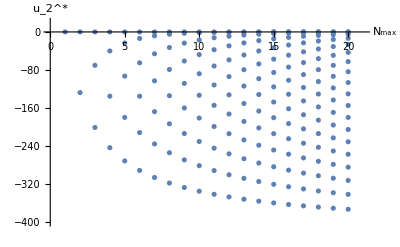

```mathematica
ListPlot[#, PlotRange->{{0,21}, {-400,20}}, AxesLabel->{Subscript[N, max], SuperStar[Subscript[u, 2]]}, AxesStyle->Directive[Black, 12]]&@Flatten[#,1]&@(Tuples/@MapIndexed[{#2,#1}&,%35])
```

```mathematica
Export["Figure2paper2myversionpositionoffixedpointk2.png",%41,"PNG"]
```

Figure2paper2myversionpositionoffixedpointk2.png

Next we will follow the first interacting fixed point for u_2^* and see how the corresponding u_3^* and u_4^* value behave.

```mathematica
K2firstinteractingpoint = Table[{-(Nmax-1), Reverse[Sort[Klist[Nmax], Less]][[2]]},{Nmax,3,21}]
```

{{-2,128 (-5+2 √6) π^2},{-3,π^2 Root-7.11Root[8053063680+1541406720 #1+58245120 #1^2+98432 #1^3+63 #1^4&,2]-7.11392573753596},{-4,π^2 Root-4.06Root[27707693019955200+10047646492262400 #1+884439798251520 #1^2+22588067676160 #1^3+58610647040 #1^4+72309888 #1^5+39627 #1^6&,4]-4.059288006511834},{-5,π^2 Root-2.36Root[1815851369755783987200+1133724911195180236800 #1+177140361220293918720 #1^2+10020864794191462400 #1^3+199446176129351680 #1^4+685709362987008 #1^5+1227908333568 #1^6+1262429952 #1^7+607887 #1^8&,4]-2.3628207643771537},{-6,π^2 Root-1.39Root[69728692598622105108480000+71807842416992477773824000 #1+17813129545910052716544000 #1^2+1716037832169432180326400 #1^3+71927293312542745559040 #1^4+1208053985333194260480 #1^5+5063908590931148800 #1^6+11711825806688256 #1^7+17150936796672 #1^8+15389647812 #1^9+6625395 #1^10&,6]-1.3895613899473516},{-7,π^2 Root-0.821Root[68546093972149474205840179200000+114359518498066564192634142720000 #1+42377409551459171731872153600000 #1^2+6213771556763733689773326336000 #1^3+429617296112453832029503488000 #1^4+14447739116472031498783948800 #1^5+215302599163932942375321600 #1^6+1043487541565201915576320 #1^7+2921490536132279009280 #1^8+5457164492785582080 #1^9+6930565767917568 #1^10+5559534454824 #1^11+2167220853 #1^12&,6]-0.8205088522416909},{-8,π^2 Root-0.484Root[1383608938884106685998614131087769600000+3724548638550804822873166689148600320000 #1+1984289744801988729591954279380287488000 #1^2+415769275417219080484257036572295168000 #1^3+42539642619816658038374227468143820800 #1^4+2296411250622915101038899930071040000 #1^5+65201510488970028126817485638860800 #1^6+891548850623812684437133501399040 #1^7+4819055048763858815207520337920 #1^8+15667745106256938703614115840 #1^9+35163185571809340401123328 #1^10+56663197602349559316480 #1^11+64246725910664478720 #1^12+46775965307879808 #1^13+16673565116439 #1^14&,8]-0.4844302767219654},{-9,π^2 Root-0.285Root[906761954187088157736051756949680685056000000+3955167118753161400968728658264135932313600000 #1+2951564913359370128385983847362631397539840000 #1^2+848521908654367229994294709413742305607680000 #1^3+120741201728596300739764770791813202051072000 #1^4+9440047083333650427516751391381331640320000 #1^5+419772828878768518445198385500928344064000 #1^6+10424811571454218189268463480220732620800 #1^7+133866231883691890290003137537454899200 #1^8+786750486793446020715564956542566400 #1^9+2885436486722874338485593587056640 #1^10+7492533595644489844957076520960 #1^11+14448753523145427627037163520 #1^12+20751515809990567218118656 #1^13+21373749106768200941568 #1^14+14275513706564791296 #1^15+4689832188260835 #1^16&,8]-0.28516882575894154},{-10,π^2 Root-0.167Root[12167381655211625696228579556422262473701195776000000+86782748193915930138623378549391585177552027648000000 #1+89051275480541130925772533228970615182615746969600000 #1^2+34141623038229661758474641331432219780818738872320000 #1^3+6488823765066314411081651724324874966614203695104000 #1^4+692006685132860657870447100150964530092017975296000 #1^5+43774488709917412527772402219851690596179220889600 #1^6+1663858294424497614817006506826821422640896409600 #1^7+37087549496566513248636587236716193601552384000 #1^8+454612110696945625123781835784234055111802880 #1^9+2852382211946897762076531117631410714705920 #1^10+11551540608548457135995055663252745748480 #1^11+33812022019000944466827074523466039296 #1^12+75235753836448054624553108187906048 #1^13+129097356208103035096348760211456 #1^14+168447320654693672686687617024 #1^15+159456906135231949223755776 #1^16+98493726703257011782656 #1^17+30016201485347065989 #1^18&,10]-0.16706957044637868},{-11,π^2 Root-0.0973Root[9967519051949363770350452372621117418456019579699200000000+117614469019070224683974513396782852013563684533043200000000 #1+163760355503030406202580860226331881186486322008476876800000 #1^2+82006049212017511861082466782150552107951841767902412800000 #1^3+20232381600596162426437704651357419169429298154506813440000 #1^4+2829353862076829339761301889630584780145726071400038400000 #1^5+240431025829909197136905997439757193040428512653082624000 #1^6+12796882725585596051624891422371800893427304672264192000 #1^7+427174597319066975853861717153016972255562564003430400 #1^8+8714636836358590064271953618728207226242446707916800 #1^9+103164256703046037103925975660019309083011055616000 #1^10+681820904624116380746591137648422561054950686720 #1^11+2999765117849175855733080186439428301284966400 #1^12+9710033716723514643452813171077791812157440 #1^13+24316392009473490451602090162453567504384 #1^14+48077880631451099508552111802137182208 #1^15+74929670195404741139790355255787520 #1^16+89950170250033422976510379163648 #1^17+78926806711196899709614424064 #1^18+45377446801676035211028864 #1^19+12898736425248974677377 #1^20&,10]-0.09730279138963951},{-12,π^2 Root-0.0563Root[377241092259889648591004384964686335781001711273658810368000000000+7458326851310971406420786210546467243440953895054707628441600000000 #1+13959043852547055690755102456433681141429164998330743603068928000000 #1^2+8987849305588866243350971441442445619577376479832746848419840000000 #1^3+2818428189509709770148536622992545516370777703063126871218585600000 #1^4+502563808939695389662317781680358120376347014004429869495091200000 #1^5+55224285037373547886698702600481050147418468021153166933360640000 #1^6+3898284963053204578848299483573871952952923224839855517204480000 #1^7+179621592672472939321858402786312388212107139202146677817344000 #1^8+5375385116003268739004470016705665859764333100502091825152000 #1^9+«3»+38210735012623184271553586564574884816628643948134400 #1^13+134789111062175988223572499862198151241036883558400 #1^14+373058294579220278219109263644316781762565898240 #1^15+829288417200851185521740934549298832348282880 #1^16+1488669961101032193544393768937986480668672 #1^17+2135733351286925935269488687398546046976 #1^18+2380107798328316003600128225412382720 #1^19+1948563732419686202100064576856064 #1^20+1048290333249030985970601833088 #1^21+279245623399676129907846135 #1^22&,12]-0.0563012148563815},{-13,π^2 Root-0.0324Root[74168616667032384030180190119137051105231184450091511388831744000000000+2488230560883514195753024195492112792053241412486774773992390656000000000 #1+6220978258355259501856443864104027354799578469833383796436614774784000000 #1^2+5088268220948454097314971891438980095641748381944594121251264397312000000 #1^3+1995418605787216610644228769730129219388771121271973095668847319449600000 #1^4+444316962468834606697745333860618007300947197947614173058259170099200000 #1^5+61437685356057052681202454891274923091541999908041698050727812792320000 #1^6+5544986079422597070661652589743261354029022982194402377784497274880000 #1^7+335076490462103158842341228863785942999500127177403345131257462784000 #1^8+«7»+30728674446540729351533656849231274066529285067243520 #1^16+75446761528622445697913291975390743131684555718656 #1^17+152212231007212393285203055695759270711782277120 #1^18+251591728657723039918912914442421969098899456 #1^19+335416528039009191856946985717914834829312 #1^20+349367180464640844938218170195879395328 #1^21+268281088511462233731522702819827712 #1^22+135659396694236804329101281632512 #1^23+34003325196208048787859131379 #1^24&,12]-0.032356975413050694},{-14,π^2 Root-0.0185Root[1007079277572965798133953864683271472799094277947610563600290739650560000000000+58022291329925857148975540996463038723729637210863143784670812820209664000000000 #1+193074609765787896424532727625330058273158798717947578283988223001247088640000000 #1^2+198734295414564490656405177798177723724971607149635783929295428726302965760000000 #1^3+96230897635649284982396231057190515229001917282765948347097245879743021056000000 #1^4+26328830199140046754363954266835779423899856704684812508632438149948112896000000 #1^5+4488421744418738017286120902319563866751611967378035565183337910493406822400000 #1^6+504451340209521092802587168049034452214369396418054020062961718976420249600000 #1^7+38601928423320315893035705654798376090762268150963563115534592378719436800000 #1^8+«9»+484973285395820539766542347901336327618047621214167367680 #1^18+1080348652586843294176940929087148143945296970864656384 #1^19+2007122100071716471574299213542841928545430868590592 #1^20+3084977641910488367818205866540636450857576038400 #1^21+3848881553731829633742483051022954488938889216 #1^22+3767101850253509207971556008780136568324096 #1^23+2725265515138102654216628346352825417728 #1^24+1300260533634124252850483173779260832 #1^25+307766320078648696618720359629637 #1^26&,14]-0.01847062919265036},{-15,π^2 Root-0.0105Root[230999816372576602912773801665590077344765049098511120636380288698086850560000000000+23109270787525730351969773378836826156186601097391995989579979187414565388288000000000 #1+102190562908872046331260822053323706037419417434773978246785824906245105747230720000000 #1^2+131408953030214182894976493235236621870787906946424559249034492429294713826181120000000 #1^3+77770165416589810751876982633659911616095030394605819784631699256943539472302080000000 #1^4+25811560015825520781757245985490015190038047612750816265265963537240207082389504000000 #1^5+5339315571326140565926170766441956261388557083930799083128257235103877182993203200000 #1^6+732513511058173485852164679578161348831290472010620553634242811659152304740761600000 #1^7+«13»+269503060189786218565215946041689720506534959406896906240 #1^21+465801957863004314152292264441870702023919866050772992 #1^22+670615682110497682095683455413227164221912303796224 #1^23+787282710952859894828323938758193468049949982720 #1^24+727243771470944286924102932020234829288964096 #1^25+497498050826313859125152510917907045486592 #1^26+224714107089789019784205897770144443296 #1^27+50386612217546071474603079927804361 #1^28&,14]-0.010474667943305621},{-16,π^2 Root-5.90 × 10^-3Root[10786397825627640927050225004493729307567397108625517671443395752583946634788864000000000000+1892316660120275052228008969922743420174645912965004889058835482100906745749569536000000000000 #1+11122273608594170161114024931696152175548537882765108594245245171975116723416345870336000000000 #1^2+17767109317975088655469262452084560432868492887616851997090738311041415242285440617676800000000 #1^3+12745527642203722914787237572567744076888256338878984083938400983221914989122957984399360000000 #1^4+5078384615408189695870873301875191107913776336944102817666708202968256166568863255756800000000 #1^5+1258586752708883687318397163472197353303269683670407610530031725837846074027671468113920000000 #1^6+«17»+22931550132948702297861656758125483993245441324101952077824 #1^24+31098647567422857577226301056056665898581417944728731648 #1^25+34505904240313068566683108756008930360083892431486976 #1^26+30193540787889516416079525210141518149025896857600 #1^27+19594442084827936290751073963985022011094917120 #1^28+8403762423959177228812671658738537131527040 #1^29+1790110485295447108175114968575673225893 #1^30&,16]-0.005902985042955165},{-17,π^2 Root-3.31 × 10^-3Root[98965631506046630611322896425230146146103171167523469656200013765787813732053218754560000000000000+30715982982440498520881890114232657869662660472881022487428157776102609353284720120561664000000000000 #1+240331507284812439170397865365393410138644354307010872608874977377608206436258804814273576960000000000 #1^2+474851022112315902740812215719256918482573116821722254703654150946730532891656676833625112576000000000 #1^3+410120269997196044854564722052819364964400753962125217782600973257311075463811081292077858816000000000 #1^4+194503285223529076756697438894669666987640382989848126511333601881792900671268996645177733939200000000 #1^5+57156322155991594284659126139485848301425709510637662701918113050704108381569002129119216926720000000 #1^6+«19»+231038094612052591183018006841762526319425169437262765319258112 #1^26+296468706008747512495354368536449142040174676723264420577280 #1^27+312046299704816202980039425192809756350319628065624293376 #1^28+259463787193568280324034950672061106212969081306349568 #1^29+160187550070097017141982220725058606520660925128704 #1^30+65405737087408338006311426481613820807791691520 #1^31+13269232717045632229723158277413798800555079 #1^32&,16]-0.003306968307486797},{-18,π^2 Root-1.84 × 10^-3Root[303211693533277715240015980650791523603600064648427746520422851775730830014774508045970964480000000000000+167789196915468380289323856267195515589201283983084543990362717850896452906387807460437134409728000000000000 #1+1752168853423604282447748971565327661939175027837367509668378254673245868880560342219808257490288640000000000 #1^2+4268037728375677309223235727222036516679786268291286556037188416694212630115504018850087503816294400000000000 #1^3+4413421915138683896079992629763790672366484312140628801386695050400844227016814536454884326240786841600000000 #1^4+2473667061087532463740795927285269797059877618555548391791290743468364458641453342499691419554912665600000000 #1^5+854516755288978978554299655148691137567342108228882048772417446432318708651880455150016176070181519360000000 #1^6+«21»+808892439696220440994962357446563190505563823311590130605470253056 #1^28+985775015725711241552379002920274687325290240813331679279054848 #1^29+987320524276746387267902591985027974170344407288345612255232 #1^30+782243379625038966133190365752531206973422337789954883584 #1^31+460589804279113864316667059652919733446975871029223424 #1^32+179463086722051499978925437696309361882555277883904 #1^33+34755668815507492191143773454379882593938958625 #1^34&,18]-0.001842386764596553},{-19,π^2 Root-1.02 × 10^-3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 #1^31+11004408092786726856174412810415395363511994424266004079277244416 #1^32+8327703083106635932455803399929948004314853622214618798620672 #1^33+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,18]-0.001021153562458243},{-20,π^2 Root-5.63 × 10^-4Root[44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 #1^4+6261330730743702716197243529820454851597238604902324544172276014301723661251208597092594089056223736227798508896256000000000 #1^5+«27»+194300316806694894776952441240579511038783029720372172196124756054900736 #1^33+177580004966680398442829671012813076841456308886730433293539059171328 #1^34+128636035084569806253334820169957311036671675652020191909610782720 #1^35+69342832633484196825805144687266347903661885736694910897217536 #1^36+24757799297747699127199424335828812438082918959401431721856 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,20]-0.0005632784942451307}}

```mathematica
K2firstpointvalue =  Table[Reverse[Sort[Klist[Nmax], Less]][[2]],{Nmax,3,21}]
```

{128 (-5+2 √6) π^2,π^2 Root-7.11Root[8053063680+1541406720 #1+58245120 #1^2+98432 #1^3+63 #1^4&,2]-7.11392573753596,π^2 Root-4.06Root[27707693019955200+10047646492262400 #1+884439798251520 #1^2+22588067676160 #1^3+58610647040 #1^4+72309888 #1^5+39627 #1^6&,4]-4.059288006511834,π^2 Root-2.36Root[1815851369755783987200+1133724911195180236800 #1+177140361220293918720 #1^2+10020864794191462400 #1^3+199446176129351680 #1^4+685709362987008 #1^5+1227908333568 #1^6+1262429952 #1^7+607887 #1^8&,4]-2.3628207643771537,π^2 Root-1.39Root[69728692598622105108480000+71807842416992477773824000 #1+17813129545910052716544000 #1^2+1716037832169432180326400 #1^3+71927293312542745559040 #1^4+1208053985333194260480 #1^5+5063908590931148800 #1^6+11711825806688256 #1^7+17150936796672 #1^8+15389647812 #1^9+6625395 #1^10&,6]-1.3895613899473516,π^2 Root-0.821Root[68546093972149474205840179200000+114359518498066564192634142720000 #1+42377409551459171731872153600000 #1^2+6213771556763733689773326336000 #1^3+429617296112453832029503488000 #1^4+14447739116472031498783948800 #1^5+215302599163932942375321600 #1^6+1043487541565201915576320 #1^7+2921490536132279009280 #1^8+5457164492785582080 #1^9+6930565767917568 #1^10+5559534454824 #1^11+2167220853 #1^12&,6]-0.8205088522416909,π^2 Root-0.484Root[1383608938884106685998614131087769600000+3724548638550804822873166689148600320000 #1+1984289744801988729591954279380287488000 #1^2+415769275417219080484257036572295168000 #1^3+42539642619816658038374227468143820800 #1^4+2296411250622915101038899930071040000 #1^5+65201510488970028126817485638860800 #1^6+891548850623812684437133501399040 #1^7+4819055048763858815207520337920 #1^8+15667745106256938703614115840 #1^9+35163185571809340401123328 #1^10+56663197602349559316480 #1^11+64246725910664478720 #1^12+46775965307879808 #1^13+16673565116439 #1^14&,8]-0.4844302767219654,π^2 Root-0.285Root[906761954187088157736051756949680685056000000+3955167118753161400968728658264135932313600000 #1+2951564913359370128385983847362631397539840000 #1^2+848521908654367229994294709413742305607680000 #1^3+120741201728596300739764770791813202051072000 #1^4+9440047083333650427516751391381331640320000 #1^5+419772828878768518445198385500928344064000 #1^6+10424811571454218189268463480220732620800 #1^7+133866231883691890290003137537454899200 #1^8+786750486793446020715564956542566400 #1^9+2885436486722874338485593587056640 #1^10+7492533595644489844957076520960 #1^11+14448753523145427627037163520 #1^12+20751515809990567218118656 #1^13+21373749106768200941568 #1^14+14275513706564791296 #1^15+4689832188260835 #1^16&,8]-0.28516882575894154,π^2 Root-0.167Root[12167381655211625696228579556422262473701195776000000+86782748193915930138623378549391585177552027648000000 #1+89051275480541130925772533228970615182615746969600000 #1^2+34141623038229661758474641331432219780818738872320000 #1^3+6488823765066314411081651724324874966614203695104000 #1^4+692006685132860657870447100150964530092017975296000 #1^5+43774488709917412527772402219851690596179220889600 #1^6+1663858294424497614817006506826821422640896409600 #1^7+37087549496566513248636587236716193601552384000 #1^8+454612110696945625123781835784234055111802880 #1^9+2852382211946897762076531117631410714705920 #1^10+11551540608548457135995055663252745748480 #1^11+33812022019000944466827074523466039296 #1^12+75235753836448054624553108187906048 #1^13+129097356208103035096348760211456 #1^14+168447320654693672686687617024 #1^15+159456906135231949223755776 #1^16+98493726703257011782656 #1^17+30016201485347065989 #1^18&,10]-0.16706957044637868,π^2 Root-0.0973Root[9967519051949363770350452372621117418456019579699200000000+117614469019070224683974513396782852013563684533043200000000 #1+163760355503030406202580860226331881186486322008476876800000 #1^2+82006049212017511861082466782150552107951841767902412800000 #1^3+20232381600596162426437704651357419169429298154506813440000 #1^4+2829353862076829339761301889630584780145726071400038400000 #1^5+240431025829909197136905997439757193040428512653082624000 #1^6+12796882725585596051624891422371800893427304672264192000 #1^7+427174597319066975853861717153016972255562564003430400 #1^8+8714636836358590064271953618728207226242446707916800 #1^9+103164256703046037103925975660019309083011055616000 #1^10+681820904624116380746591137648422561054950686720 #1^11+2999765117849175855733080186439428301284966400 #1^12+9710033716723514643452813171077791812157440 #1^13+24316392009473490451602090162453567504384 #1^14+48077880631451099508552111802137182208 #1^15+74929670195404741139790355255787520 #1^16+89950170250033422976510379163648 #1^17+78926806711196899709614424064 #1^18+45377446801676035211028864 #1^19+12898736425248974677377 #1^20&,10]-0.09730279138963951,π^2 Root-0.0563Root[377241092259889648591004384964686335781001711273658810368000000000+7458326851310971406420786210546467243440953895054707628441600000000 #1+13959043852547055690755102456433681141429164998330743603068928000000 #1^2+8987849305588866243350971441442445619577376479832746848419840000000 #1^3+2818428189509709770148536622992545516370777703063126871218585600000 #1^4+502563808939695389662317781680358120376347014004429869495091200000 #1^5+55224285037373547886698702600481050147418468021153166933360640000 #1^6+3898284963053204578848299483573871952952923224839855517204480000 #1^7+179621592672472939321858402786312388212107139202146677817344000 #1^8+5375385116003268739004470016705665859764333100502091825152000 #1^9+«3»+38210735012623184271553586564574884816628643948134400 #1^13+134789111062175988223572499862198151241036883558400 #1^14+373058294579220278219109263644316781762565898240 #1^15+829288417200851185521740934549298832348282880 #1^16+1488669961101032193544393768937986480668672 #1^17+2135733351286925935269488687398546046976 #1^18+2380107798328316003600128225412382720 #1^19+1948563732419686202100064576856064 #1^20+1048290333249030985970601833088 #1^21+279245623399676129907846135 #1^22&,12]-0.0563012148563815,π^2 Root-0.0324Root[74168616667032384030180190119137051105231184450091511388831744000000000+2488230560883514195753024195492112792053241412486774773992390656000000000 #1+6220978258355259501856443864104027354799578469833383796436614774784000000 #1^2+5088268220948454097314971891438980095641748381944594121251264397312000000 #1^3+1995418605787216610644228769730129219388771121271973095668847319449600000 #1^4+444316962468834606697745333860618007300947197947614173058259170099200000 #1^5+61437685356057052681202454891274923091541999908041698050727812792320000 #1^6+5544986079422597070661652589743261354029022982194402377784497274880000 #1^7+335076490462103158842341228863785942999500127177403345131257462784000 #1^8+«7»+30728674446540729351533656849231274066529285067243520 #1^16+75446761528622445697913291975390743131684555718656 #1^17+152212231007212393285203055695759270711782277120 #1^18+251591728657723039918912914442421969098899456 #1^19+335416528039009191856946985717914834829312 #1^20+349367180464640844938218170195879395328 #1^21+268281088511462233731522702819827712 #1^22+135659396694236804329101281632512 #1^23+34003325196208048787859131379 #1^24&,12]-0.032356975413050694,π^2 Root-0.0185Root[1007079277572965798133953864683271472799094277947610563600290739650560000000000+58022291329925857148975540996463038723729637210863143784670812820209664000000000 #1+193074609765787896424532727625330058273158798717947578283988223001247088640000000 #1^2+198734295414564490656405177798177723724971607149635783929295428726302965760000000 #1^3+96230897635649284982396231057190515229001917282765948347097245879743021056000000 #1^4+26328830199140046754363954266835779423899856704684812508632438149948112896000000 #1^5+4488421744418738017286120902319563866751611967378035565183337910493406822400000 #1^6+504451340209521092802587168049034452214369396418054020062961718976420249600000 #1^7+38601928423320315893035705654798376090762268150963563115534592378719436800000 #1^8+«9»+484973285395820539766542347901336327618047621214167367680 #1^18+1080348652586843294176940929087148143945296970864656384 #1^19+2007122100071716471574299213542841928545430868590592 #1^20+3084977641910488367818205866540636450857576038400 #1^21+3848881553731829633742483051022954488938889216 #1^22+3767101850253509207971556008780136568324096 #1^23+2725265515138102654216628346352825417728 #1^24+1300260533634124252850483173779260832 #1^25+307766320078648696618720359629637 #1^26&,14]-0.01847062919265036,π^2 Root-0.0105Root[230999816372576602912773801665590077344765049098511120636380288698086850560000000000+23109270787525730351969773378836826156186601097391995989579979187414565388288000000000 #1+102190562908872046331260822053323706037419417434773978246785824906245105747230720000000 #1^2+131408953030214182894976493235236621870787906946424559249034492429294713826181120000000 #1^3+77770165416589810751876982633659911616095030394605819784631699256943539472302080000000 #1^4+25811560015825520781757245985490015190038047612750816265265963537240207082389504000000 #1^5+5339315571326140565926170766441956261388557083930799083128257235103877182993203200000 #1^6+732513511058173485852164679578161348831290472010620553634242811659152304740761600000 #1^7+«13»+269503060189786218565215946041689720506534959406896906240 #1^21+465801957863004314152292264441870702023919866050772992 #1^22+670615682110497682095683455413227164221912303796224 #1^23+787282710952859894828323938758193468049949982720 #1^24+727243771470944286924102932020234829288964096 #1^25+497498050826313859125152510917907045486592 #1^26+224714107089789019784205897770144443296 #1^27+50386612217546071474603079927804361 #1^28&,14]-0.010474667943305621,π^2 Root-5.90 × 10^-3Root[10786397825627640927050225004493729307567397108625517671443395752583946634788864000000000000+1892316660120275052228008969922743420174645912965004889058835482100906745749569536000000000000 #1+11122273608594170161114024931696152175548537882765108594245245171975116723416345870336000000000 #1^2+17767109317975088655469262452084560432868492887616851997090738311041415242285440617676800000000 #1^3+12745527642203722914787237572567744076888256338878984083938400983221914989122957984399360000000 #1^4+5078384615408189695870873301875191107913776336944102817666708202968256166568863255756800000000 #1^5+1258586752708883687318397163472197353303269683670407610530031725837846074027671468113920000000 #1^6+«17»+22931550132948702297861656758125483993245441324101952077824 #1^24+31098647567422857577226301056056665898581417944728731648 #1^25+34505904240313068566683108756008930360083892431486976 #1^26+30193540787889516416079525210141518149025896857600 #1^27+19594442084827936290751073963985022011094917120 #1^28+8403762423959177228812671658738537131527040 #1^29+1790110485295447108175114968575673225893 #1^30&,16]-0.005902985042955165,π^2 Root-3.31 × 10^-3Root[98965631506046630611322896425230146146103171167523469656200013765787813732053218754560000000000000+30715982982440498520881890114232657869662660472881022487428157776102609353284720120561664000000000000 #1+240331507284812439170397865365393410138644354307010872608874977377608206436258804814273576960000000000 #1^2+474851022112315902740812215719256918482573116821722254703654150946730532891656676833625112576000000000 #1^3+410120269997196044854564722052819364964400753962125217782600973257311075463811081292077858816000000000 #1^4+194503285223529076756697438894669666987640382989848126511333601881792900671268996645177733939200000000 #1^5+57156322155991594284659126139485848301425709510637662701918113050704108381569002129119216926720000000 #1^6+«19»+231038094612052591183018006841762526319425169437262765319258112 #1^26+296468706008747512495354368536449142040174676723264420577280 #1^27+312046299704816202980039425192809756350319628065624293376 #1^28+259463787193568280324034950672061106212969081306349568 #1^29+160187550070097017141982220725058606520660925128704 #1^30+65405737087408338006311426481613820807791691520 #1^31+13269232717045632229723158277413798800555079 #1^32&,16]-0.003306968307486797,π^2 Root-1.84 × 10^-3Root[303211693533277715240015980650791523603600064648427746520422851775730830014774508045970964480000000000000+167789196915468380289323856267195515589201283983084543990362717850896452906387807460437134409728000000000000 #1+1752168853423604282447748971565327661939175027837367509668378254673245868880560342219808257490288640000000000 #1^2+4268037728375677309223235727222036516679786268291286556037188416694212630115504018850087503816294400000000000 #1^3+4413421915138683896079992629763790672366484312140628801386695050400844227016814536454884326240786841600000000 #1^4+2473667061087532463740795927285269797059877618555548391791290743468364458641453342499691419554912665600000000 #1^5+854516755288978978554299655148691137567342108228882048772417446432318708651880455150016176070181519360000000 #1^6+«21»+808892439696220440994962357446563190505563823311590130605470253056 #1^28+985775015725711241552379002920274687325290240813331679279054848 #1^29+987320524276746387267902591985027974170344407288345612255232 #1^30+782243379625038966133190365752531206973422337789954883584 #1^31+460589804279113864316667059652919733446975871029223424 #1^32+179463086722051499978925437696309361882555277883904 #1^33+34755668815507492191143773454379882593938958625 #1^34&,18]-0.001842386764596553,π^2 Root-1.02 × 10^-3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 #1^31+11004408092786726856174412810415395363511994424266004079277244416 #1^32+8327703083106635932455803399929948004314853622214618798620672 #1^33+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,18]-0.001021153562458243,π^2 Root-5.63 × 10^-4Root[44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 #1^4+6261330730743702716197243529820454851597238604902324544172276014301723661251208597092594089056223736227798508896256000000000 #1^5+«27»+194300316806694894776952441240579511038783029720372172196124756054900736 #1^33+177580004966680398442829671012813076841456308886730433293539059171328 #1^34+128636035084569806253334820169957311036671675652020191909610782720 #1^35+69342832633484196825805144687266347903661885736694910897217536 #1^36+24757799297747699127199424335828812438082918959401431721856 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,20]-0.0005632784942451307}

```mathematica
K2firstpointvalue[[2]]
```

π^2 Root-7.11Root[8053063680+1541406720 #1+58245120 #1^2+98432 #1^3+63 #1^4&,2]-7.11392573753596

```mathematica
K3firstinteractingpoint= Table[{-x-1, K[3]/.FPLitim[20][[2]]/.K[2]-> K2firstpointvalue[[x]]}, {x, 2, 19}]
```

{{-3,32 π^4 Root-7.11Root[8053063680+1541406720 #1+58245120 #1^2+98432 #1^3+63 #1^4&,2]-7.11392573753596+5/2 π^4 (Root-7.11Root[8053063680+1541406720 #1+58245120 #1^2+98432 #1^3+63 #1^4&,2]-7.11392573753596)^2+1/512 π^4 (Root-7.11Root[8053063680+1541406720 #1+58245120 #1^2+98432 #1^3+63 #1^4&,2]-7.11392573753596)^3},{-4,32 π^4 Root-4.06Root[27707693019955200+10047646492262400 #1+884439798251520 #1^2+22588067676160 #1^3+58610647040 #1^4+72309888 #1^5+39627 #1^6&,4]-4.059288006511834+5/2 π^4 (Root-4.06Root[27707693019955200+10047646492262400 #1+884439798251520 #1^2+22588067676160 #1^3+58610647040 #1^4+72309888 #1^5+39627 #1^6&,4]-4.059288006511834)^2+1/512 π^4 (Root-4.06Root[27707693019955200+10047646492262400 #1+884439798251520 #1^2+22588067676160 #1^3+58610647040 #1^4+72309888 #1^5+39627 #1^6&,4]-4.059288006511834)^3},{-5,32 π^4 Root-2.36Root[1815851369755783987200+1133724911195180236800 #1+177140361220293918720 #1^2+10020864794191462400 #1^3+199446176129351680 #1^4+685709362987008 #1^5+1227908333568 #1^6+1262429952 #1^7+607887 #1^8&,4]-2.3628207643771537+5/2 π^4 (Root-2.36Root[1815851369755783987200+1133724911195180236800 #1+177140361220293918720 #1^2+10020864794191462400 #1^3+199446176129351680 #1^4+685709362987008 #1^5+1227908333568 #1^6+1262429952 #1^7+607887 #1^8&,4]-2.3628207643771537)^2+1/512 π^4 (Root-2.36Root[1815851369755783987200+1133724911195180236800 #1+177140361220293918720 #1^2+10020864794191462400 #1^3+199446176129351680 #1^4+685709362987008 #1^5+1227908333568 #1^6+1262429952 #1^7+607887 #1^8&,4]-2.3628207643771537)^3},{-6,32 π^4 Root-1.39Root[69728692598622105108480000+71807842416992477773824000 #1+17813129545910052716544000 #1^2+1716037832169432180326400 #1^3+71927293312542745559040 #1^4+1208053985333194260480 #1^5+5063908590931148800 #1^6+11711825806688256 #1^7+17150936796672 #1^8+15389647812 #1^9+6625395 #1^10&,6]-1.3895613899473516+5/2 π^4 (Root-1.39Root[69728692598622105108480000+71807842416992477773824000 #1+17813129545910052716544000 #1^2+1716037832169432180326400 #1^3+71927293312542745559040 #1^4+1208053985333194260480 #1^5+5063908590931148800 #1^6+11711825806688256 #1^7+17150936796672 #1^8+15389647812 #1^9+6625395 #1^10&,6]-1.3895613899473516)^2+1/512 π^4 (Root-1.39Root[69728692598622105108480000+71807842416992477773824000 #1+17813129545910052716544000 #1^2+1716037832169432180326400 #1^3+71927293312542745559040 #1^4+1208053985333194260480 #1^5+5063908590931148800 #1^6+11711825806688256 #1^7+17150936796672 #1^8+15389647812 #1^9+6625395 #1^10&,6]-1.3895613899473516)^3},{-7,32 π^4 Root-0.821Root[68546093972149474205840179200000+114359518498066564192634142720000 #1+42377409551459171731872153600000 #1^2+6213771556763733689773326336000 #1^3+429617296112453832029503488000 #1^4+14447739116472031498783948800 #1^5+215302599163932942375321600 #1^6+1043487541565201915576320 #1^7+2921490536132279009280 #1^8+5457164492785582080 #1^9+6930565767917568 #1^10+5559534454824 #1^11+2167220853 #1^12&,6]-0.8205088522416909+5/2 π^4 (Root-0.821Root[68546093972149474205840179200000+114359518498066564192634142720000 #1+42377409551459171731872153600000 #1^2+6213771556763733689773326336000 #1^3+429617296112453832029503488000 #1^4+14447739116472031498783948800 #1^5+215302599163932942375321600 #1^6+1043487541565201915576320 #1^7+2921490536132279009280 #1^8+5457164492785582080 #1^9+6930565767917568 #1^10+5559534454824 #1^11+2167220853 #1^12&,6]-0.8205088522416909)^2+1/512 π^4 (Root-0.821Root[68546093972149474205840179200000+114359518498066564192634142720000 #1+42377409551459171731872153600000 #1^2+6213771556763733689773326336000 #1^3+429617296112453832029503488000 #1^4+14447739116472031498783948800 #1^5+215302599163932942375321600 #1^6+1043487541565201915576320 #1^7+2921490536132279009280 #1^8+5457164492785582080 #1^9+6930565767917568 #1^10+5559534454824 #1^11+2167220853 #1^12&,6]-0.8205088522416909)^3},{-8,32 π^4 Root-0.484Root[1383608938884106685998614131087769600000+3724548638550804822873166689148600320000 #1+1984289744801988729591954279380287488000 #1^2+415769275417219080484257036572295168000 #1^3+42539642619816658038374227468143820800 #1^4+2296411250622915101038899930071040000 #1^5+65201510488970028126817485638860800 #1^6+891548850623812684437133501399040 #1^7+4819055048763858815207520337920 #1^8+15667745106256938703614115840 #1^9+35163185571809340401123328 #1^10+56663197602349559316480 #1^11+64246725910664478720 #1^12+46775965307879808 #1^13+16673565116439 #1^14&,8]-0.4844302767219654+5/2 π^4 (Root-0.484Root[1383608938884106685998614131087769600000+3724548638550804822873166689148600320000 #1+1984289744801988729591954279380287488000 #1^2+415769275417219080484257036572295168000 #1^3+42539642619816658038374227468143820800 #1^4+2296411250622915101038899930071040000 #1^5+65201510488970028126817485638860800 #1^6+891548850623812684437133501399040 #1^7+4819055048763858815207520337920 #1^8+15667745106256938703614115840 #1^9+35163185571809340401123328 #1^10+56663197602349559316480 #1^11+64246725910664478720 #1^12+46775965307879808 #1^13+16673565116439 #1^14&,8]-0.4844302767219654)^2+1/512 π^4 (Root-0.484Root[1383608938884106685998614131087769600000+3724548638550804822873166689148600320000 #1+1984289744801988729591954279380287488000 #1^2+415769275417219080484257036572295168000 #1^3+42539642619816658038374227468143820800 #1^4+2296411250622915101038899930071040000 #1^5+65201510488970028126817485638860800 #1^6+891548850623812684437133501399040 #1^7+4819055048763858815207520337920 #1^8+15667745106256938703614115840 #1^9+35163185571809340401123328 #1^10+56663197602349559316480 #1^11+64246725910664478720 #1^12+46775965307879808 #1^13+16673565116439 #1^14&,8]-0.4844302767219654)^3},{-9,32 π^4 Root-0.285Root[906761954187088157736051756949680685056000000+3955167118753161400968728658264135932313600000 #1+2951564913359370128385983847362631397539840000 #1^2+848521908654367229994294709413742305607680000 #1^3+120741201728596300739764770791813202051072000 #1^4+9440047083333650427516751391381331640320000 #1^5+419772828878768518445198385500928344064000 #1^6+10424811571454218189268463480220732620800 #1^7+133866231883691890290003137537454899200 #1^8+786750486793446020715564956542566400 #1^9+2885436486722874338485593587056640 #1^10+7492533595644489844957076520960 #1^11+14448753523145427627037163520 #1^12+20751515809990567218118656 #1^13+21373749106768200941568 #1^14+14275513706564791296 #1^15+4689832188260835 #1^16&,8]-0.28516882575894154+5/2 π^4 (Root-0.285Root[906761954187088157736051756949680685056000000+3955167118753161400968728658264135932313600000 #1+2951564913359370128385983847362631397539840000 #1^2+848521908654367229994294709413742305607680000 #1^3+120741201728596300739764770791813202051072000 #1^4+9440047083333650427516751391381331640320000 #1^5+419772828878768518445198385500928344064000 #1^6+10424811571454218189268463480220732620800 #1^7+133866231883691890290003137537454899200 #1^8+786750486793446020715564956542566400 #1^9+2885436486722874338485593587056640 #1^10+7492533595644489844957076520960 #1^11+14448753523145427627037163520 #1^12+20751515809990567218118656 #1^13+21373749106768200941568 #1^14+14275513706564791296 #1^15+4689832188260835 #1^16&,8]-0.28516882575894154)^2+1/512 π^4 (Root-0.285Root[906761954187088157736051756949680685056000000+3955167118753161400968728658264135932313600000 #1+2951564913359370128385983847362631397539840000 #1^2+848521908654367229994294709413742305607680000 #1^3+120741201728596300739764770791813202051072000 #1^4+9440047083333650427516751391381331640320000 #1^5+419772828878768518445198385500928344064000 #1^6+10424811571454218189268463480220732620800 #1^7+133866231883691890290003137537454899200 #1^8+786750486793446020715564956542566400 #1^9+2885436486722874338485593587056640 #1^10+7492533595644489844957076520960 #1^11+14448753523145427627037163520 #1^12+20751515809990567218118656 #1^13+21373749106768200941568 #1^14+14275513706564791296 #1^15+4689832188260835 #1^16&,8]-0.28516882575894154)^3},{-10,32 π^4 Root-0.167Root[12167381655211625696228579556422262473701195776000000+86782748193915930138623378549391585177552027648000000 #1+89051275480541130925772533228970615182615746969600000 #1^2+34141623038229661758474641331432219780818738872320000 #1^3+6488823765066314411081651724324874966614203695104000 #1^4+692006685132860657870447100150964530092017975296000 #1^5+43774488709917412527772402219851690596179220889600 #1^6+1663858294424497614817006506826821422640896409600 #1^7+37087549496566513248636587236716193601552384000 #1^8+454612110696945625123781835784234055111802880 #1^9+2852382211946897762076531117631410714705920 #1^10+11551540608548457135995055663252745748480 #1^11+33812022019000944466827074523466039296 #1^12+75235753836448054624553108187906048 #1^13+129097356208103035096348760211456 #1^14+168447320654693672686687617024 #1^15+159456906135231949223755776 #1^16+98493726703257011782656 #1^17+30016201485347065989 #1^18&,10]-0.16706957044637868+5/2 π^4 (Root-0.167Root[12167381655211625696228579556422262473701195776000000+86782748193915930138623378549391585177552027648000000 #1+89051275480541130925772533228970615182615746969600000 #1^2+34141623038229661758474641331432219780818738872320000 #1^3+6488823765066314411081651724324874966614203695104000 #1^4+692006685132860657870447100150964530092017975296000 #1^5+43774488709917412527772402219851690596179220889600 #1^6+1663858294424497614817006506826821422640896409600 #1^7+37087549496566513248636587236716193601552384000 #1^8+454612110696945625123781835784234055111802880 #1^9+2852382211946897762076531117631410714705920 #1^10+11551540608548457135995055663252745748480 #1^11+33812022019000944466827074523466039296 #1^12+75235753836448054624553108187906048 #1^13+129097356208103035096348760211456 #1^14+168447320654693672686687617024 #1^15+159456906135231949223755776 #1^16+98493726703257011782656 #1^17+30016201485347065989 #1^18&,10]-0.16706957044637868)^2+1/512 π^4 (Root-0.167Root[12167381655211625696228579556422262473701195776000000+86782748193915930138623378549391585177552027648000000 #1+89051275480541130925772533228970615182615746969600000 #1^2+34141623038229661758474641331432219780818738872320000 #1^3+6488823765066314411081651724324874966614203695104000 #1^4+692006685132860657870447100150964530092017975296000 #1^5+43774488709917412527772402219851690596179220889600 #1^6+1663858294424497614817006506826821422640896409600 #1^7+37087549496566513248636587236716193601552384000 #1^8+454612110696945625123781835784234055111802880 #1^9+2852382211946897762076531117631410714705920 #1^10+11551540608548457135995055663252745748480 #1^11+33812022019000944466827074523466039296 #1^12+75235753836448054624553108187906048 #1^13+129097356208103035096348760211456 #1^14+168447320654693672686687617024 #1^15+159456906135231949223755776 #1^16+98493726703257011782656 #1^17+30016201485347065989 #1^18&,10]-0.16706957044637868)^3},{-11,32 π^4 Root-0.0973Root[9967519051949363770350452372621117418456019579699200000000+117614469019070224683974513396782852013563684533043200000000 #1+163760355503030406202580860226331881186486322008476876800000 #1^2+82006049212017511861082466782150552107951841767902412800000 #1^3+20232381600596162426437704651357419169429298154506813440000 #1^4+2829353862076829339761301889630584780145726071400038400000 #1^5+240431025829909197136905997439757193040428512653082624000 #1^6+12796882725585596051624891422371800893427304672264192000 #1^7+427174597319066975853861717153016972255562564003430400 #1^8+8714636836358590064271953618728207226242446707916800 #1^9+103164256703046037103925975660019309083011055616000 #1^10+681820904624116380746591137648422561054950686720 #1^11+2999765117849175855733080186439428301284966400 #1^12+9710033716723514643452813171077791812157440 #1^13+24316392009473490451602090162453567504384 #1^14+48077880631451099508552111802137182208 #1^15+74929670195404741139790355255787520 #1^16+89950170250033422976510379163648 #1^17+78926806711196899709614424064 #1^18+45377446801676035211028864 #1^19+12898736425248974677377 #1^20&,10]-0.09730279138963951+5/2 π^4 (Root-0.0973Root[9967519051949363770350452372621117418456019579699200000000+117614469019070224683974513396782852013563684533043200000000 #1+163760355503030406202580860226331881186486322008476876800000 #1^2+82006049212017511861082466782150552107951841767902412800000 #1^3+20232381600596162426437704651357419169429298154506813440000 #1^4+2829353862076829339761301889630584780145726071400038400000 #1^5+240431025829909197136905997439757193040428512653082624000 #1^6+12796882725585596051624891422371800893427304672264192000 #1^7+427174597319066975853861717153016972255562564003430400 #1^8+8714636836358590064271953618728207226242446707916800 #1^9+103164256703046037103925975660019309083011055616000 #1^10+681820904624116380746591137648422561054950686720 #1^11+2999765117849175855733080186439428301284966400 #1^12+9710033716723514643452813171077791812157440 #1^13+24316392009473490451602090162453567504384 #1^14+48077880631451099508552111802137182208 #1^15+74929670195404741139790355255787520 #1^16+89950170250033422976510379163648 #1^17+78926806711196899709614424064 #1^18+45377446801676035211028864 #1^19+12898736425248974677377 #1^20&,10]-0.09730279138963951)^2+1/512 π^4 (Root-0.0973Root[9967519051949363770350452372621117418456019579699200000000+117614469019070224683974513396782852013563684533043200000000 #1+163760355503030406202580860226331881186486322008476876800000 #1^2+82006049212017511861082466782150552107951841767902412800000 #1^3+20232381600596162426437704651357419169429298154506813440000 #1^4+2829353862076829339761301889630584780145726071400038400000 #1^5+240431025829909197136905997439757193040428512653082624000 #1^6+12796882725585596051624891422371800893427304672264192000 #1^7+427174597319066975853861717153016972255562564003430400 #1^8+8714636836358590064271953618728207226242446707916800 #1^9+103164256703046037103925975660019309083011055616000 #1^10+681820904624116380746591137648422561054950686720 #1^11+2999765117849175855733080186439428301284966400 #1^12+9710033716723514643452813171077791812157440 #1^13+24316392009473490451602090162453567504384 #1^14+48077880631451099508552111802137182208 #1^15+74929670195404741139790355255787520 #1^16+89950170250033422976510379163648 #1^17+78926806711196899709614424064 #1^18+45377446801676035211028864 #1^19+12898736425248974677377 #1^20&,10]-0.09730279138963951)^3},{-12,32 π^4 Root-0.0563Root[377241092259889648591004384964686335781001711273658810368000000000+7458326851310971406420786210546467243440953895054707628441600000000 #1+13959043852547055690755102456433681141429164998330743603068928000000 #1^2+8987849305588866243350971441442445619577376479832746848419840000000 #1^3+2818428189509709770148536622992545516370777703063126871218585600000 #1^4+502563808939695389662317781680358120376347014004429869495091200000 #1^5+55224285037373547886698702600481050147418468021153166933360640000 #1^6+3898284963053204578848299483573871952952923224839855517204480000 #1^7+179621592672472939321858402786312388212107139202146677817344000 #1^8+5375385116003268739004470016705665859764333100502091825152000 #1^9+«3»+38210735012623184271553586564574884816628643948134400 #1^13+134789111062175988223572499862198151241036883558400 #1^14+373058294579220278219109263644316781762565898240 #1^15+829288417200851185521740934549298832348282880 #1^16+1488669961101032193544393768937986480668672 #1^17+2135733351286925935269488687398546046976 #1^18+2380107798328316003600128225412382720 #1^19+1948563732419686202100064576856064 #1^20+1048290333249030985970601833088 #1^21+279245623399676129907846135 #1^22&,12]-0.0563012148563815+5/2 π^4 (Root-0.0563Root[377241092259889648591004384964686335781001711273658810368000000000+7458326851310971406420786210546467243440953895054707628441600000000 #1+13959043852547055690755102456433681141429164998330743603068928000000 #1^2+8987849305588866243350971441442445619577376479832746848419840000000 #1^3+2818428189509709770148536622992545516370777703063126871218585600000 #1^4+502563808939695389662317781680358120376347014004429869495091200000 #1^5+55224285037373547886698702600481050147418468021153166933360640000 #1^6+3898284963053204578848299483573871952952923224839855517204480000 #1^7+179621592672472939321858402786312388212107139202146677817344000 #1^8+5375385116003268739004470016705665859764333100502091825152000 #1^9+«3»+38210735012623184271553586564574884816628643948134400 #1^13+134789111062175988223572499862198151241036883558400 #1^14+373058294579220278219109263644316781762565898240 #1^15+829288417200851185521740934549298832348282880 #1^16+1488669961101032193544393768937986480668672 #1^17+2135733351286925935269488687398546046976 #1^18+2380107798328316003600128225412382720 #1^19+1948563732419686202100064576856064 #1^20+1048290333249030985970601833088 #1^21+279245623399676129907846135 #1^22&,12]-0.0563012148563815)^2+1/512 π^4 (Root-0.0563Root[377241092259889648591004384964686335781001711273658810368000000000+7458326851310971406420786210546467243440953895054707628441600000000 #1+13959043852547055690755102456433681141429164998330743603068928000000 #1^2+8987849305588866243350971441442445619577376479832746848419840000000 #1^3+2818428189509709770148536622992545516370777703063126871218585600000 #1^4+502563808939695389662317781680358120376347014004429869495091200000 #1^5+55224285037373547886698702600481050147418468021153166933360640000 #1^6+3898284963053204578848299483573871952952923224839855517204480000 #1^7+179621592672472939321858402786312388212107139202146677817344000 #1^8+5375385116003268739004470016705665859764333100502091825152000 #1^9+«3»+38210735012623184271553586564574884816628643948134400 #1^13+134789111062175988223572499862198151241036883558400 #1^14+373058294579220278219109263644316781762565898240 #1^15+829288417200851185521740934549298832348282880 #1^16+1488669961101032193544393768937986480668672 #1^17+2135733351286925935269488687398546046976 #1^18+2380107798328316003600128225412382720 #1^19+1948563732419686202100064576856064 #1^20+1048290333249030985970601833088 #1^21+279245623399676129907846135 #1^22&,12]-0.0563012148563815)^3},{-13,32 π^4 Root-0.0324Root[74168616667032384030180190119137051105231184450091511388831744000000000+2488230560883514195753024195492112792053241412486774773992390656000000000 #1+6220978258355259501856443864104027354799578469833383796436614774784000000 #1^2+5088268220948454097314971891438980095641748381944594121251264397312000000 #1^3+1995418605787216610644228769730129219388771121271973095668847319449600000 #1^4+444316962468834606697745333860618007300947197947614173058259170099200000 #1^5+61437685356057052681202454891274923091541999908041698050727812792320000 #1^6+5544986079422597070661652589743261354029022982194402377784497274880000 #1^7+335076490462103158842341228863785942999500127177403345131257462784000 #1^8+«7»+30728674446540729351533656849231274066529285067243520 #1^16+75446761528622445697913291975390743131684555718656 #1^17+152212231007212393285203055695759270711782277120 #1^18+251591728657723039918912914442421969098899456 #1^19+335416528039009191856946985717914834829312 #1^20+349367180464640844938218170195879395328 #1^21+268281088511462233731522702819827712 #1^22+135659396694236804329101281632512 #1^23+34003325196208048787859131379 #1^24&,12]-0.032356975413050694+5/2 π^4 (Root-0.0324Root[74168616667032384030180190119137051105231184450091511388831744000000000+2488230560883514195753024195492112792053241412486774773992390656000000000 #1+6220978258355259501856443864104027354799578469833383796436614774784000000 #1^2+5088268220948454097314971891438980095641748381944594121251264397312000000 #1^3+1995418605787216610644228769730129219388771121271973095668847319449600000 #1^4+444316962468834606697745333860618007300947197947614173058259170099200000 #1^5+61437685356057052681202454891274923091541999908041698050727812792320000 #1^6+5544986079422597070661652589743261354029022982194402377784497274880000 #1^7+335076490462103158842341228863785942999500127177403345131257462784000 #1^8+«7»+30728674446540729351533656849231274066529285067243520 #1^16+75446761528622445697913291975390743131684555718656 #1^17+152212231007212393285203055695759270711782277120 #1^18+251591728657723039918912914442421969098899456 #1^19+335416528039009191856946985717914834829312 #1^20+349367180464640844938218170195879395328 #1^21+268281088511462233731522702819827712 #1^22+135659396694236804329101281632512 #1^23+34003325196208048787859131379 #1^24&,12]-0.032356975413050694)^2+1/512 π^4 (Root-0.0324Root[74168616667032384030180190119137051105231184450091511388831744000000000+2488230560883514195753024195492112792053241412486774773992390656000000000 #1+6220978258355259501856443864104027354799578469833383796436614774784000000 #1^2+5088268220948454097314971891438980095641748381944594121251264397312000000 #1^3+1995418605787216610644228769730129219388771121271973095668847319449600000 #1^4+444316962468834606697745333860618007300947197947614173058259170099200000 #1^5+61437685356057052681202454891274923091541999908041698050727812792320000 #1^6+5544986079422597070661652589743261354029022982194402377784497274880000 #1^7+335076490462103158842341228863785942999500127177403345131257462784000 #1^8+«7»+30728674446540729351533656849231274066529285067243520 #1^16+75446761528622445697913291975390743131684555718656 #1^17+152212231007212393285203055695759270711782277120 #1^18+251591728657723039918912914442421969098899456 #1^19+335416528039009191856946985717914834829312 #1^20+349367180464640844938218170195879395328 #1^21+268281088511462233731522702819827712 #1^22+135659396694236804329101281632512 #1^23+34003325196208048787859131379 #1^24&,12]-0.032356975413050694)^3},{-14,32 π^4 Root-0.0185Root[1007079277572965798133953864683271472799094277947610563600290739650560000000000+58022291329925857148975540996463038723729637210863143784670812820209664000000000 #1+193074609765787896424532727625330058273158798717947578283988223001247088640000000 #1^2+198734295414564490656405177798177723724971607149635783929295428726302965760000000 #1^3+96230897635649284982396231057190515229001917282765948347097245879743021056000000 #1^4+26328830199140046754363954266835779423899856704684812508632438149948112896000000 #1^5+4488421744418738017286120902319563866751611967378035565183337910493406822400000 #1^6+504451340209521092802587168049034452214369396418054020062961718976420249600000 #1^7+38601928423320315893035705654798376090762268150963563115534592378719436800000 #1^8+«9»+484973285395820539766542347901336327618047621214167367680 #1^18+1080348652586843294176940929087148143945296970864656384 #1^19+2007122100071716471574299213542841928545430868590592 #1^20+3084977641910488367818205866540636450857576038400 #1^21+3848881553731829633742483051022954488938889216 #1^22+3767101850253509207971556008780136568324096 #1^23+2725265515138102654216628346352825417728 #1^24+1300260533634124252850483173779260832 #1^25+307766320078648696618720359629637 #1^26&,14]-0.01847062919265036+5/2 π^4 (Root-0.0185Root[1007079277572965798133953864683271472799094277947610563600290739650560000000000+58022291329925857148975540996463038723729637210863143784670812820209664000000000 #1+193074609765787896424532727625330058273158798717947578283988223001247088640000000 #1^2+198734295414564490656405177798177723724971607149635783929295428726302965760000000 #1^3+96230897635649284982396231057190515229001917282765948347097245879743021056000000 #1^4+26328830199140046754363954266835779423899856704684812508632438149948112896000000 #1^5+4488421744418738017286120902319563866751611967378035565183337910493406822400000 #1^6+504451340209521092802587168049034452214369396418054020062961718976420249600000 #1^7+38601928423320315893035705654798376090762268150963563115534592378719436800000 #1^8+«9»+484973285395820539766542347901336327618047621214167367680 #1^18+1080348652586843294176940929087148143945296970864656384 #1^19+2007122100071716471574299213542841928545430868590592 #1^20+3084977641910488367818205866540636450857576038400 #1^21+3848881553731829633742483051022954488938889216 #1^22+3767101850253509207971556008780136568324096 #1^23+2725265515138102654216628346352825417728 #1^24+1300260533634124252850483173779260832 #1^25+307766320078648696618720359629637 #1^26&,14]-0.01847062919265036)^2+1/512 π^4 (Root-0.0185Root[1007079277572965798133953864683271472799094277947610563600290739650560000000000+58022291329925857148975540996463038723729637210863143784670812820209664000000000 #1+193074609765787896424532727625330058273158798717947578283988223001247088640000000 #1^2+198734295414564490656405177798177723724971607149635783929295428726302965760000000 #1^3+96230897635649284982396231057190515229001917282765948347097245879743021056000000 #1^4+26328830199140046754363954266835779423899856704684812508632438149948112896000000 #1^5+4488421744418738017286120902319563866751611967378035565183337910493406822400000 #1^6+504451340209521092802587168049034452214369396418054020062961718976420249600000 #1^7+38601928423320315893035705654798376090762268150963563115534592378719436800000 #1^8+«9»+484973285395820539766542347901336327618047621214167367680 #1^18+1080348652586843294176940929087148143945296970864656384 #1^19+2007122100071716471574299213542841928545430868590592 #1^20+3084977641910488367818205866540636450857576038400 #1^21+3848881553731829633742483051022954488938889216 #1^22+3767101850253509207971556008780136568324096 #1^23+2725265515138102654216628346352825417728 #1^24+1300260533634124252850483173779260832 #1^25+307766320078648696618720359629637 #1^26&,14]-0.01847062919265036)^3},{-15,32 π^4 Root-0.0105Root[230999816372576602912773801665590077344765049098511120636380288698086850560000000000+23109270787525730351969773378836826156186601097391995989579979187414565388288000000000 #1+102190562908872046331260822053323706037419417434773978246785824906245105747230720000000 #1^2+131408953030214182894976493235236621870787906946424559249034492429294713826181120000000 #1^3+77770165416589810751876982633659911616095030394605819784631699256943539472302080000000 #1^4+25811560015825520781757245985490015190038047612750816265265963537240207082389504000000 #1^5+5339315571326140565926170766441956261388557083930799083128257235103877182993203200000 #1^6+732513511058173485852164679578161348831290472010620553634242811659152304740761600000 #1^7+«13»+269503060189786218565215946041689720506534959406896906240 #1^21+465801957863004314152292264441870702023919866050772992 #1^22+670615682110497682095683455413227164221912303796224 #1^23+787282710952859894828323938758193468049949982720 #1^24+727243771470944286924102932020234829288964096 #1^25+497498050826313859125152510917907045486592 #1^26+224714107089789019784205897770144443296 #1^27+50386612217546071474603079927804361 #1^28&,14]-0.010474667943305621+5/2 π^4 (Root-0.0105Root[230999816372576602912773801665590077344765049098511120636380288698086850560000000000+23109270787525730351969773378836826156186601097391995989579979187414565388288000000000 #1+102190562908872046331260822053323706037419417434773978246785824906245105747230720000000 #1^2+131408953030214182894976493235236621870787906946424559249034492429294713826181120000000 #1^3+77770165416589810751876982633659911616095030394605819784631699256943539472302080000000 #1^4+25811560015825520781757245985490015190038047612750816265265963537240207082389504000000 #1^5+5339315571326140565926170766441956261388557083930799083128257235103877182993203200000 #1^6+732513511058173485852164679578161348831290472010620553634242811659152304740761600000 #1^7+«13»+269503060189786218565215946041689720506534959406896906240 #1^21+465801957863004314152292264441870702023919866050772992 #1^22+670615682110497682095683455413227164221912303796224 #1^23+787282710952859894828323938758193468049949982720 #1^24+727243771470944286924102932020234829288964096 #1^25+497498050826313859125152510917907045486592 #1^26+224714107089789019784205897770144443296 #1^27+50386612217546071474603079927804361 #1^28&,14]-0.010474667943305621)^2+1/512 π^4 (Root-0.0105Root[230999816372576602912773801665590077344765049098511120636380288698086850560000000000+23109270787525730351969773378836826156186601097391995989579979187414565388288000000000 #1+102190562908872046331260822053323706037419417434773978246785824906245105747230720000000 #1^2+131408953030214182894976493235236621870787906946424559249034492429294713826181120000000 #1^3+77770165416589810751876982633659911616095030394605819784631699256943539472302080000000 #1^4+25811560015825520781757245985490015190038047612750816265265963537240207082389504000000 #1^5+5339315571326140565926170766441956261388557083930799083128257235103877182993203200000 #1^6+732513511058173485852164679578161348831290472010620553634242811659152304740761600000 #1^7+«13»+269503060189786218565215946041689720506534959406896906240 #1^21+465801957863004314152292264441870702023919866050772992 #1^22+670615682110497682095683455413227164221912303796224 #1^23+787282710952859894828323938758193468049949982720 #1^24+727243771470944286924102932020234829288964096 #1^25+497498050826313859125152510917907045486592 #1^26+224714107089789019784205897770144443296 #1^27+50386612217546071474603079927804361 #1^28&,14]-0.010474667943305621)^3},{-16,32 π^4 Root-5.90 × 10^-3Root[10786397825627640927050225004493729307567397108625517671443395752583946634788864000000000000+1892316660120275052228008969922743420174645912965004889058835482100906745749569536000000000000 #1+11122273608594170161114024931696152175548537882765108594245245171975116723416345870336000000000 #1^2+17767109317975088655469262452084560432868492887616851997090738311041415242285440617676800000000 #1^3+12745527642203722914787237572567744076888256338878984083938400983221914989122957984399360000000 #1^4+5078384615408189695870873301875191107913776336944102817666708202968256166568863255756800000000 #1^5+1258586752708883687318397163472197353303269683670407610530031725837846074027671468113920000000 #1^6+«17»+22931550132948702297861656758125483993245441324101952077824 #1^24+31098647567422857577226301056056665898581417944728731648 #1^25+34505904240313068566683108756008930360083892431486976 #1^26+30193540787889516416079525210141518149025896857600 #1^27+19594442084827936290751073963985022011094917120 #1^28+8403762423959177228812671658738537131527040 #1^29+1790110485295447108175114968575673225893 #1^30&,16]-0.005902985042955165+5/2 π^4 (Root-5.90 × 10^-3Root[10786397825627640927050225004493729307567397108625517671443395752583946634788864000000000000+1892316660120275052228008969922743420174645912965004889058835482100906745749569536000000000000 #1+11122273608594170161114024931696152175548537882765108594245245171975116723416345870336000000000 #1^2+17767109317975088655469262452084560432868492887616851997090738311041415242285440617676800000000 #1^3+12745527642203722914787237572567744076888256338878984083938400983221914989122957984399360000000 #1^4+5078384615408189695870873301875191107913776336944102817666708202968256166568863255756800000000 #1^5+1258586752708883687318397163472197353303269683670407610530031725837846074027671468113920000000 #1^6+«17»+22931550132948702297861656758125483993245441324101952077824 #1^24+31098647567422857577226301056056665898581417944728731648 #1^25+34505904240313068566683108756008930360083892431486976 #1^26+30193540787889516416079525210141518149025896857600 #1^27+19594442084827936290751073963985022011094917120 #1^28+8403762423959177228812671658738537131527040 #1^29+1790110485295447108175114968575673225893 #1^30&,16]-0.005902985042955165)^2+1/512 π^4 (Root-5.90 × 10^-3Root[10786397825627640927050225004493729307567397108625517671443395752583946634788864000000000000+1892316660120275052228008969922743420174645912965004889058835482100906745749569536000000000000 #1+11122273608594170161114024931696152175548537882765108594245245171975116723416345870336000000000 #1^2+17767109317975088655469262452084560432868492887616851997090738311041415242285440617676800000000 #1^3+12745527642203722914787237572567744076888256338878984083938400983221914989122957984399360000000 #1^4+5078384615408189695870873301875191107913776336944102817666708202968256166568863255756800000000 #1^5+1258586752708883687318397163472197353303269683670407610530031725837846074027671468113920000000 #1^6+«17»+22931550132948702297861656758125483993245441324101952077824 #1^24+31098647567422857577226301056056665898581417944728731648 #1^25+34505904240313068566683108756008930360083892431486976 #1^26+30193540787889516416079525210141518149025896857600 #1^27+19594442084827936290751073963985022011094917120 #1^28+8403762423959177228812671658738537131527040 #1^29+1790110485295447108175114968575673225893 #1^30&,16]-0.005902985042955165)^3},{-17,32 π^4 Root-3.31 × 10^-3Root[98965631506046630611322896425230146146103171167523469656200013765787813732053218754560000000000000+30715982982440498520881890114232657869662660472881022487428157776102609353284720120561664000000000000 #1+240331507284812439170397865365393410138644354307010872608874977377608206436258804814273576960000000000 #1^2+474851022112315902740812215719256918482573116821722254703654150946730532891656676833625112576000000000 #1^3+410120269997196044854564722052819364964400753962125217782600973257311075463811081292077858816000000000 #1^4+194503285223529076756697438894669666987640382989848126511333601881792900671268996645177733939200000000 #1^5+57156322155991594284659126139485848301425709510637662701918113050704108381569002129119216926720000000 #1^6+«19»+231038094612052591183018006841762526319425169437262765319258112 #1^26+296468706008747512495354368536449142040174676723264420577280 #1^27+312046299704816202980039425192809756350319628065624293376 #1^28+259463787193568280324034950672061106212969081306349568 #1^29+160187550070097017141982220725058606520660925128704 #1^30+65405737087408338006311426481613820807791691520 #1^31+13269232717045632229723158277413798800555079 #1^32&,16]-0.003306968307486797+5/2 π^4 (Root-3.31 × 10^-3Root[98965631506046630611322896425230146146103171167523469656200013765787813732053218754560000000000000+30715982982440498520881890114232657869662660472881022487428157776102609353284720120561664000000000000 #1+240331507284812439170397865365393410138644354307010872608874977377608206436258804814273576960000000000 #1^2+474851022112315902740812215719256918482573116821722254703654150946730532891656676833625112576000000000 #1^3+410120269997196044854564722052819364964400753962125217782600973257311075463811081292077858816000000000 #1^4+194503285223529076756697438894669666987640382989848126511333601881792900671268996645177733939200000000 #1^5+57156322155991594284659126139485848301425709510637662701918113050704108381569002129119216926720000000 #1^6+«19»+231038094612052591183018006841762526319425169437262765319258112 #1^26+296468706008747512495354368536449142040174676723264420577280 #1^27+312046299704816202980039425192809756350319628065624293376 #1^28+259463787193568280324034950672061106212969081306349568 #1^29+160187550070097017141982220725058606520660925128704 #1^30+65405737087408338006311426481613820807791691520 #1^31+13269232717045632229723158277413798800555079 #1^32&,16]-0.003306968307486797)^2+1/512 π^4 (Root-3.31 × 10^-3Root[98965631506046630611322896425230146146103171167523469656200013765787813732053218754560000000000000+30715982982440498520881890114232657869662660472881022487428157776102609353284720120561664000000000000 #1+240331507284812439170397865365393410138644354307010872608874977377608206436258804814273576960000000000 #1^2+474851022112315902740812215719256918482573116821722254703654150946730532891656676833625112576000000000 #1^3+410120269997196044854564722052819364964400753962125217782600973257311075463811081292077858816000000000 #1^4+194503285223529076756697438894669666987640382989848126511333601881792900671268996645177733939200000000 #1^5+57156322155991594284659126139485848301425709510637662701918113050704108381569002129119216926720000000 #1^6+«19»+231038094612052591183018006841762526319425169437262765319258112 #1^26+296468706008747512495354368536449142040174676723264420577280 #1^27+312046299704816202980039425192809756350319628065624293376 #1^28+259463787193568280324034950672061106212969081306349568 #1^29+160187550070097017141982220725058606520660925128704 #1^30+65405737087408338006311426481613820807791691520 #1^31+13269232717045632229723158277413798800555079 #1^32&,16]-0.003306968307486797)^3},{-18,32 π^4 Root-1.84 × 10^-3Root[303211693533277715240015980650791523603600064648427746520422851775730830014774508045970964480000000000000+167789196915468380289323856267195515589201283983084543990362717850896452906387807460437134409728000000000000 #1+1752168853423604282447748971565327661939175027837367509668378254673245868880560342219808257490288640000000000 #1^2+4268037728375677309223235727222036516679786268291286556037188416694212630115504018850087503816294400000000000 #1^3+4413421915138683896079992629763790672366484312140628801386695050400844227016814536454884326240786841600000000 #1^4+2473667061087532463740795927285269797059877618555548391791290743468364458641453342499691419554912665600000000 #1^5+854516755288978978554299655148691137567342108228882048772417446432318708651880455150016176070181519360000000 #1^6+«21»+808892439696220440994962357446563190505563823311590130605470253056 #1^28+985775015725711241552379002920274687325290240813331679279054848 #1^29+987320524276746387267902591985027974170344407288345612255232 #1^30+782243379625038966133190365752531206973422337789954883584 #1^31+460589804279113864316667059652919733446975871029223424 #1^32+179463086722051499978925437696309361882555277883904 #1^33+34755668815507492191143773454379882593938958625 #1^34&,18]-0.001842386764596553+5/2 π^4 (Root-1.84 × 10^-3Root[303211693533277715240015980650791523603600064648427746520422851775730830014774508045970964480000000000000+167789196915468380289323856267195515589201283983084543990362717850896452906387807460437134409728000000000000 #1+1752168853423604282447748971565327661939175027837367509668378254673245868880560342219808257490288640000000000 #1^2+4268037728375677309223235727222036516679786268291286556037188416694212630115504018850087503816294400000000000 #1^3+4413421915138683896079992629763790672366484312140628801386695050400844227016814536454884326240786841600000000 #1^4+2473667061087532463740795927285269797059877618555548391791290743468364458641453342499691419554912665600000000 #1^5+854516755288978978554299655148691137567342108228882048772417446432318708651880455150016176070181519360000000 #1^6+«21»+808892439696220440994962357446563190505563823311590130605470253056 #1^28+985775015725711241552379002920274687325290240813331679279054848 #1^29+987320524276746387267902591985027974170344407288345612255232 #1^30+782243379625038966133190365752531206973422337789954883584 #1^31+460589804279113864316667059652919733446975871029223424 #1^32+179463086722051499978925437696309361882555277883904 #1^33+34755668815507492191143773454379882593938958625 #1^34&,18]-0.001842386764596553)^2+1/512 π^4 (Root-1.84 × 10^-3Root[303211693533277715240015980650791523603600064648427746520422851775730830014774508045970964480000000000000+167789196915468380289323856267195515589201283983084543990362717850896452906387807460437134409728000000000000 #1+1752168853423604282447748971565327661939175027837367509668378254673245868880560342219808257490288640000000000 #1^2+4268037728375677309223235727222036516679786268291286556037188416694212630115504018850087503816294400000000000 #1^3+4413421915138683896079992629763790672366484312140628801386695050400844227016814536454884326240786841600000000 #1^4+2473667061087532463740795927285269797059877618555548391791290743468364458641453342499691419554912665600000000 #1^5+854516755288978978554299655148691137567342108228882048772417446432318708651880455150016176070181519360000000 #1^6+«21»+808892439696220440994962357446563190505563823311590130605470253056 #1^28+985775015725711241552379002920274687325290240813331679279054848 #1^29+987320524276746387267902591985027974170344407288345612255232 #1^30+782243379625038966133190365752531206973422337789954883584 #1^31+460589804279113864316667059652919733446975871029223424 #1^32+179463086722051499978925437696309361882555277883904 #1^33+34755668815507492191143773454379882593938958625 #1^34&,18]-0.001842386764596553)^3},{-19,32 π^4 Root-1.02 × 10^-3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 #1^31+11004408092786726856174412810415395363511994424266004079277244416 #1^32+8327703083106635932455803399929948004314853622214618798620672 #1^33+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,18]-0.001021153562458243+5/2 π^4 (Root-1.02 × 10^-3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 #1^31+11004408092786726856174412810415395363511994424266004079277244416 #1^32+8327703083106635932455803399929948004314853622214618798620672 #1^33+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,18]-0.001021153562458243)^2+1/512 π^4 (Root-1.02 × 10^-3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 #1^31+11004408092786726856174412810415395363511994424266004079277244416 #1^32+8327703083106635932455803399929948004314853622214618798620672 #1^33+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,18]-0.001021153562458243)^3},{-20,32 π^4 Root-5.63 × 10^-4Root[44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 #1^4+6261330730743702716197243529820454851597238604902324544172276014301723661251208597092594089056223736227798508896256000000000 #1^5+«27»+194300316806694894776952441240579511038783029720372172196124756054900736 #1^33+177580004966680398442829671012813076841456308886730433293539059171328 #1^34+128636035084569806253334820169957311036671675652020191909610782720 #1^35+69342832633484196825805144687266347903661885736694910897217536 #1^36+24757799297747699127199424335828812438082918959401431721856 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,20]-0.0005632784942451307+5/2 π^4 (Root-5.63 × 10^-4Root[44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 #1^4+6261330730743702716197243529820454851597238604902324544172276014301723661251208597092594089056223736227798508896256000000000 #1^5+«27»+194300316806694894776952441240579511038783029720372172196124756054900736 #1^33+177580004966680398442829671012813076841456308886730433293539059171328 #1^34+128636035084569806253334820169957311036671675652020191909610782720 #1^35+69342832633484196825805144687266347903661885736694910897217536 #1^36+24757799297747699127199424335828812438082918959401431721856 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,20]-0.0005632784942451307)^2+1/512 π^4 (Root-5.63 × 10^-4Root[44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 #1^4+6261330730743702716197243529820454851597238604902324544172276014301723661251208597092594089056223736227798508896256000000000 #1^5+«27»+194300316806694894776952441240579511038783029720372172196124756054900736 #1^33+177580004966680398442829671012813076841456308886730433293539059171328 #1^34+128636035084569806253334820169957311036671675652020191909610782720 #1^35+69342832633484196825805144687266347903661885736694910897217536 #1^36+24757799297747699127199424335828812438082918959401431721856 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,20]-0.0005632784942451307)^3}}

```mathematica
K4firstinteractingpoint= Table[{-x-1, K[4]/.FPLitim[20][[3]]/.K[2]-> K2firstpointvalue[[x]]}, {x, 3, 19}]
```

{{-4,6144/5 π^6 Root-4.06Root[27707693019955200+10047646492262400 #1+884439798251520 #1^2+22588067676160 #1^3+58610647040 #1^4+72309888 #1^5+39627 #1^6&,4]-4.059288006511834+1176/5 π^6 (Root-4.06Root[27707693019955200+10047646492262400 #1+884439798251520 #1^2+22588067676160 #1^3+58610647040 #1^4+72309888 #1^5+39627 #1^6&,4]-4.059288006511834)^2+711/80 π^6 (Root-4.06Root[27707693019955200+10047646492262400 #1+884439798251520 #1^2+22588067676160 #1^3+58610647040 #1^4+72309888 #1^5+39627 #1^6&,4]-4.059288006511834)^3+(769 π^6 (Root-4.06Root[27707693019955200+10047646492262400 #1+884439798251520 #1^2+22588067676160 #1^3+58610647040 #1^4+72309888 #1^5+39627 #1^6&,4]-4.059288006511834)^4)/51200+(63 π^6 (Root-4.06Root[27707693019955200+10047646492262400 #1+884439798251520 #1^2+22588067676160 #1^3+58610647040 #1^4+72309888 #1^5+39627 #1^6&,4]-4.059288006511834)^5)/6553600},{-5,6144/5 π^6 Root-2.36Root[1815851369755783987200+1133724911195180236800 #1+177140361220293918720 #1^2+10020864794191462400 #1^3+199446176129351680 #1^4+685709362987008 #1^5+1227908333568 #1^6+1262429952 #1^7+607887 #1^8&,4]-2.3628207643771537+1176/5 π^6 (Root-2.36Root[1815851369755783987200+1133724911195180236800 #1+177140361220293918720 #1^2+10020864794191462400 #1^3+199446176129351680 #1^4+685709362987008 #1^5+1227908333568 #1^6+1262429952 #1^7+607887 #1^8&,4]-2.3628207643771537)^2+711/80 π^6 (Root-2.36Root[1815851369755783987200+1133724911195180236800 #1+177140361220293918720 #1^2+10020864794191462400 #1^3+199446176129351680 #1^4+685709362987008 #1^5+1227908333568 #1^6+1262429952 #1^7+607887 #1^8&,4]-2.3628207643771537)^3+(769 π^6 (Root-2.36Root[1815851369755783987200+1133724911195180236800 #1+177140361220293918720 #1^2+10020864794191462400 #1^3+199446176129351680 #1^4+685709362987008 #1^5+1227908333568 #1^6+1262429952 #1^7+607887 #1^8&,4]-2.3628207643771537)^4)/51200+(63 π^6 (Root-2.36Root[1815851369755783987200+1133724911195180236800 #1+177140361220293918720 #1^2+10020864794191462400 #1^3+199446176129351680 #1^4+685709362987008 #1^5+1227908333568 #1^6+1262429952 #1^7+607887 #1^8&,4]-2.3628207643771537)^5)/6553600},{-6,6144/5 π^6 Root-1.39Root[69728692598622105108480000+71807842416992477773824000 #1+17813129545910052716544000 #1^2+1716037832169432180326400 #1^3+71927293312542745559040 #1^4+1208053985333194260480 #1^5+5063908590931148800 #1^6+11711825806688256 #1^7+17150936796672 #1^8+15389647812 #1^9+6625395 #1^10&,6]-1.3895613899473516+1176/5 π^6 (Root-1.39Root[69728692598622105108480000+71807842416992477773824000 #1+17813129545910052716544000 #1^2+1716037832169432180326400 #1^3+71927293312542745559040 #1^4+1208053985333194260480 #1^5+5063908590931148800 #1^6+11711825806688256 #1^7+17150936796672 #1^8+15389647812 #1^9+6625395 #1^10&,6]-1.3895613899473516)^2+711/80 π^6 (Root-1.39Root[69728692598622105108480000+71807842416992477773824000 #1+17813129545910052716544000 #1^2+1716037832169432180326400 #1^3+71927293312542745559040 #1^4+1208053985333194260480 #1^5+5063908590931148800 #1^6+11711825806688256 #1^7+17150936796672 #1^8+15389647812 #1^9+6625395 #1^10&,6]-1.3895613899473516)^3+(769 π^6 (Root-1.39Root[69728692598622105108480000+71807842416992477773824000 #1+17813129545910052716544000 #1^2+1716037832169432180326400 #1^3+71927293312542745559040 #1^4+1208053985333194260480 #1^5+5063908590931148800 #1^6+11711825806688256 #1^7+17150936796672 #1^8+15389647812 #1^9+6625395 #1^10&,6]-1.3895613899473516)^4)/51200+(63 π^6 (Root-1.39Root[69728692598622105108480000+71807842416992477773824000 #1+17813129545910052716544000 #1^2+1716037832169432180326400 #1^3+71927293312542745559040 #1^4+1208053985333194260480 #1^5+5063908590931148800 #1^6+11711825806688256 #1^7+17150936796672 #1^8+15389647812 #1^9+6625395 #1^10&,6]-1.3895613899473516)^5)/6553600},{-7,6144/5 π^6 Root-0.821Root[68546093972149474205840179200000+114359518498066564192634142720000 #1+42377409551459171731872153600000 #1^2+6213771556763733689773326336000 #1^3+429617296112453832029503488000 #1^4+14447739116472031498783948800 #1^5+215302599163932942375321600 #1^6+1043487541565201915576320 #1^7+2921490536132279009280 #1^8+5457164492785582080 #1^9+6930565767917568 #1^10+5559534454824 #1^11+2167220853 #1^12&,6]-0.8205088522416909+1176/5 π^6 (Root-0.821Root[68546093972149474205840179200000+114359518498066564192634142720000 #1+42377409551459171731872153600000 #1^2+6213771556763733689773326336000 #1^3+429617296112453832029503488000 #1^4+14447739116472031498783948800 #1^5+215302599163932942375321600 #1^6+1043487541565201915576320 #1^7+2921490536132279009280 #1^8+5457164492785582080 #1^9+6930565767917568 #1^10+5559534454824 #1^11+2167220853 #1^12&,6]-0.8205088522416909)^2+711/80 π^6 (Root-0.821Root[68546093972149474205840179200000+114359518498066564192634142720000 #1+42377409551459171731872153600000 #1^2+6213771556763733689773326336000 #1^3+429617296112453832029503488000 #1^4+14447739116472031498783948800 #1^5+215302599163932942375321600 #1^6+1043487541565201915576320 #1^7+2921490536132279009280 #1^8+5457164492785582080 #1^9+6930565767917568 #1^10+5559534454824 #1^11+2167220853 #1^12&,6]-0.8205088522416909)^3+(769 π^6 (Root-0.821Root[68546093972149474205840179200000+114359518498066564192634142720000 #1+42377409551459171731872153600000 #1^2+6213771556763733689773326336000 #1^3+429617296112453832029503488000 #1^4+14447739116472031498783948800 #1^5+215302599163932942375321600 #1^6+1043487541565201915576320 #1^7+2921490536132279009280 #1^8+5457164492785582080 #1^9+6930565767917568 #1^10+5559534454824 #1^11+2167220853 #1^12&,6]-0.8205088522416909)^4)/51200+(63 π^6 (Root-0.821Root[68546093972149474205840179200000+114359518498066564192634142720000 #1+42377409551459171731872153600000 #1^2+6213771556763733689773326336000 #1^3+429617296112453832029503488000 #1^4+14447739116472031498783948800 #1^5+215302599163932942375321600 #1^6+1043487541565201915576320 #1^7+2921490536132279009280 #1^8+5457164492785582080 #1^9+6930565767917568 #1^10+5559534454824 #1^11+2167220853 #1^12&,6]-0.8205088522416909)^5)/6553600},{-8,6144/5 π^6 Root-0.484Root[1383608938884106685998614131087769600000+3724548638550804822873166689148600320000 #1+1984289744801988729591954279380287488000 #1^2+415769275417219080484257036572295168000 #1^3+42539642619816658038374227468143820800 #1^4+2296411250622915101038899930071040000 #1^5+65201510488970028126817485638860800 #1^6+891548850623812684437133501399040 #1^7+4819055048763858815207520337920 #1^8+15667745106256938703614115840 #1^9+35163185571809340401123328 #1^10+56663197602349559316480 #1^11+64246725910664478720 #1^12+46775965307879808 #1^13+16673565116439 #1^14&,8]-0.4844302767219654+1176/5 π^6 (Root-0.484Root[1383608938884106685998614131087769600000+3724548638550804822873166689148600320000 #1+1984289744801988729591954279380287488000 #1^2+415769275417219080484257036572295168000 #1^3+42539642619816658038374227468143820800 #1^4+2296411250622915101038899930071040000 #1^5+65201510488970028126817485638860800 #1^6+891548850623812684437133501399040 #1^7+4819055048763858815207520337920 #1^8+15667745106256938703614115840 #1^9+35163185571809340401123328 #1^10+56663197602349559316480 #1^11+64246725910664478720 #1^12+46775965307879808 #1^13+16673565116439 #1^14&,8]-0.4844302767219654)^2+711/80 π^6 (Root-0.484Root[1383608938884106685998614131087769600000+3724548638550804822873166689148600320000 #1+1984289744801988729591954279380287488000 #1^2+415769275417219080484257036572295168000 #1^3+42539642619816658038374227468143820800 #1^4+2296411250622915101038899930071040000 #1^5+65201510488970028126817485638860800 #1^6+891548850623812684437133501399040 #1^7+4819055048763858815207520337920 #1^8+15667745106256938703614115840 #1^9+35163185571809340401123328 #1^10+56663197602349559316480 #1^11+64246725910664478720 #1^12+46775965307879808 #1^13+16673565116439 #1^14&,8]-0.4844302767219654)^3+(769 π^6 (Root-0.484Root[1383608938884106685998614131087769600000+3724548638550804822873166689148600320000 #1+1984289744801988729591954279380287488000 #1^2+415769275417219080484257036572295168000 #1^3+42539642619816658038374227468143820800 #1^4+2296411250622915101038899930071040000 #1^5+65201510488970028126817485638860800 #1^6+891548850623812684437133501399040 #1^7+4819055048763858815207520337920 #1^8+15667745106256938703614115840 #1^9+35163185571809340401123328 #1^10+56663197602349559316480 #1^11+64246725910664478720 #1^12+46775965307879808 #1^13+16673565116439 #1^14&,8]-0.4844302767219654)^4)/51200+(63 π^6 (Root-0.484Root[1383608938884106685998614131087769600000+3724548638550804822873166689148600320000 #1+1984289744801988729591954279380287488000 #1^2+415769275417219080484257036572295168000 #1^3+42539642619816658038374227468143820800 #1^4+2296411250622915101038899930071040000 #1^5+65201510488970028126817485638860800 #1^6+891548850623812684437133501399040 #1^7+4819055048763858815207520337920 #1^8+15667745106256938703614115840 #1^9+35163185571809340401123328 #1^10+56663197602349559316480 #1^11+64246725910664478720 #1^12+46775965307879808 #1^13+16673565116439 #1^14&,8]-0.4844302767219654)^5)/6553600},{-9,6144/5 π^6 Root-0.285Root[906761954187088157736051756949680685056000000+3955167118753161400968728658264135932313600000 #1+2951564913359370128385983847362631397539840000 #1^2+848521908654367229994294709413742305607680000 #1^3+120741201728596300739764770791813202051072000 #1^4+9440047083333650427516751391381331640320000 #1^5+419772828878768518445198385500928344064000 #1^6+10424811571454218189268463480220732620800 #1^7+133866231883691890290003137537454899200 #1^8+786750486793446020715564956542566400 #1^9+2885436486722874338485593587056640 #1^10+7492533595644489844957076520960 #1^11+14448753523145427627037163520 #1^12+20751515809990567218118656 #1^13+21373749106768200941568 #1^14+14275513706564791296 #1^15+4689832188260835 #1^16&,8]-0.28516882575894154+1176/5 π^6 (Root-0.285Root[906761954187088157736051756949680685056000000+3955167118753161400968728658264135932313600000 #1+2951564913359370128385983847362631397539840000 #1^2+848521908654367229994294709413742305607680000 #1^3+120741201728596300739764770791813202051072000 #1^4+9440047083333650427516751391381331640320000 #1^5+419772828878768518445198385500928344064000 #1^6+10424811571454218189268463480220732620800 #1^7+133866231883691890290003137537454899200 #1^8+786750486793446020715564956542566400 #1^9+2885436486722874338485593587056640 #1^10+7492533595644489844957076520960 #1^11+14448753523145427627037163520 #1^12+20751515809990567218118656 #1^13+21373749106768200941568 #1^14+14275513706564791296 #1^15+4689832188260835 #1^16&,8]-0.28516882575894154)^2+711/80 π^6 (Root-0.285Root[906761954187088157736051756949680685056000000+3955167118753161400968728658264135932313600000 #1+2951564913359370128385983847362631397539840000 #1^2+848521908654367229994294709413742305607680000 #1^3+120741201728596300739764770791813202051072000 #1^4+9440047083333650427516751391381331640320000 #1^5+419772828878768518445198385500928344064000 #1^6+10424811571454218189268463480220732620800 #1^7+133866231883691890290003137537454899200 #1^8+786750486793446020715564956542566400 #1^9+2885436486722874338485593587056640 #1^10+7492533595644489844957076520960 #1^11+14448753523145427627037163520 #1^12+20751515809990567218118656 #1^13+21373749106768200941568 #1^14+14275513706564791296 #1^15+4689832188260835 #1^16&,8]-0.28516882575894154)^3+(769 π^6 (Root-0.285Root[906761954187088157736051756949680685056000000+3955167118753161400968728658264135932313600000 #1+2951564913359370128385983847362631397539840000 #1^2+848521908654367229994294709413742305607680000 #1^3+120741201728596300739764770791813202051072000 #1^4+9440047083333650427516751391381331640320000 #1^5+419772828878768518445198385500928344064000 #1^6+10424811571454218189268463480220732620800 #1^7+133866231883691890290003137537454899200 #1^8+786750486793446020715564956542566400 #1^9+2885436486722874338485593587056640 #1^10+7492533595644489844957076520960 #1^11+14448753523145427627037163520 #1^12+20751515809990567218118656 #1^13+21373749106768200941568 #1^14+14275513706564791296 #1^15+4689832188260835 #1^16&,8]-0.28516882575894154)^4)/51200+(63 π^6 (Root-0.285Root[906761954187088157736051756949680685056000000+3955167118753161400968728658264135932313600000 #1+2951564913359370128385983847362631397539840000 #1^2+848521908654367229994294709413742305607680000 #1^3+120741201728596300739764770791813202051072000 #1^4+9440047083333650427516751391381331640320000 #1^5+419772828878768518445198385500928344064000 #1^6+10424811571454218189268463480220732620800 #1^7+133866231883691890290003137537454899200 #1^8+786750486793446020715564956542566400 #1^9+2885436486722874338485593587056640 #1^10+7492533595644489844957076520960 #1^11+14448753523145427627037163520 #1^12+20751515809990567218118656 #1^13+21373749106768200941568 #1^14+14275513706564791296 #1^15+4689832188260835 #1^16&,8]-0.28516882575894154)^5)/6553600},{-10,6144/5 π^6 Root-0.167Root[12167381655211625696228579556422262473701195776000000+86782748193915930138623378549391585177552027648000000 #1+89051275480541130925772533228970615182615746969600000 #1^2+34141623038229661758474641331432219780818738872320000 #1^3+6488823765066314411081651724324874966614203695104000 #1^4+692006685132860657870447100150964530092017975296000 #1^5+43774488709917412527772402219851690596179220889600 #1^6+1663858294424497614817006506826821422640896409600 #1^7+37087549496566513248636587236716193601552384000 #1^8+454612110696945625123781835784234055111802880 #1^9+2852382211946897762076531117631410714705920 #1^10+11551540608548457135995055663252745748480 #1^11+33812022019000944466827074523466039296 #1^12+75235753836448054624553108187906048 #1^13+129097356208103035096348760211456 #1^14+168447320654693672686687617024 #1^15+159456906135231949223755776 #1^16+98493726703257011782656 #1^17+30016201485347065989 #1^18&,10]-0.16706957044637868+1176/5 π^6 (Root-0.167Root[12167381655211625696228579556422262473701195776000000+86782748193915930138623378549391585177552027648000000 #1+89051275480541130925772533228970615182615746969600000 #1^2+34141623038229661758474641331432219780818738872320000 #1^3+6488823765066314411081651724324874966614203695104000 #1^4+692006685132860657870447100150964530092017975296000 #1^5+43774488709917412527772402219851690596179220889600 #1^6+1663858294424497614817006506826821422640896409600 #1^7+37087549496566513248636587236716193601552384000 #1^8+454612110696945625123781835784234055111802880 #1^9+2852382211946897762076531117631410714705920 #1^10+11551540608548457135995055663252745748480 #1^11+33812022019000944466827074523466039296 #1^12+75235753836448054624553108187906048 #1^13+129097356208103035096348760211456 #1^14+168447320654693672686687617024 #1^15+159456906135231949223755776 #1^16+98493726703257011782656 #1^17+30016201485347065989 #1^18&,10]-0.16706957044637868)^2+711/80 π^6 (Root-0.167Root[12167381655211625696228579556422262473701195776000000+86782748193915930138623378549391585177552027648000000 #1+89051275480541130925772533228970615182615746969600000 #1^2+34141623038229661758474641331432219780818738872320000 #1^3+6488823765066314411081651724324874966614203695104000 #1^4+692006685132860657870447100150964530092017975296000 #1^5+43774488709917412527772402219851690596179220889600 #1^6+1663858294424497614817006506826821422640896409600 #1^7+37087549496566513248636587236716193601552384000 #1^8+454612110696945625123781835784234055111802880 #1^9+2852382211946897762076531117631410714705920 #1^10+11551540608548457135995055663252745748480 #1^11+33812022019000944466827074523466039296 #1^12+75235753836448054624553108187906048 #1^13+129097356208103035096348760211456 #1^14+168447320654693672686687617024 #1^15+159456906135231949223755776 #1^16+98493726703257011782656 #1^17+30016201485347065989 #1^18&,10]-0.16706957044637868)^3+(769 π^6 (Root-0.167Root[12167381655211625696228579556422262473701195776000000+86782748193915930138623378549391585177552027648000000 #1+89051275480541130925772533228970615182615746969600000 #1^2+34141623038229661758474641331432219780818738872320000 #1^3+6488823765066314411081651724324874966614203695104000 #1^4+692006685132860657870447100150964530092017975296000 #1^5+43774488709917412527772402219851690596179220889600 #1^6+1663858294424497614817006506826821422640896409600 #1^7+37087549496566513248636587236716193601552384000 #1^8+454612110696945625123781835784234055111802880 #1^9+2852382211946897762076531117631410714705920 #1^10+11551540608548457135995055663252745748480 #1^11+33812022019000944466827074523466039296 #1^12+75235753836448054624553108187906048 #1^13+129097356208103035096348760211456 #1^14+168447320654693672686687617024 #1^15+159456906135231949223755776 #1^16+98493726703257011782656 #1^17+30016201485347065989 #1^18&,10]-0.16706957044637868)^4)/51200+(63 π^6 (Root-0.167Root[12167381655211625696228579556422262473701195776000000+86782748193915930138623378549391585177552027648000000 #1+89051275480541130925772533228970615182615746969600000 #1^2+34141623038229661758474641331432219780818738872320000 #1^3+6488823765066314411081651724324874966614203695104000 #1^4+692006685132860657870447100150964530092017975296000 #1^5+43774488709917412527772402219851690596179220889600 #1^6+1663858294424497614817006506826821422640896409600 #1^7+37087549496566513248636587236716193601552384000 #1^8+454612110696945625123781835784234055111802880 #1^9+2852382211946897762076531117631410714705920 #1^10+11551540608548457135995055663252745748480 #1^11+33812022019000944466827074523466039296 #1^12+75235753836448054624553108187906048 #1^13+129097356208103035096348760211456 #1^14+168447320654693672686687617024 #1^15+159456906135231949223755776 #1^16+98493726703257011782656 #1^17+30016201485347065989 #1^18&,10]-0.16706957044637868)^5)/6553600},{-11,6144/5 π^6 Root-0.0973Root[9967519051949363770350452372621117418456019579699200000000+117614469019070224683974513396782852013563684533043200000000 #1+163760355503030406202580860226331881186486322008476876800000 #1^2+82006049212017511861082466782150552107951841767902412800000 #1^3+20232381600596162426437704651357419169429298154506813440000 #1^4+2829353862076829339761301889630584780145726071400038400000 #1^5+240431025829909197136905997439757193040428512653082624000 #1^6+12796882725585596051624891422371800893427304672264192000 #1^7+427174597319066975853861717153016972255562564003430400 #1^8+8714636836358590064271953618728207226242446707916800 #1^9+103164256703046037103925975660019309083011055616000 #1^10+681820904624116380746591137648422561054950686720 #1^11+2999765117849175855733080186439428301284966400 #1^12+9710033716723514643452813171077791812157440 #1^13+24316392009473490451602090162453567504384 #1^14+48077880631451099508552111802137182208 #1^15+74929670195404741139790355255787520 #1^16+89950170250033422976510379163648 #1^17+78926806711196899709614424064 #1^18+45377446801676035211028864 #1^19+12898736425248974677377 #1^20&,10]-0.09730279138963951+1176/5 π^6 (Root-0.0973Root[9967519051949363770350452372621117418456019579699200000000+117614469019070224683974513396782852013563684533043200000000 #1+163760355503030406202580860226331881186486322008476876800000 #1^2+82006049212017511861082466782150552107951841767902412800000 #1^3+20232381600596162426437704651357419169429298154506813440000 #1^4+2829353862076829339761301889630584780145726071400038400000 #1^5+240431025829909197136905997439757193040428512653082624000 #1^6+12796882725585596051624891422371800893427304672264192000 #1^7+427174597319066975853861717153016972255562564003430400 #1^8+8714636836358590064271953618728207226242446707916800 #1^9+103164256703046037103925975660019309083011055616000 #1^10+681820904624116380746591137648422561054950686720 #1^11+2999765117849175855733080186439428301284966400 #1^12+9710033716723514643452813171077791812157440 #1^13+24316392009473490451602090162453567504384 #1^14+48077880631451099508552111802137182208 #1^15+74929670195404741139790355255787520 #1^16+89950170250033422976510379163648 #1^17+78926806711196899709614424064 #1^18+45377446801676035211028864 #1^19+12898736425248974677377 #1^20&,10]-0.09730279138963951)^2+711/80 π^6 (Root-0.0973Root[9967519051949363770350452372621117418456019579699200000000+117614469019070224683974513396782852013563684533043200000000 #1+163760355503030406202580860226331881186486322008476876800000 #1^2+82006049212017511861082466782150552107951841767902412800000 #1^3+20232381600596162426437704651357419169429298154506813440000 #1^4+2829353862076829339761301889630584780145726071400038400000 #1^5+240431025829909197136905997439757193040428512653082624000 #1^6+12796882725585596051624891422371800893427304672264192000 #1^7+427174597319066975853861717153016972255562564003430400 #1^8+8714636836358590064271953618728207226242446707916800 #1^9+103164256703046037103925975660019309083011055616000 #1^10+681820904624116380746591137648422561054950686720 #1^11+2999765117849175855733080186439428301284966400 #1^12+9710033716723514643452813171077791812157440 #1^13+24316392009473490451602090162453567504384 #1^14+48077880631451099508552111802137182208 #1^15+74929670195404741139790355255787520 #1^16+89950170250033422976510379163648 #1^17+78926806711196899709614424064 #1^18+45377446801676035211028864 #1^19+12898736425248974677377 #1^20&,10]-0.09730279138963951)^3+(769 π^6 (Root-0.0973Root[9967519051949363770350452372621117418456019579699200000000+117614469019070224683974513396782852013563684533043200000000 #1+163760355503030406202580860226331881186486322008476876800000 #1^2+82006049212017511861082466782150552107951841767902412800000 #1^3+20232381600596162426437704651357419169429298154506813440000 #1^4+2829353862076829339761301889630584780145726071400038400000 #1^5+240431025829909197136905997439757193040428512653082624000 #1^6+12796882725585596051624891422371800893427304672264192000 #1^7+427174597319066975853861717153016972255562564003430400 #1^8+8714636836358590064271953618728207226242446707916800 #1^9+103164256703046037103925975660019309083011055616000 #1^10+681820904624116380746591137648422561054950686720 #1^11+2999765117849175855733080186439428301284966400 #1^12+9710033716723514643452813171077791812157440 #1^13+24316392009473490451602090162453567504384 #1^14+48077880631451099508552111802137182208 #1^15+74929670195404741139790355255787520 #1^16+89950170250033422976510379163648 #1^17+78926806711196899709614424064 #1^18+45377446801676035211028864 #1^19+12898736425248974677377 #1^20&,10]-0.09730279138963951)^4)/51200+(63 π^6 (Root-0.0973Root[9967519051949363770350452372621117418456019579699200000000+117614469019070224683974513396782852013563684533043200000000 #1+163760355503030406202580860226331881186486322008476876800000 #1^2+82006049212017511861082466782150552107951841767902412800000 #1^3+20232381600596162426437704651357419169429298154506813440000 #1^4+2829353862076829339761301889630584780145726071400038400000 #1^5+240431025829909197136905997439757193040428512653082624000 #1^6+12796882725585596051624891422371800893427304672264192000 #1^7+427174597319066975853861717153016972255562564003430400 #1^8+8714636836358590064271953618728207226242446707916800 #1^9+103164256703046037103925975660019309083011055616000 #1^10+681820904624116380746591137648422561054950686720 #1^11+2999765117849175855733080186439428301284966400 #1^12+9710033716723514643452813171077791812157440 #1^13+24316392009473490451602090162453567504384 #1^14+48077880631451099508552111802137182208 #1^15+74929670195404741139790355255787520 #1^16+89950170250033422976510379163648 #1^17+78926806711196899709614424064 #1^18+45377446801676035211028864 #1^19+12898736425248974677377 #1^20&,10]-0.09730279138963951)^5)/6553600},{-12,6144/5 π^6 Root-0.0563Root[377241092259889648591004384964686335781001711273658810368000000000+7458326851310971406420786210546467243440953895054707628441600000000 #1+13959043852547055690755102456433681141429164998330743603068928000000 #1^2+8987849305588866243350971441442445619577376479832746848419840000000 #1^3+2818428189509709770148536622992545516370777703063126871218585600000 #1^4+502563808939695389662317781680358120376347014004429869495091200000 #1^5+55224285037373547886698702600481050147418468021153166933360640000 #1^6+3898284963053204578848299483573871952952923224839855517204480000 #1^7+179621592672472939321858402786312388212107139202146677817344000 #1^8+5375385116003268739004470016705665859764333100502091825152000 #1^9+«3»+38210735012623184271553586564574884816628643948134400 #1^13+134789111062175988223572499862198151241036883558400 #1^14+373058294579220278219109263644316781762565898240 #1^15+829288417200851185521740934549298832348282880 #1^16+1488669961101032193544393768937986480668672 #1^17+2135733351286925935269488687398546046976 #1^18+2380107798328316003600128225412382720 #1^19+1948563732419686202100064576856064 #1^20+1048290333249030985970601833088 #1^21+279245623399676129907846135 #1^22&,12]-0.0563012148563815+1176/5 π^6 (Root-0.0563Root[377241092259889648591004384964686335781001711273658810368000000000+7458326851310971406420786210546467243440953895054707628441600000000 #1+13959043852547055690755102456433681141429164998330743603068928000000 #1^2+8987849305588866243350971441442445619577376479832746848419840000000 #1^3+2818428189509709770148536622992545516370777703063126871218585600000 #1^4+502563808939695389662317781680358120376347014004429869495091200000 #1^5+55224285037373547886698702600481050147418468021153166933360640000 #1^6+3898284963053204578848299483573871952952923224839855517204480000 #1^7+179621592672472939321858402786312388212107139202146677817344000 #1^8+5375385116003268739004470016705665859764333100502091825152000 #1^9+«3»+38210735012623184271553586564574884816628643948134400 #1^13+134789111062175988223572499862198151241036883558400 #1^14+373058294579220278219109263644316781762565898240 #1^15+829288417200851185521740934549298832348282880 #1^16+1488669961101032193544393768937986480668672 #1^17+2135733351286925935269488687398546046976 #1^18+2380107798328316003600128225412382720 #1^19+1948563732419686202100064576856064 #1^20+1048290333249030985970601833088 #1^21+279245623399676129907846135 #1^22&,12]-0.0563012148563815)^2+711/80 π^6 (Root-0.0563Root[377241092259889648591004384964686335781001711273658810368000000000+7458326851310971406420786210546467243440953895054707628441600000000 #1+13959043852547055690755102456433681141429164998330743603068928000000 #1^2+8987849305588866243350971441442445619577376479832746848419840000000 #1^3+2818428189509709770148536622992545516370777703063126871218585600000 #1^4+502563808939695389662317781680358120376347014004429869495091200000 #1^5+55224285037373547886698702600481050147418468021153166933360640000 #1^6+3898284963053204578848299483573871952952923224839855517204480000 #1^7+179621592672472939321858402786312388212107139202146677817344000 #1^8+5375385116003268739004470016705665859764333100502091825152000 #1^9+«3»+38210735012623184271553586564574884816628643948134400 #1^13+134789111062175988223572499862198151241036883558400 #1^14+373058294579220278219109263644316781762565898240 #1^15+829288417200851185521740934549298832348282880 #1^16+1488669961101032193544393768937986480668672 #1^17+2135733351286925935269488687398546046976 #1^18+2380107798328316003600128225412382720 #1^19+1948563732419686202100064576856064 #1^20+1048290333249030985970601833088 #1^21+279245623399676129907846135 #1^22&,12]-0.0563012148563815)^3+(769 π^6 (Root-0.0563Root[377241092259889648591004384964686335781001711273658810368000000000+7458326851310971406420786210546467243440953895054707628441600000000 #1+13959043852547055690755102456433681141429164998330743603068928000000 #1^2+8987849305588866243350971441442445619577376479832746848419840000000 #1^3+2818428189509709770148536622992545516370777703063126871218585600000 #1^4+502563808939695389662317781680358120376347014004429869495091200000 #1^5+55224285037373547886698702600481050147418468021153166933360640000 #1^6+3898284963053204578848299483573871952952923224839855517204480000 #1^7+179621592672472939321858402786312388212107139202146677817344000 #1^8+5375385116003268739004470016705665859764333100502091825152000 #1^9+«3»+38210735012623184271553586564574884816628643948134400 #1^13+134789111062175988223572499862198151241036883558400 #1^14+373058294579220278219109263644316781762565898240 #1^15+829288417200851185521740934549298832348282880 #1^16+1488669961101032193544393768937986480668672 #1^17+2135733351286925935269488687398546046976 #1^18+2380107798328316003600128225412382720 #1^19+1948563732419686202100064576856064 #1^20+1048290333249030985970601833088 #1^21+279245623399676129907846135 #1^22&,12]-0.0563012148563815)^4)/51200+(63 π^6 (Root-0.0563Root[377241092259889648591004384964686335781001711273658810368000000000+7458326851310971406420786210546467243440953895054707628441600000000 #1+13959043852547055690755102456433681141429164998330743603068928000000 #1^2+8987849305588866243350971441442445619577376479832746848419840000000 #1^3+2818428189509709770148536622992545516370777703063126871218585600000 #1^4+502563808939695389662317781680358120376347014004429869495091200000 #1^5+55224285037373547886698702600481050147418468021153166933360640000 #1^6+3898284963053204578848299483573871952952923224839855517204480000 #1^7+179621592672472939321858402786312388212107139202146677817344000 #1^8+5375385116003268739004470016705665859764333100502091825152000 #1^9+«3»+38210735012623184271553586564574884816628643948134400 #1^13+134789111062175988223572499862198151241036883558400 #1^14+373058294579220278219109263644316781762565898240 #1^15+829288417200851185521740934549298832348282880 #1^16+1488669961101032193544393768937986480668672 #1^17+2135733351286925935269488687398546046976 #1^18+2380107798328316003600128225412382720 #1^19+1948563732419686202100064576856064 #1^20+1048290333249030985970601833088 #1^21+279245623399676129907846135 #1^22&,12]-0.0563012148563815)^5)/6553600},{-13,6144/5 π^6 Root-0.0324Root[74168616667032384030180190119137051105231184450091511388831744000000000+2488230560883514195753024195492112792053241412486774773992390656000000000 #1+6220978258355259501856443864104027354799578469833383796436614774784000000 #1^2+5088268220948454097314971891438980095641748381944594121251264397312000000 #1^3+1995418605787216610644228769730129219388771121271973095668847319449600000 #1^4+444316962468834606697745333860618007300947197947614173058259170099200000 #1^5+61437685356057052681202454891274923091541999908041698050727812792320000 #1^6+5544986079422597070661652589743261354029022982194402377784497274880000 #1^7+335076490462103158842341228863785942999500127177403345131257462784000 #1^8+«7»+30728674446540729351533656849231274066529285067243520 #1^16+75446761528622445697913291975390743131684555718656 #1^17+152212231007212393285203055695759270711782277120 #1^18+251591728657723039918912914442421969098899456 #1^19+335416528039009191856946985717914834829312 #1^20+349367180464640844938218170195879395328 #1^21+268281088511462233731522702819827712 #1^22+135659396694236804329101281632512 #1^23+34003325196208048787859131379 #1^24&,12]-0.032356975413050694+1176/5 π^6 (Root-0.0324Root[74168616667032384030180190119137051105231184450091511388831744000000000+2488230560883514195753024195492112792053241412486774773992390656000000000 #1+6220978258355259501856443864104027354799578469833383796436614774784000000 #1^2+5088268220948454097314971891438980095641748381944594121251264397312000000 #1^3+1995418605787216610644228769730129219388771121271973095668847319449600000 #1^4+444316962468834606697745333860618007300947197947614173058259170099200000 #1^5+61437685356057052681202454891274923091541999908041698050727812792320000 #1^6+5544986079422597070661652589743261354029022982194402377784497274880000 #1^7+335076490462103158842341228863785942999500127177403345131257462784000 #1^8+«7»+30728674446540729351533656849231274066529285067243520 #1^16+75446761528622445697913291975390743131684555718656 #1^17+152212231007212393285203055695759270711782277120 #1^18+251591728657723039918912914442421969098899456 #1^19+335416528039009191856946985717914834829312 #1^20+349367180464640844938218170195879395328 #1^21+268281088511462233731522702819827712 #1^22+135659396694236804329101281632512 #1^23+34003325196208048787859131379 #1^24&,12]-0.032356975413050694)^2+711/80 π^6 (Root-0.0324Root[74168616667032384030180190119137051105231184450091511388831744000000000+2488230560883514195753024195492112792053241412486774773992390656000000000 #1+6220978258355259501856443864104027354799578469833383796436614774784000000 #1^2+5088268220948454097314971891438980095641748381944594121251264397312000000 #1^3+1995418605787216610644228769730129219388771121271973095668847319449600000 #1^4+444316962468834606697745333860618007300947197947614173058259170099200000 #1^5+61437685356057052681202454891274923091541999908041698050727812792320000 #1^6+5544986079422597070661652589743261354029022982194402377784497274880000 #1^7+335076490462103158842341228863785942999500127177403345131257462784000 #1^8+«7»+30728674446540729351533656849231274066529285067243520 #1^16+75446761528622445697913291975390743131684555718656 #1^17+152212231007212393285203055695759270711782277120 #1^18+251591728657723039918912914442421969098899456 #1^19+335416528039009191856946985717914834829312 #1^20+349367180464640844938218170195879395328 #1^21+268281088511462233731522702819827712 #1^22+135659396694236804329101281632512 #1^23+34003325196208048787859131379 #1^24&,12]-0.032356975413050694)^3+(769 π^6 (Root-0.0324Root[74168616667032384030180190119137051105231184450091511388831744000000000+2488230560883514195753024195492112792053241412486774773992390656000000000 #1+6220978258355259501856443864104027354799578469833383796436614774784000000 #1^2+5088268220948454097314971891438980095641748381944594121251264397312000000 #1^3+1995418605787216610644228769730129219388771121271973095668847319449600000 #1^4+444316962468834606697745333860618007300947197947614173058259170099200000 #1^5+61437685356057052681202454891274923091541999908041698050727812792320000 #1^6+5544986079422597070661652589743261354029022982194402377784497274880000 #1^7+335076490462103158842341228863785942999500127177403345131257462784000 #1^8+«7»+30728674446540729351533656849231274066529285067243520 #1^16+75446761528622445697913291975390743131684555718656 #1^17+152212231007212393285203055695759270711782277120 #1^18+251591728657723039918912914442421969098899456 #1^19+335416528039009191856946985717914834829312 #1^20+349367180464640844938218170195879395328 #1^21+268281088511462233731522702819827712 #1^22+135659396694236804329101281632512 #1^23+34003325196208048787859131379 #1^24&,12]-0.032356975413050694)^4)/51200+(63 π^6 (Root-0.0324Root[74168616667032384030180190119137051105231184450091511388831744000000000+2488230560883514195753024195492112792053241412486774773992390656000000000 #1+6220978258355259501856443864104027354799578469833383796436614774784000000 #1^2+5088268220948454097314971891438980095641748381944594121251264397312000000 #1^3+1995418605787216610644228769730129219388771121271973095668847319449600000 #1^4+444316962468834606697745333860618007300947197947614173058259170099200000 #1^5+61437685356057052681202454891274923091541999908041698050727812792320000 #1^6+5544986079422597070661652589743261354029022982194402377784497274880000 #1^7+335076490462103158842341228863785942999500127177403345131257462784000 #1^8+«7»+30728674446540729351533656849231274066529285067243520 #1^16+75446761528622445697913291975390743131684555718656 #1^17+152212231007212393285203055695759270711782277120 #1^18+251591728657723039918912914442421969098899456 #1^19+335416528039009191856946985717914834829312 #1^20+349367180464640844938218170195879395328 #1^21+268281088511462233731522702819827712 #1^22+135659396694236804329101281632512 #1^23+34003325196208048787859131379 #1^24&,12]-0.032356975413050694)^5)/6553600},{-14,6144/5 π^6 Root-0.0185Root[1007079277572965798133953864683271472799094277947610563600290739650560000000000+58022291329925857148975540996463038723729637210863143784670812820209664000000000 #1+193074609765787896424532727625330058273158798717947578283988223001247088640000000 #1^2+198734295414564490656405177798177723724971607149635783929295428726302965760000000 #1^3+96230897635649284982396231057190515229001917282765948347097245879743021056000000 #1^4+26328830199140046754363954266835779423899856704684812508632438149948112896000000 #1^5+4488421744418738017286120902319563866751611967378035565183337910493406822400000 #1^6+504451340209521092802587168049034452214369396418054020062961718976420249600000 #1^7+38601928423320315893035705654798376090762268150963563115534592378719436800000 #1^8+«9»+484973285395820539766542347901336327618047621214167367680 #1^18+1080348652586843294176940929087148143945296970864656384 #1^19+2007122100071716471574299213542841928545430868590592 #1^20+3084977641910488367818205866540636450857576038400 #1^21+3848881553731829633742483051022954488938889216 #1^22+3767101850253509207971556008780136568324096 #1^23+2725265515138102654216628346352825417728 #1^24+1300260533634124252850483173779260832 #1^25+307766320078648696618720359629637 #1^26&,14]-0.01847062919265036+1176/5 π^6 (Root-0.0185Root[1007079277572965798133953864683271472799094277947610563600290739650560000000000+58022291329925857148975540996463038723729637210863143784670812820209664000000000 #1+193074609765787896424532727625330058273158798717947578283988223001247088640000000 #1^2+198734295414564490656405177798177723724971607149635783929295428726302965760000000 #1^3+96230897635649284982396231057190515229001917282765948347097245879743021056000000 #1^4+26328830199140046754363954266835779423899856704684812508632438149948112896000000 #1^5+4488421744418738017286120902319563866751611967378035565183337910493406822400000 #1^6+504451340209521092802587168049034452214369396418054020062961718976420249600000 #1^7+38601928423320315893035705654798376090762268150963563115534592378719436800000 #1^8+«9»+484973285395820539766542347901336327618047621214167367680 #1^18+1080348652586843294176940929087148143945296970864656384 #1^19+2007122100071716471574299213542841928545430868590592 #1^20+3084977641910488367818205866540636450857576038400 #1^21+3848881553731829633742483051022954488938889216 #1^22+3767101850253509207971556008780136568324096 #1^23+2725265515138102654216628346352825417728 #1^24+1300260533634124252850483173779260832 #1^25+307766320078648696618720359629637 #1^26&,14]-0.01847062919265036)^2+711/80 π^6 (Root-0.0185Root[1007079277572965798133953864683271472799094277947610563600290739650560000000000+58022291329925857148975540996463038723729637210863143784670812820209664000000000 #1+193074609765787896424532727625330058273158798717947578283988223001247088640000000 #1^2+198734295414564490656405177798177723724971607149635783929295428726302965760000000 #1^3+96230897635649284982396231057190515229001917282765948347097245879743021056000000 #1^4+26328830199140046754363954266835779423899856704684812508632438149948112896000000 #1^5+4488421744418738017286120902319563866751611967378035565183337910493406822400000 #1^6+504451340209521092802587168049034452214369396418054020062961718976420249600000 #1^7+38601928423320315893035705654798376090762268150963563115534592378719436800000 #1^8+«9»+484973285395820539766542347901336327618047621214167367680 #1^18+1080348652586843294176940929087148143945296970864656384 #1^19+2007122100071716471574299213542841928545430868590592 #1^20+3084977641910488367818205866540636450857576038400 #1^21+3848881553731829633742483051022954488938889216 #1^22+3767101850253509207971556008780136568324096 #1^23+2725265515138102654216628346352825417728 #1^24+1300260533634124252850483173779260832 #1^25+307766320078648696618720359629637 #1^26&,14]-0.01847062919265036)^3+(769 π^6 (Root-0.0185Root[1007079277572965798133953864683271472799094277947610563600290739650560000000000+58022291329925857148975540996463038723729637210863143784670812820209664000000000 #1+193074609765787896424532727625330058273158798717947578283988223001247088640000000 #1^2+198734295414564490656405177798177723724971607149635783929295428726302965760000000 #1^3+96230897635649284982396231057190515229001917282765948347097245879743021056000000 #1^4+26328830199140046754363954266835779423899856704684812508632438149948112896000000 #1^5+4488421744418738017286120902319563866751611967378035565183337910493406822400000 #1^6+504451340209521092802587168049034452214369396418054020062961718976420249600000 #1^7+38601928423320315893035705654798376090762268150963563115534592378719436800000 #1^8+«9»+484973285395820539766542347901336327618047621214167367680 #1^18+1080348652586843294176940929087148143945296970864656384 #1^19+2007122100071716471574299213542841928545430868590592 #1^20+3084977641910488367818205866540636450857576038400 #1^21+3848881553731829633742483051022954488938889216 #1^22+3767101850253509207971556008780136568324096 #1^23+2725265515138102654216628346352825417728 #1^24+1300260533634124252850483173779260832 #1^25+307766320078648696618720359629637 #1^26&,14]-0.01847062919265036)^4)/51200+(63 π^6 (Root-0.0185Root[1007079277572965798133953864683271472799094277947610563600290739650560000000000+58022291329925857148975540996463038723729637210863143784670812820209664000000000 #1+193074609765787896424532727625330058273158798717947578283988223001247088640000000 #1^2+198734295414564490656405177798177723724971607149635783929295428726302965760000000 #1^3+96230897635649284982396231057190515229001917282765948347097245879743021056000000 #1^4+26328830199140046754363954266835779423899856704684812508632438149948112896000000 #1^5+4488421744418738017286120902319563866751611967378035565183337910493406822400000 #1^6+504451340209521092802587168049034452214369396418054020062961718976420249600000 #1^7+38601928423320315893035705654798376090762268150963563115534592378719436800000 #1^8+«9»+484973285395820539766542347901336327618047621214167367680 #1^18+1080348652586843294176940929087148143945296970864656384 #1^19+2007122100071716471574299213542841928545430868590592 #1^20+3084977641910488367818205866540636450857576038400 #1^21+3848881553731829633742483051022954488938889216 #1^22+3767101850253509207971556008780136568324096 #1^23+2725265515138102654216628346352825417728 #1^24+1300260533634124252850483173779260832 #1^25+307766320078648696618720359629637 #1^26&,14]-0.01847062919265036)^5)/6553600},{-15,6144/5 π^6 Root-0.0105Root[230999816372576602912773801665590077344765049098511120636380288698086850560000000000+23109270787525730351969773378836826156186601097391995989579979187414565388288000000000 #1+102190562908872046331260822053323706037419417434773978246785824906245105747230720000000 #1^2+131408953030214182894976493235236621870787906946424559249034492429294713826181120000000 #1^3+77770165416589810751876982633659911616095030394605819784631699256943539472302080000000 #1^4+25811560015825520781757245985490015190038047612750816265265963537240207082389504000000 #1^5+5339315571326140565926170766441956261388557083930799083128257235103877182993203200000 #1^6+732513511058173485852164679578161348831290472010620553634242811659152304740761600000 #1^7+«13»+269503060189786218565215946041689720506534959406896906240 #1^21+465801957863004314152292264441870702023919866050772992 #1^22+670615682110497682095683455413227164221912303796224 #1^23+787282710952859894828323938758193468049949982720 #1^24+727243771470944286924102932020234829288964096 #1^25+497498050826313859125152510917907045486592 #1^26+224714107089789019784205897770144443296 #1^27+50386612217546071474603079927804361 #1^28&,14]-0.010474667943305621+1176/5 π^6 (Root-0.0105Root[230999816372576602912773801665590077344765049098511120636380288698086850560000000000+23109270787525730351969773378836826156186601097391995989579979187414565388288000000000 #1+102190562908872046331260822053323706037419417434773978246785824906245105747230720000000 #1^2+131408953030214182894976493235236621870787906946424559249034492429294713826181120000000 #1^3+77770165416589810751876982633659911616095030394605819784631699256943539472302080000000 #1^4+25811560015825520781757245985490015190038047612750816265265963537240207082389504000000 #1^5+5339315571326140565926170766441956261388557083930799083128257235103877182993203200000 #1^6+732513511058173485852164679578161348831290472010620553634242811659152304740761600000 #1^7+«13»+269503060189786218565215946041689720506534959406896906240 #1^21+465801957863004314152292264441870702023919866050772992 #1^22+670615682110497682095683455413227164221912303796224 #1^23+787282710952859894828323938758193468049949982720 #1^24+727243771470944286924102932020234829288964096 #1^25+497498050826313859125152510917907045486592 #1^26+224714107089789019784205897770144443296 #1^27+50386612217546071474603079927804361 #1^28&,14]-0.010474667943305621)^2+711/80 π^6 (Root-0.0105Root[230999816372576602912773801665590077344765049098511120636380288698086850560000000000+23109270787525730351969773378836826156186601097391995989579979187414565388288000000000 #1+102190562908872046331260822053323706037419417434773978246785824906245105747230720000000 #1^2+131408953030214182894976493235236621870787906946424559249034492429294713826181120000000 #1^3+77770165416589810751876982633659911616095030394605819784631699256943539472302080000000 #1^4+25811560015825520781757245985490015190038047612750816265265963537240207082389504000000 #1^5+5339315571326140565926170766441956261388557083930799083128257235103877182993203200000 #1^6+732513511058173485852164679578161348831290472010620553634242811659152304740761600000 #1^7+«13»+269503060189786218565215946041689720506534959406896906240 #1^21+465801957863004314152292264441870702023919866050772992 #1^22+670615682110497682095683455413227164221912303796224 #1^23+787282710952859894828323938758193468049949982720 #1^24+727243771470944286924102932020234829288964096 #1^25+497498050826313859125152510917907045486592 #1^26+224714107089789019784205897770144443296 #1^27+50386612217546071474603079927804361 #1^28&,14]-0.010474667943305621)^3+(769 π^6 (Root-0.0105Root[230999816372576602912773801665590077344765049098511120636380288698086850560000000000+23109270787525730351969773378836826156186601097391995989579979187414565388288000000000 #1+102190562908872046331260822053323706037419417434773978246785824906245105747230720000000 #1^2+131408953030214182894976493235236621870787906946424559249034492429294713826181120000000 #1^3+77770165416589810751876982633659911616095030394605819784631699256943539472302080000000 #1^4+25811560015825520781757245985490015190038047612750816265265963537240207082389504000000 #1^5+5339315571326140565926170766441956261388557083930799083128257235103877182993203200000 #1^6+732513511058173485852164679578161348831290472010620553634242811659152304740761600000 #1^7+«13»+269503060189786218565215946041689720506534959406896906240 #1^21+465801957863004314152292264441870702023919866050772992 #1^22+670615682110497682095683455413227164221912303796224 #1^23+787282710952859894828323938758193468049949982720 #1^24+727243771470944286924102932020234829288964096 #1^25+497498050826313859125152510917907045486592 #1^26+224714107089789019784205897770144443296 #1^27+50386612217546071474603079927804361 #1^28&,14]-0.010474667943305621)^4)/51200+(63 π^6 (Root-0.0105Root[230999816372576602912773801665590077344765049098511120636380288698086850560000000000+23109270787525730351969773378836826156186601097391995989579979187414565388288000000000 #1+102190562908872046331260822053323706037419417434773978246785824906245105747230720000000 #1^2+131408953030214182894976493235236621870787906946424559249034492429294713826181120000000 #1^3+77770165416589810751876982633659911616095030394605819784631699256943539472302080000000 #1^4+25811560015825520781757245985490015190038047612750816265265963537240207082389504000000 #1^5+5339315571326140565926170766441956261388557083930799083128257235103877182993203200000 #1^6+732513511058173485852164679578161348831290472010620553634242811659152304740761600000 #1^7+«13»+269503060189786218565215946041689720506534959406896906240 #1^21+465801957863004314152292264441870702023919866050772992 #1^22+670615682110497682095683455413227164221912303796224 #1^23+787282710952859894828323938758193468049949982720 #1^24+727243771470944286924102932020234829288964096 #1^25+497498050826313859125152510917907045486592 #1^26+224714107089789019784205897770144443296 #1^27+50386612217546071474603079927804361 #1^28&,14]-0.010474667943305621)^5)/6553600},{-16,6144/5 π^6 Root-5.90 × 10^-3Root[10786397825627640927050225004493729307567397108625517671443395752583946634788864000000000000+1892316660120275052228008969922743420174645912965004889058835482100906745749569536000000000000 #1+11122273608594170161114024931696152175548537882765108594245245171975116723416345870336000000000 #1^2+17767109317975088655469262452084560432868492887616851997090738311041415242285440617676800000000 #1^3+12745527642203722914787237572567744076888256338878984083938400983221914989122957984399360000000 #1^4+5078384615408189695870873301875191107913776336944102817666708202968256166568863255756800000000 #1^5+1258586752708883687318397163472197353303269683670407610530031725837846074027671468113920000000 #1^6+«17»+22931550132948702297861656758125483993245441324101952077824 #1^24+31098647567422857577226301056056665898581417944728731648 #1^25+34505904240313068566683108756008930360083892431486976 #1^26+30193540787889516416079525210141518149025896857600 #1^27+19594442084827936290751073963985022011094917120 #1^28+8403762423959177228812671658738537131527040 #1^29+1790110485295447108175114968575673225893 #1^30&,16]-0.005902985042955165+1176/5 π^6 (Root-5.90 × 10^-3Root[10786397825627640927050225004493729307567397108625517671443395752583946634788864000000000000+1892316660120275052228008969922743420174645912965004889058835482100906745749569536000000000000 #1+11122273608594170161114024931696152175548537882765108594245245171975116723416345870336000000000 #1^2+17767109317975088655469262452084560432868492887616851997090738311041415242285440617676800000000 #1^3+12745527642203722914787237572567744076888256338878984083938400983221914989122957984399360000000 #1^4+5078384615408189695870873301875191107913776336944102817666708202968256166568863255756800000000 #1^5+1258586752708883687318397163472197353303269683670407610530031725837846074027671468113920000000 #1^6+«17»+22931550132948702297861656758125483993245441324101952077824 #1^24+31098647567422857577226301056056665898581417944728731648 #1^25+34505904240313068566683108756008930360083892431486976 #1^26+30193540787889516416079525210141518149025896857600 #1^27+19594442084827936290751073963985022011094917120 #1^28+8403762423959177228812671658738537131527040 #1^29+1790110485295447108175114968575673225893 #1^30&,16]-0.005902985042955165)^2+711/80 π^6 (Root-5.90 × 10^-3Root[10786397825627640927050225004493729307567397108625517671443395752583946634788864000000000000+1892316660120275052228008969922743420174645912965004889058835482100906745749569536000000000000 #1+11122273608594170161114024931696152175548537882765108594245245171975116723416345870336000000000 #1^2+17767109317975088655469262452084560432868492887616851997090738311041415242285440617676800000000 #1^3+12745527642203722914787237572567744076888256338878984083938400983221914989122957984399360000000 #1^4+5078384615408189695870873301875191107913776336944102817666708202968256166568863255756800000000 #1^5+1258586752708883687318397163472197353303269683670407610530031725837846074027671468113920000000 #1^6+«17»+22931550132948702297861656758125483993245441324101952077824 #1^24+31098647567422857577226301056056665898581417944728731648 #1^25+34505904240313068566683108756008930360083892431486976 #1^26+30193540787889516416079525210141518149025896857600 #1^27+19594442084827936290751073963985022011094917120 #1^28+8403762423959177228812671658738537131527040 #1^29+1790110485295447108175114968575673225893 #1^30&,16]-0.005902985042955165)^3+(769 π^6 (Root-5.90 × 10^-3Root[10786397825627640927050225004493729307567397108625517671443395752583946634788864000000000000+1892316660120275052228008969922743420174645912965004889058835482100906745749569536000000000000 #1+11122273608594170161114024931696152175548537882765108594245245171975116723416345870336000000000 #1^2+17767109317975088655469262452084560432868492887616851997090738311041415242285440617676800000000 #1^3+12745527642203722914787237572567744076888256338878984083938400983221914989122957984399360000000 #1^4+5078384615408189695870873301875191107913776336944102817666708202968256166568863255756800000000 #1^5+1258586752708883687318397163472197353303269683670407610530031725837846074027671468113920000000 #1^6+«17»+22931550132948702297861656758125483993245441324101952077824 #1^24+31098647567422857577226301056056665898581417944728731648 #1^25+34505904240313068566683108756008930360083892431486976 #1^26+30193540787889516416079525210141518149025896857600 #1^27+19594442084827936290751073963985022011094917120 #1^28+8403762423959177228812671658738537131527040 #1^29+1790110485295447108175114968575673225893 #1^30&,16]-0.005902985042955165)^4)/51200+(63 π^6 (Root-5.90 × 10^-3Root[10786397825627640927050225004493729307567397108625517671443395752583946634788864000000000000+1892316660120275052228008969922743420174645912965004889058835482100906745749569536000000000000 #1+11122273608594170161114024931696152175548537882765108594245245171975116723416345870336000000000 #1^2+17767109317975088655469262452084560432868492887616851997090738311041415242285440617676800000000 #1^3+12745527642203722914787237572567744076888256338878984083938400983221914989122957984399360000000 #1^4+5078384615408189695870873301875191107913776336944102817666708202968256166568863255756800000000 #1^5+1258586752708883687318397163472197353303269683670407610530031725837846074027671468113920000000 #1^6+«17»+22931550132948702297861656758125483993245441324101952077824 #1^24+31098647567422857577226301056056665898581417944728731648 #1^25+34505904240313068566683108756008930360083892431486976 #1^26+30193540787889516416079525210141518149025896857600 #1^27+19594442084827936290751073963985022011094917120 #1^28+8403762423959177228812671658738537131527040 #1^29+1790110485295447108175114968575673225893 #1^30&,16]-0.005902985042955165)^5)/6553600},{-17,6144/5 π^6 Root-3.31 × 10^-3Root[98965631506046630611322896425230146146103171167523469656200013765787813732053218754560000000000000+30715982982440498520881890114232657869662660472881022487428157776102609353284720120561664000000000000 #1+240331507284812439170397865365393410138644354307010872608874977377608206436258804814273576960000000000 #1^2+474851022112315902740812215719256918482573116821722254703654150946730532891656676833625112576000000000 #1^3+410120269997196044854564722052819364964400753962125217782600973257311075463811081292077858816000000000 #1^4+194503285223529076756697438894669666987640382989848126511333601881792900671268996645177733939200000000 #1^5+57156322155991594284659126139485848301425709510637662701918113050704108381569002129119216926720000000 #1^6+«19»+231038094612052591183018006841762526319425169437262765319258112 #1^26+296468706008747512495354368536449142040174676723264420577280 #1^27+312046299704816202980039425192809756350319628065624293376 #1^28+259463787193568280324034950672061106212969081306349568 #1^29+160187550070097017141982220725058606520660925128704 #1^30+65405737087408338006311426481613820807791691520 #1^31+13269232717045632229723158277413798800555079 #1^32&,16]-0.003306968307486797+1176/5 π^6 (Root-3.31 × 10^-3Root[98965631506046630611322896425230146146103171167523469656200013765787813732053218754560000000000000+30715982982440498520881890114232657869662660472881022487428157776102609353284720120561664000000000000 #1+240331507284812439170397865365393410138644354307010872608874977377608206436258804814273576960000000000 #1^2+474851022112315902740812215719256918482573116821722254703654150946730532891656676833625112576000000000 #1^3+410120269997196044854564722052819364964400753962125217782600973257311075463811081292077858816000000000 #1^4+194503285223529076756697438894669666987640382989848126511333601881792900671268996645177733939200000000 #1^5+57156322155991594284659126139485848301425709510637662701918113050704108381569002129119216926720000000 #1^6+«19»+231038094612052591183018006841762526319425169437262765319258112 #1^26+296468706008747512495354368536449142040174676723264420577280 #1^27+312046299704816202980039425192809756350319628065624293376 #1^28+259463787193568280324034950672061106212969081306349568 #1^29+160187550070097017141982220725058606520660925128704 #1^30+65405737087408338006311426481613820807791691520 #1^31+13269232717045632229723158277413798800555079 #1^32&,16]-0.003306968307486797)^2+711/80 π^6 (Root-3.31 × 10^-3Root[98965631506046630611322896425230146146103171167523469656200013765787813732053218754560000000000000+30715982982440498520881890114232657869662660472881022487428157776102609353284720120561664000000000000 #1+240331507284812439170397865365393410138644354307010872608874977377608206436258804814273576960000000000 #1^2+474851022112315902740812215719256918482573116821722254703654150946730532891656676833625112576000000000 #1^3+410120269997196044854564722052819364964400753962125217782600973257311075463811081292077858816000000000 #1^4+194503285223529076756697438894669666987640382989848126511333601881792900671268996645177733939200000000 #1^5+57156322155991594284659126139485848301425709510637662701918113050704108381569002129119216926720000000 #1^6+«19»+231038094612052591183018006841762526319425169437262765319258112 #1^26+296468706008747512495354368536449142040174676723264420577280 #1^27+312046299704816202980039425192809756350319628065624293376 #1^28+259463787193568280324034950672061106212969081306349568 #1^29+160187550070097017141982220725058606520660925128704 #1^30+65405737087408338006311426481613820807791691520 #1^31+13269232717045632229723158277413798800555079 #1^32&,16]-0.003306968307486797)^3+(769 π^6 (Root-3.31 × 10^-3Root[98965631506046630611322896425230146146103171167523469656200013765787813732053218754560000000000000+30715982982440498520881890114232657869662660472881022487428157776102609353284720120561664000000000000 #1+240331507284812439170397865365393410138644354307010872608874977377608206436258804814273576960000000000 #1^2+474851022112315902740812215719256918482573116821722254703654150946730532891656676833625112576000000000 #1^3+410120269997196044854564722052819364964400753962125217782600973257311075463811081292077858816000000000 #1^4+194503285223529076756697438894669666987640382989848126511333601881792900671268996645177733939200000000 #1^5+57156322155991594284659126139485848301425709510637662701918113050704108381569002129119216926720000000 #1^6+«19»+231038094612052591183018006841762526319425169437262765319258112 #1^26+296468706008747512495354368536449142040174676723264420577280 #1^27+312046299704816202980039425192809756350319628065624293376 #1^28+259463787193568280324034950672061106212969081306349568 #1^29+160187550070097017141982220725058606520660925128704 #1^30+65405737087408338006311426481613820807791691520 #1^31+13269232717045632229723158277413798800555079 #1^32&,16]-0.003306968307486797)^4)/51200+(63 π^6 (Root-3.31 × 10^-3Root[98965631506046630611322896425230146146103171167523469656200013765787813732053218754560000000000000+30715982982440498520881890114232657869662660472881022487428157776102609353284720120561664000000000000 #1+240331507284812439170397865365393410138644354307010872608874977377608206436258804814273576960000000000 #1^2+474851022112315902740812215719256918482573116821722254703654150946730532891656676833625112576000000000 #1^3+410120269997196044854564722052819364964400753962125217782600973257311075463811081292077858816000000000 #1^4+194503285223529076756697438894669666987640382989848126511333601881792900671268996645177733939200000000 #1^5+57156322155991594284659126139485848301425709510637662701918113050704108381569002129119216926720000000 #1^6+«19»+231038094612052591183018006841762526319425169437262765319258112 #1^26+296468706008747512495354368536449142040174676723264420577280 #1^27+312046299704816202980039425192809756350319628065624293376 #1^28+259463787193568280324034950672061106212969081306349568 #1^29+160187550070097017141982220725058606520660925128704 #1^30+65405737087408338006311426481613820807791691520 #1^31+13269232717045632229723158277413798800555079 #1^32&,16]-0.003306968307486797)^5)/6553600},{-18,6144/5 π^6 Root-1.84 × 10^-3Root[303211693533277715240015980650791523603600064648427746520422851775730830014774508045970964480000000000000+167789196915468380289323856267195515589201283983084543990362717850896452906387807460437134409728000000000000 #1+1752168853423604282447748971565327661939175027837367509668378254673245868880560342219808257490288640000000000 #1^2+4268037728375677309223235727222036516679786268291286556037188416694212630115504018850087503816294400000000000 #1^3+4413421915138683896079992629763790672366484312140628801386695050400844227016814536454884326240786841600000000 #1^4+2473667061087532463740795927285269797059877618555548391791290743468364458641453342499691419554912665600000000 #1^5+854516755288978978554299655148691137567342108228882048772417446432318708651880455150016176070181519360000000 #1^6+«21»+808892439696220440994962357446563190505563823311590130605470253056 #1^28+985775015725711241552379002920274687325290240813331679279054848 #1^29+987320524276746387267902591985027974170344407288345612255232 #1^30+782243379625038966133190365752531206973422337789954883584 #1^31+460589804279113864316667059652919733446975871029223424 #1^32+179463086722051499978925437696309361882555277883904 #1^33+34755668815507492191143773454379882593938958625 #1^34&,18]-0.001842386764596553+1176/5 π^6 (Root-1.84 × 10^-3Root[303211693533277715240015980650791523603600064648427746520422851775730830014774508045970964480000000000000+167789196915468380289323856267195515589201283983084543990362717850896452906387807460437134409728000000000000 #1+1752168853423604282447748971565327661939175027837367509668378254673245868880560342219808257490288640000000000 #1^2+4268037728375677309223235727222036516679786268291286556037188416694212630115504018850087503816294400000000000 #1^3+4413421915138683896079992629763790672366484312140628801386695050400844227016814536454884326240786841600000000 #1^4+2473667061087532463740795927285269797059877618555548391791290743468364458641453342499691419554912665600000000 #1^5+854516755288978978554299655148691137567342108228882048772417446432318708651880455150016176070181519360000000 #1^6+«21»+808892439696220440994962357446563190505563823311590130605470253056 #1^28+985775015725711241552379002920274687325290240813331679279054848 #1^29+987320524276746387267902591985027974170344407288345612255232 #1^30+782243379625038966133190365752531206973422337789954883584 #1^31+460589804279113864316667059652919733446975871029223424 #1^32+179463086722051499978925437696309361882555277883904 #1^33+34755668815507492191143773454379882593938958625 #1^34&,18]-0.001842386764596553)^2+711/80 π^6 (Root-1.84 × 10^-3Root[303211693533277715240015980650791523603600064648427746520422851775730830014774508045970964480000000000000+167789196915468380289323856267195515589201283983084543990362717850896452906387807460437134409728000000000000 #1+1752168853423604282447748971565327661939175027837367509668378254673245868880560342219808257490288640000000000 #1^2+4268037728375677309223235727222036516679786268291286556037188416694212630115504018850087503816294400000000000 #1^3+4413421915138683896079992629763790672366484312140628801386695050400844227016814536454884326240786841600000000 #1^4+2473667061087532463740795927285269797059877618555548391791290743468364458641453342499691419554912665600000000 #1^5+854516755288978978554299655148691137567342108228882048772417446432318708651880455150016176070181519360000000 #1^6+«21»+808892439696220440994962357446563190505563823311590130605470253056 #1^28+985775015725711241552379002920274687325290240813331679279054848 #1^29+987320524276746387267902591985027974170344407288345612255232 #1^30+782243379625038966133190365752531206973422337789954883584 #1^31+460589804279113864316667059652919733446975871029223424 #1^32+179463086722051499978925437696309361882555277883904 #1^33+34755668815507492191143773454379882593938958625 #1^34&,18]-0.001842386764596553)^3+(769 π^6 (Root-1.84 × 10^-3Root[303211693533277715240015980650791523603600064648427746520422851775730830014774508045970964480000000000000+167789196915468380289323856267195515589201283983084543990362717850896452906387807460437134409728000000000000 #1+1752168853423604282447748971565327661939175027837367509668378254673245868880560342219808257490288640000000000 #1^2+4268037728375677309223235727222036516679786268291286556037188416694212630115504018850087503816294400000000000 #1^3+4413421915138683896079992629763790672366484312140628801386695050400844227016814536454884326240786841600000000 #1^4+2473667061087532463740795927285269797059877618555548391791290743468364458641453342499691419554912665600000000 #1^5+854516755288978978554299655148691137567342108228882048772417446432318708651880455150016176070181519360000000 #1^6+«21»+808892439696220440994962357446563190505563823311590130605470253056 #1^28+985775015725711241552379002920274687325290240813331679279054848 #1^29+987320524276746387267902591985027974170344407288345612255232 #1^30+782243379625038966133190365752531206973422337789954883584 #1^31+460589804279113864316667059652919733446975871029223424 #1^32+179463086722051499978925437696309361882555277883904 #1^33+34755668815507492191143773454379882593938958625 #1^34&,18]-0.001842386764596553)^4)/51200+(63 π^6 (Root-1.84 × 10^-3Root[303211693533277715240015980650791523603600064648427746520422851775730830014774508045970964480000000000000+167789196915468380289323856267195515589201283983084543990362717850896452906387807460437134409728000000000000 #1+1752168853423604282447748971565327661939175027837367509668378254673245868880560342219808257490288640000000000 #1^2+4268037728375677309223235727222036516679786268291286556037188416694212630115504018850087503816294400000000000 #1^3+4413421915138683896079992629763790672366484312140628801386695050400844227016814536454884326240786841600000000 #1^4+2473667061087532463740795927285269797059877618555548391791290743468364458641453342499691419554912665600000000 #1^5+854516755288978978554299655148691137567342108228882048772417446432318708651880455150016176070181519360000000 #1^6+«21»+808892439696220440994962357446563190505563823311590130605470253056 #1^28+985775015725711241552379002920274687325290240813331679279054848 #1^29+987320524276746387267902591985027974170344407288345612255232 #1^30+782243379625038966133190365752531206973422337789954883584 #1^31+460589804279113864316667059652919733446975871029223424 #1^32+179463086722051499978925437696309361882555277883904 #1^33+34755668815507492191143773454379882593938958625 #1^34&,18]-0.001842386764596553)^5)/6553600},{-19,6144/5 π^6 Root-1.02 × 10^-3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 #1^31+11004408092786726856174412810415395363511994424266004079277244416 #1^32+8327703083106635932455803399929948004314853622214618798620672 #1^33+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,18]-0.001021153562458243+1176/5 π^6 (Root-1.02 × 10^-3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 #1^31+11004408092786726856174412810415395363511994424266004079277244416 #1^32+8327703083106635932455803399929948004314853622214618798620672 #1^33+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,18]-0.001021153562458243)^2+711/80 π^6 (Root-1.02 × 10^-3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 #1^31+11004408092786726856174412810415395363511994424266004079277244416 #1^32+8327703083106635932455803399929948004314853622214618798620672 #1^33+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,18]-0.001021153562458243)^3+(769 π^6 (Root-1.02 × 10^-3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 #1^31+11004408092786726856174412810415395363511994424266004079277244416 #1^32+8327703083106635932455803399929948004314853622214618798620672 #1^33+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,18]-0.001021153562458243)^4)/51200+(63 π^6 (Root-1.02 × 10^-3Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 #1^31+11004408092786726856174412810415395363511994424266004079277244416 #1^32+8327703083106635932455803399929948004314853622214618798620672 #1^33+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,18]-0.001021153562458243)^5)/6553600},{-20,6144/5 π^6 Root-5.63 × 10^-4Root[44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 #1^4+6261330730743702716197243529820454851597238604902324544172276014301723661251208597092594089056223736227798508896256000000000 #1^5+«27»+194300316806694894776952441240579511038783029720372172196124756054900736 #1^33+177580004966680398442829671012813076841456308886730433293539059171328 #1^34+128636035084569806253334820169957311036671675652020191909610782720 #1^35+69342832633484196825805144687266347903661885736694910897217536 #1^36+24757799297747699127199424335828812438082918959401431721856 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,20]-0.0005632784942451307+1176/5 π^6 (Root-5.63 × 10^-4Root[44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 #1^4+6261330730743702716197243529820454851597238604902324544172276014301723661251208597092594089056223736227798508896256000000000 #1^5+«27»+194300316806694894776952441240579511038783029720372172196124756054900736 #1^33+177580004966680398442829671012813076841456308886730433293539059171328 #1^34+128636035084569806253334820169957311036671675652020191909610782720 #1^35+69342832633484196825805144687266347903661885736694910897217536 #1^36+24757799297747699127199424335828812438082918959401431721856 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,20]-0.0005632784942451307)^2+711/80 π^6 (Root-5.63 × 10^-4Root[44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 #1^4+6261330730743702716197243529820454851597238604902324544172276014301723661251208597092594089056223736227798508896256000000000 #1^5+«27»+194300316806694894776952441240579511038783029720372172196124756054900736 #1^33+177580004966680398442829671012813076841456308886730433293539059171328 #1^34+128636035084569806253334820169957311036671675652020191909610782720 #1^35+69342832633484196825805144687266347903661885736694910897217536 #1^36+24757799297747699127199424335828812438082918959401431721856 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,20]-0.0005632784942451307)^3+(769 π^6 (Root-5.63 × 10^-4Root[44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 #1^4+6261330730743702716197243529820454851597238604902324544172276014301723661251208597092594089056223736227798508896256000000000 #1^5+«27»+194300316806694894776952441240579511038783029720372172196124756054900736 #1^33+177580004966680398442829671012813076841456308886730433293539059171328 #1^34+128636035084569806253334820169957311036671675652020191909610782720 #1^35+69342832633484196825805144687266347903661885736694910897217536 #1^36+24757799297747699127199424335828812438082918959401431721856 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,20]-0.0005632784942451307)^4)/51200+(63 π^6 (Root-5.63 × 10^-4Root[44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 #1^4+6261330730743702716197243529820454851597238604902324544172276014301723661251208597092594089056223736227798508896256000000000 #1^5+«27»+194300316806694894776952441240579511038783029720372172196124756054900736 #1^33+177580004966680398442829671012813076841456308886730433293539059171328 #1^34+128636035084569806253334820169957311036671675652020191909610782720 #1^35+69342832633484196825805144687266347903661885736694910897217536 #1^36+24757799297747699127199424335828812438082918959401431721856 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,20]-0.0005632784942451307)^5)/6553600}}

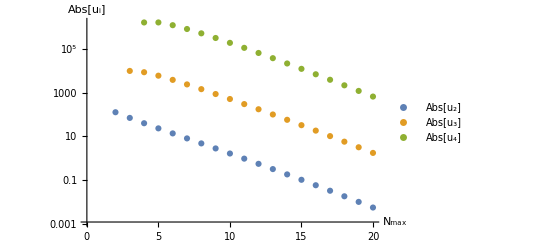

```mathematica
ListLogPlot[{-K2firstinteractingpoint, -K3firstinteractingpoint, -K4firstinteractingpoint},AxesLabel->{Style[HoldForm[Subscript[N, max]],14],Style[HoldForm[Abs[Subscript[u, i]]],14]}, PlotLegends->{Abs[Subscript[u, 2]], Abs[Subscript[u, 3]], Abs[Subscript[u, 4]]}, AxesStyle->Directive[Black, 12]]
```

```mathematica
Export["Myversionoffigure3paper2.png",%76,"PNG"]
```

Myversionoffigure3paper2.png

```mathematica
K2secondinteractingpoint = Table[{-Nmax+1, Reverse[Sort[Klist[Nmax], Less]][[3]]},{Nmax,4,21}]
```

{{-3,π^2 Root-20.4Root[8053063680+1541406720 #1+58245120 #1^2+98432 #1^3+63 #1^4&,1]-20.36784540760949},{-4,π^2 Root-13.7Root[27707693019955200+10047646492262400 #1+884439798251520 #1^2+22588067676160 #1^3+58610647040 #1^4+72309888 #1^5+39627 #1^6&,3]-13.698241123468453},{-5,π^2 Root-9.43Root[1815851369755783987200+1133724911195180236800 #1+177140361220293918720 #1^2+10020864794191462400 #1^3+199446176129351680 #1^4+685709362987008 #1^5+1227908333568 #1^6+1262429952 #1^7+607887 #1^8&,3]-9.425629363758834},{-6,π^2 Root-6.59Root[69728692598622105108480000+71807842416992477773824000 #1+17813129545910052716544000 #1^2+1716037832169432180326400 #1^3+71927293312542745559040 #1^4+1208053985333194260480 #1^5+5063908590931148800 #1^6+11711825806688256 #1^7+17150936796672 #1^8+15389647812 #1^9+6625395 #1^10&,5]-6.586335965590332},{-7,π^2 Root-4.66Root[68546093972149474205840179200000+114359518498066564192634142720000 #1+42377409551459171731872153600000 #1^2+6213771556763733689773326336000 #1^3+429617296112453832029503488000 #1^4+14447739116472031498783948800 #1^5+215302599163932942375321600 #1^6+1043487541565201915576320 #1^7+2921490536132279009280 #1^8+5457164492785582080 #1^9+6930565767917568 #1^10+5559534454824 #1^11+2167220853 #1^12&,5]-4.655596229090445},{-8,π^2 Root-3.32Root[1383608938884106685998614131087769600000+3724548638550804822873166689148600320000 #1+1984289744801988729591954279380287488000 #1^2+415769275417219080484257036572295168000 #1^3+42539642619816658038374227468143820800 #1^4+2296411250622915101038899930071040000 #1^5+65201510488970028126817485638860800 #1^6+891548850623812684437133501399040 #1^7+4819055048763858815207520337920 #1^8+15667745106256938703614115840 #1^9+35163185571809340401123328 #1^10+56663197602349559316480 #1^11+64246725910664478720 #1^12+46775965307879808 #1^13+16673565116439 #1^14&,7]-3.31947942056227},{-9,π^2 Root-2.38Root[906761954187088157736051756949680685056000000+3955167118753161400968728658264135932313600000 #1+2951564913359370128385983847362631397539840000 #1^2+848521908654367229994294709413742305607680000 #1^3+120741201728596300739764770791813202051072000 #1^4+9440047083333650427516751391381331640320000 #1^5+419772828878768518445198385500928344064000 #1^6+10424811571454218189268463480220732620800 #1^7+133866231883691890290003137537454899200 #1^8+786750486793446020715564956542566400 #1^9+2885436486722874338485593587056640 #1^10+7492533595644489844957076520960 #1^11+14448753523145427627037163520 #1^12+20751515809990567218118656 #1^13+21373749106768200941568 #1^14+14275513706564791296 #1^15+4689832188260835 #1^16&,7]-2.3820777513344793},{-10,π^2 Root-1.72Root[12167381655211625696228579556422262473701195776000000+86782748193915930138623378549391585177552027648000000 #1+89051275480541130925772533228970615182615746969600000 #1^2+34141623038229661758474641331432219780818738872320000 #1^3+6488823765066314411081651724324874966614203695104000 #1^4+692006685132860657870447100150964530092017975296000 #1^5+43774488709917412527772402219851690596179220889600 #1^6+1663858294424497614817006506826821422640896409600 #1^7+37087549496566513248636587236716193601552384000 #1^8+454612110696945625123781835784234055111802880 #1^9+2852382211946897762076531117631410714705920 #1^10+11551540608548457135995055663252745748480 #1^11+33812022019000944466827074523466039296 #1^12+75235753836448054624553108187906048 #1^13+129097356208103035096348760211456 #1^14+168447320654693672686687617024 #1^15+159456906135231949223755776 #1^16+98493726703257011782656 #1^17+30016201485347065989 #1^18&,9]-1.7173465208095853},{-11,π^2 Root-1.24Root[9967519051949363770350452372621117418456019579699200000000+117614469019070224683974513396782852013563684533043200000000 #1+163760355503030406202580860226331881186486322008476876800000 #1^2+82006049212017511861082466782150552107951841767902412800000 #1^3+20232381600596162426437704651357419169429298154506813440000 #1^4+2829353862076829339761301889630584780145726071400038400000 #1^5+240431025829909197136905997439757193040428512653082624000 #1^6+12796882725585596051624891422371800893427304672264192000 #1^7+427174597319066975853861717153016972255562564003430400 #1^8+8714636836358590064271953618728207226242446707916800 #1^9+103164256703046037103925975660019309083011055616000 #1^10+681820904624116380746591137648422561054950686720 #1^11+2999765117849175855733080186439428301284966400 #1^12+9710033716723514643452813171077791812157440 #1^13+24316392009473490451602090162453567504384 #1^14+48077880631451099508552111802137182208 #1^15+74929670195404741139790355255787520 #1^16+89950170250033422976510379163648 #1^17+78926806711196899709614424064 #1^18+45377446801676035211028864 #1^19+12898736425248974677377 #1^20&,9]-1.242098708621699},{-12,π^2 Root-0.900Root[377241092259889648591004384964686335781001711273658810368000000000+7458326851310971406420786210546467243440953895054707628441600000000 #1+13959043852547055690755102456433681141429164998330743603068928000000 #1^2+8987849305588866243350971441442445619577376479832746848419840000000 #1^3+2818428189509709770148536622992545516370777703063126871218585600000 #1^4+502563808939695389662317781680358120376347014004429869495091200000 #1^5+55224285037373547886698702600481050147418468021153166933360640000 #1^6+3898284963053204578848299483573871952952923224839855517204480000 #1^7+179621592672472939321858402786312388212107139202146677817344000 #1^8+5375385116003268739004470016705665859764333100502091825152000 #1^9+«3»+38210735012623184271553586564574884816628643948134400 #1^13+134789111062175988223572499862198151241036883558400 #1^14+373058294579220278219109263644316781762565898240 #1^15+829288417200851185521740934549298832348282880 #1^16+1488669961101032193544393768937986480668672 #1^17+2135733351286925935269488687398546046976 #1^18+2380107798328316003600128225412382720 #1^19+1948563732419686202100064576856064 #1^20+1048290333249030985970601833088 #1^21+279245623399676129907846135 #1^22&,11]-0.9002321160507263},{-13,π^2 Root-0.653Root[74168616667032384030180190119137051105231184450091511388831744000000000+2488230560883514195753024195492112792053241412486774773992390656000000000 #1+6220978258355259501856443864104027354799578469833383796436614774784000000 #1^2+5088268220948454097314971891438980095641748381944594121251264397312000000 #1^3+1995418605787216610644228769730129219388771121271973095668847319449600000 #1^4+444316962468834606697745333860618007300947197947614173058259170099200000 #1^5+61437685356057052681202454891274923091541999908041698050727812792320000 #1^6+5544986079422597070661652589743261354029022982194402377784497274880000 #1^7+335076490462103158842341228863785942999500127177403345131257462784000 #1^8+«7»+30728674446540729351533656849231274066529285067243520 #1^16+75446761528622445697913291975390743131684555718656 #1^17+152212231007212393285203055695759270711782277120 #1^18+251591728657723039918912914442421969098899456 #1^19+335416528039009191856946985717914834829312 #1^20+349367180464640844938218170195879395328 #1^21+268281088511462233731522702819827712 #1^22+135659396694236804329101281632512 #1^23+34003325196208048787859131379 #1^24&,11]-0.6532156396758635},{-14,π^2 Root-0.474Root[1007079277572965798133953864683271472799094277947610563600290739650560000000000+58022291329925857148975540996463038723729637210863143784670812820209664000000000 #1+193074609765787896424532727625330058273158798717947578283988223001247088640000000 #1^2+198734295414564490656405177798177723724971607149635783929295428726302965760000000 #1^3+96230897635649284982396231057190515229001917282765948347097245879743021056000000 #1^4+26328830199140046754363954266835779423899856704684812508632438149948112896000000 #1^5+4488421744418738017286120902319563866751611967378035565183337910493406822400000 #1^6+504451340209521092802587168049034452214369396418054020062961718976420249600000 #1^7+38601928423320315893035705654798376090762268150963563115534592378719436800000 #1^8+«9»+484973285395820539766542347901336327618047621214167367680 #1^18+1080348652586843294176940929087148143945296970864656384 #1^19+2007122100071716471574299213542841928545430868590592 #1^20+3084977641910488367818205866540636450857576038400 #1^21+3848881553731829633742483051022954488938889216 #1^22+3767101850253509207971556008780136568324096 #1^23+2725265515138102654216628346352825417728 #1^24+1300260533634124252850483173779260832 #1^25+307766320078648696618720359629637 #1^26&,13]-0.4741831240597121},{-15,π^2 Root-0.344Root[230999816372576602912773801665590077344765049098511120636380288698086850560000000000+23109270787525730351969773378836826156186601097391995989579979187414565388288000000000 #1+102190562908872046331260822053323706037419417434773978246785824906245105747230720000000 #1^2+131408953030214182894976493235236621870787906946424559249034492429294713826181120000000 #1^3+77770165416589810751876982633659911616095030394605819784631699256943539472302080000000 #1^4+25811560015825520781757245985490015190038047612750816265265963537240207082389504000000 #1^5+5339315571326140565926170766441956261388557083930799083128257235103877182993203200000 #1^6+732513511058173485852164679578161348831290472010620553634242811659152304740761600000 #1^7+«13»+269503060189786218565215946041689720506534959406896906240 #1^21+465801957863004314152292264441870702023919866050772992 #1^22+670615682110497682095683455413227164221912303796224 #1^23+787282710952859894828323938758193468049949982720 #1^24+727243771470944286924102932020234829288964096 #1^25+497498050826313859125152510917907045486592 #1^26+224714107089789019784205897770144443296 #1^27+50386612217546071474603079927804361 #1^28&,13]-0.3441693088590647},{-16,π^2 Root-0.250Root[10786397825627640927050225004493729307567397108625517671443395752583946634788864000000000000+1892316660120275052228008969922743420174645912965004889058835482100906745749569536000000000000 #1+11122273608594170161114024931696152175548537882765108594245245171975116723416345870336000000000 #1^2+17767109317975088655469262452084560432868492887616851997090738311041415242285440617676800000000 #1^3+12745527642203722914787237572567744076888256338878984083938400983221914989122957984399360000000 #1^4+5078384615408189695870873301875191107913776336944102817666708202968256166568863255756800000000 #1^5+1258586752708883687318397163472197353303269683670407610530031725837846074027671468113920000000 #1^6+«17»+22931550132948702297861656758125483993245441324101952077824 #1^24+31098647567422857577226301056056665898581417944728731648 #1^25+34505904240313068566683108756008930360083892431486976 #1^26+30193540787889516416079525210141518149025896857600 #1^27+19594442084827936290751073963985022011094917120 #1^28+8403762423959177228812671658738537131527040 #1^29+1790110485295447108175114968575673225893 #1^30&,15]-0.24965324619232668},{-17,π^2 Root-0.181Root[98965631506046630611322896425230146146103171167523469656200013765787813732053218754560000000000000+30715982982440498520881890114232657869662660472881022487428157776102609353284720120561664000000000000 #1+240331507284812439170397865365393410138644354307010872608874977377608206436258804814273576960000000000 #1^2+474851022112315902740812215719256918482573116821722254703654150946730532891656676833625112576000000000 #1^3+410120269997196044854564722052819364964400753962125217782600973257311075463811081292077858816000000000 #1^4+194503285223529076756697438894669666987640382989848126511333601881792900671268996645177733939200000000 #1^5+57156322155991594284659126139485848301425709510637662701918113050704108381569002129119216926720000000 #1^6+«19»+231038094612052591183018006841762526319425169437262765319258112 #1^26+296468706008747512495354368536449142040174676723264420577280 #1^27+312046299704816202980039425192809756350319628065624293376 #1^28+259463787193568280324034950672061106212969081306349568 #1^29+160187550070097017141982220725058606520660925128704 #1^30+65405737087408338006311426481613820807791691520 #1^31+13269232717045632229723158277413798800555079 #1^32&,15]-0.18092046785049856},{-18,π^2 Root-0.131Root[303211693533277715240015980650791523603600064648427746520422851775730830014774508045970964480000000000000+167789196915468380289323856267195515589201283983084543990362717850896452906387807460437134409728000000000000 #1+1752168853423604282447748971565327661939175027837367509668378254673245868880560342219808257490288640000000000 #1^2+4268037728375677309223235727222036516679786268291286556037188416694212630115504018850087503816294400000000000 #1^3+4413421915138683896079992629763790672366484312140628801386695050400844227016814536454884326240786841600000000 #1^4+2473667061087532463740795927285269797059877618555548391791290743468364458641453342499691419554912665600000000 #1^5+854516755288978978554299655148691137567342108228882048772417446432318708651880455150016176070181519360000000 #1^6+«21»+808892439696220440994962357446563190505563823311590130605470253056 #1^28+985775015725711241552379002920274687325290240813331679279054848 #1^29+987320524276746387267902591985027974170344407288345612255232 #1^30+782243379625038966133190365752531206973422337789954883584 #1^31+460589804279113864316667059652919733446975871029223424 #1^32+179463086722051499978925437696309361882555277883904 #1^33+34755668815507492191143773454379882593938958625 #1^34&,17]-0.13095016431064335},{-19,π^2 Root-0.0946Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 #1^31+11004408092786726856174412810415395363511994424266004079277244416 #1^32+8327703083106635932455803399929948004314853622214618798620672 #1^33+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,17]-0.09464645496248507},{-20,π^2 Root-0.0683Root[44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 #1^4+6261330730743702716197243529820454851597238604902324544172276014301723661251208597092594089056223736227798508896256000000000 #1^5+«27»+194300316806694894776952441240579511038783029720372172196124756054900736 #1^33+177580004966680398442829671012813076841456308886730433293539059171328 #1^34+128636035084569806253334820169957311036671675652020191909610782720 #1^35+69342832633484196825805144687266347903661885736694910897217536 #1^36+24757799297747699127199424335828812438082918959401431721856 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,19]-0.06829973036806072}}

```mathematica
K2eightinteractingpoint = Table[{-Nmax+1, Reverse[Sort[Klist[Nmax], Less]][[9]]},{Nmax,10,21}]
```

{{-9,π^2 Root-33.2Root[906761954187088157736051756949680685056000000+3955167118753161400968728658264135932313600000 #1+2951564913359370128385983847362631397539840000 #1^2+848521908654367229994294709413742305607680000 #1^3+120741201728596300739764770791813202051072000 #1^4+9440047083333650427516751391381331640320000 #1^5+419772828878768518445198385500928344064000 #1^6+10424811571454218189268463480220732620800 #1^7+133866231883691890290003137537454899200 #1^8+786750486793446020715564956542566400 #1^9+2885436486722874338485593587056640 #1^10+7492533595644489844957076520960 #1^11+14448753523145427627037163520 #1^12+20751515809990567218118656 #1^13+21373749106768200941568 #1^14+14275513706564791296 #1^15+4689832188260835 #1^16&,1]-33.17161826438402},{-10,π^2 Root-28.5Root[12167381655211625696228579556422262473701195776000000+86782748193915930138623378549391585177552027648000000 #1+89051275480541130925772533228970615182615746969600000 #1^2+34141623038229661758474641331432219780818738872320000 #1^3+6488823765066314411081651724324874966614203695104000 #1^4+692006685132860657870447100150964530092017975296000 #1^5+43774488709917412527772402219851690596179220889600 #1^6+1663858294424497614817006506826821422640896409600 #1^7+37087549496566513248636587236716193601552384000 #1^8+454612110696945625123781835784234055111802880 #1^9+2852382211946897762076531117631410714705920 #1^10+11551540608548457135995055663252745748480 #1^11+33812022019000944466827074523466039296 #1^12+75235753836448054624553108187906048 #1^13+129097356208103035096348760211456 #1^14+168447320654693672686687617024 #1^15+159456906135231949223755776 #1^16+98493726703257011782656 #1^17+30016201485347065989 #1^18&,3]-28.517295351146043},{-11,π^2 Root-24.8Root[9967519051949363770350452372621117418456019579699200000000+117614469019070224683974513396782852013563684533043200000000 #1+163760355503030406202580860226331881186486322008476876800000 #1^2+82006049212017511861082466782150552107951841767902412800000 #1^3+20232381600596162426437704651357419169429298154506813440000 #1^4+2829353862076829339761301889630584780145726071400038400000 #1^5+240431025829909197136905997439757193040428512653082624000 #1^6+12796882725585596051624891422371800893427304672264192000 #1^7+427174597319066975853861717153016972255562564003430400 #1^8+8714636836358590064271953618728207226242446707916800 #1^9+103164256703046037103925975660019309083011055616000 #1^10+681820904624116380746591137648422561054950686720 #1^11+2999765117849175855733080186439428301284966400 #1^12+9710033716723514643452813171077791812157440 #1^13+24316392009473490451602090162453567504384 #1^14+48077880631451099508552111802137182208 #1^15+74929670195404741139790355255787520 #1^16+89950170250033422976510379163648 #1^17+78926806711196899709614424064 #1^18+45377446801676035211028864 #1^19+12898736425248974677377 #1^20&,3]-24.785064927258524},{-12,π^2 Root-21.7Root[377241092259889648591004384964686335781001711273658810368000000000+7458326851310971406420786210546467243440953895054707628441600000000 #1+13959043852547055690755102456433681141429164998330743603068928000000 #1^2+8987849305588866243350971441442445619577376479832746848419840000000 #1^3+2818428189509709770148536622992545516370777703063126871218585600000 #1^4+502563808939695389662317781680358120376347014004429869495091200000 #1^5+55224285037373547886698702600481050147418468021153166933360640000 #1^6+3898284963053204578848299483573871952952923224839855517204480000 #1^7+179621592672472939321858402786312388212107139202146677817344000 #1^8+5375385116003268739004470016705665859764333100502091825152000 #1^9+«3»+38210735012623184271553586564574884816628643948134400 #1^13+134789111062175988223572499862198151241036883558400 #1^14+373058294579220278219109263644316781762565898240 #1^15+829288417200851185521740934549298832348282880 #1^16+1488669961101032193544393768937986480668672 #1^17+2135733351286925935269488687398546046976 #1^18+2380107798328316003600128225412382720 #1^19+1948563732419686202100064576856064 #1^20+1048290333249030985970601833088 #1^21+279245623399676129907846135 #1^22&,5]-21.6944367680182},{-13,π^2 Root-19.1Root[74168616667032384030180190119137051105231184450091511388831744000000000+2488230560883514195753024195492112792053241412486774773992390656000000000 #1+6220978258355259501856443864104027354799578469833383796436614774784000000 #1^2+5088268220948454097314971891438980095641748381944594121251264397312000000 #1^3+1995418605787216610644228769730129219388771121271973095668847319449600000 #1^4+444316962468834606697745333860618007300947197947614173058259170099200000 #1^5+61437685356057052681202454891274923091541999908041698050727812792320000 #1^6+5544986079422597070661652589743261354029022982194402377784497274880000 #1^7+335076490462103158842341228863785942999500127177403345131257462784000 #1^8+«7»+30728674446540729351533656849231274066529285067243520 #1^16+75446761528622445697913291975390743131684555718656 #1^17+152212231007212393285203055695759270711782277120 #1^18+251591728657723039918912914442421969098899456 #1^19+335416528039009191856946985717914834829312 #1^20+349367180464640844938218170195879395328 #1^21+268281088511462233731522702819827712 #1^22+135659396694236804329101281632512 #1^23+34003325196208048787859131379 #1^24&,5]-19.087487389826382},{-14,π^2 Root-16.9Root[1007079277572965798133953864683271472799094277947610563600290739650560000000000+58022291329925857148975540996463038723729637210863143784670812820209664000000000 #1+193074609765787896424532727625330058273158798717947578283988223001247088640000000 #1^2+198734295414564490656405177798177723724971607149635783929295428726302965760000000 #1^3+96230897635649284982396231057190515229001917282765948347097245879743021056000000 #1^4+26328830199140046754363954266835779423899856704684812508632438149948112896000000 #1^5+4488421744418738017286120902319563866751611967378035565183337910493406822400000 #1^6+504451340209521092802587168049034452214369396418054020062961718976420249600000 #1^7+38601928423320315893035705654798376090762268150963563115534592378719436800000 #1^8+«9»+484973285395820539766542347901336327618047621214167367680 #1^18+1080348652586843294176940929087148143945296970864656384 #1^19+2007122100071716471574299213542841928545430868590592 #1^20+3084977641910488367818205866540636450857576038400 #1^21+3848881553731829633742483051022954488938889216 #1^22+3767101850253509207971556008780136568324096 #1^23+2725265515138102654216628346352825417728 #1^24+1300260533634124252850483173779260832 #1^25+307766320078648696618720359629637 #1^26&,7]-16.862232052305824},{-15,π^2 Root-14.9Root[230999816372576602912773801665590077344765049098511120636380288698086850560000000000+23109270787525730351969773378836826156186601097391995989579979187414565388288000000000 #1+102190562908872046331260822053323706037419417434773978246785824906245105747230720000000 #1^2+131408953030214182894976493235236621870787906946424559249034492429294713826181120000000 #1^3+77770165416589810751876982633659911616095030394605819784631699256943539472302080000000 #1^4+25811560015825520781757245985490015190038047612750816265265963537240207082389504000000 #1^5+5339315571326140565926170766441956261388557083930799083128257235103877182993203200000 #1^6+732513511058173485852164679578161348831290472010620553634242811659152304740761600000 #1^7+«13»+269503060189786218565215946041689720506534959406896906240 #1^21+465801957863004314152292264441870702023919866050772992 #1^22+670615682110497682095683455413227164221912303796224 #1^23+787282710952859894828323938758193468049949982720 #1^24+727243771470944286924102932020234829288964096 #1^25+497498050826313859125152510917907045486592 #1^26+224714107089789019784205897770144443296 #1^27+50386612217546071474603079927804361 #1^28&,7]-14.9466312485123},{-16,π^2 Root-13.3Root[10786397825627640927050225004493729307567397108625517671443395752583946634788864000000000000+1892316660120275052228008969922743420174645912965004889058835482100906745749569536000000000000 #1+11122273608594170161114024931696152175548537882765108594245245171975116723416345870336000000000 #1^2+17767109317975088655469262452084560432868492887616851997090738311041415242285440617676800000000 #1^3+12745527642203722914787237572567744076888256338878984083938400983221914989122957984399360000000 #1^4+5078384615408189695870873301875191107913776336944102817666708202968256166568863255756800000000 #1^5+1258586752708883687318397163472197353303269683670407610530031725837846074027671468113920000000 #1^6+«17»+22931550132948702297861656758125483993245441324101952077824 #1^24+31098647567422857577226301056056665898581417944728731648 #1^25+34505904240313068566683108756008930360083892431486976 #1^26+30193540787889516416079525210141518149025896857600 #1^27+19594442084827936290751073963985022011094917120 #1^28+8403762423959177228812671658738537131527040 #1^29+1790110485295447108175114968575673225893 #1^30&,9]-13.28680136993623},{-17,π^2 Root-11.8Root[98965631506046630611322896425230146146103171167523469656200013765787813732053218754560000000000000+30715982982440498520881890114232657869662660472881022487428157776102609353284720120561664000000000000 #1+240331507284812439170397865365393410138644354307010872608874977377608206436258804814273576960000000000 #1^2+474851022112315902740812215719256918482573116821722254703654150946730532891656676833625112576000000000 #1^3+410120269997196044854564722052819364964400753962125217782600973257311075463811081292077858816000000000 #1^4+194503285223529076756697438894669666987640382989848126511333601881792900671268996645177733939200000000 #1^5+57156322155991594284659126139485848301425709510637662701918113050704108381569002129119216926720000000 #1^6+«19»+231038094612052591183018006841762526319425169437262765319258112 #1^26+296468706008747512495354368536449142040174676723264420577280 #1^27+312046299704816202980039425192809756350319628065624293376 #1^28+259463787193568280324034950672061106212969081306349568 #1^29+160187550070097017141982220725058606520660925128704 #1^30+65405737087408338006311426481613820807791691520 #1^31+13269232717045632229723158277413798800555079 #1^32&,9]-11.840937263046657},{-18,π^2 Root-10.6Root[303211693533277715240015980650791523603600064648427746520422851775730830014774508045970964480000000000000+167789196915468380289323856267195515589201283983084543990362717850896452906387807460437134409728000000000000 #1+1752168853423604282447748971565327661939175027837367509668378254673245868880560342219808257490288640000000000 #1^2+4268037728375677309223235727222036516679786268291286556037188416694212630115504018850087503816294400000000000 #1^3+4413421915138683896079992629763790672366484312140628801386695050400844227016814536454884326240786841600000000 #1^4+2473667061087532463740795927285269797059877618555548391791290743468364458641453342499691419554912665600000000 #1^5+854516755288978978554299655148691137567342108228882048772417446432318708651880455150016176070181519360000000 #1^6+«21»+808892439696220440994962357446563190505563823311590130605470253056 #1^28+985775015725711241552379002920274687325290240813331679279054848 #1^29+987320524276746387267902591985027974170344407288345612255232 #1^30+782243379625038966133190365752531206973422337789954883584 #1^31+460589804279113864316667059652919733446975871029223424 #1^32+179463086722051499978925437696309361882555277883904 #1^33+34755668815507492191143773454379882593938958625 #1^34&,11]-10.575802226259677},{-19,π^2 Root-9.46Root[3129726843715009914490225750999018043314471579295899325364083042200951568946101290089868617685401600000000000000+3109154703760771993651120907787788800435975614996606791420433433819530607603390698122474834635165532160000000000000 #1+43477228580926726368756485373265914501147530608041255442910186545958120092812987351372572359616517636096000000000000 #1^2+130254075158903139229809908877346297185612775259532567995976519751072320883542478277971971679932247336550400000000000 #1^3+160522385520017313069981608757870912192652499494837086211220764823248956539916604979176667621216874506747904000000000 #1^4+105693128001384825590363865927838313345881842462662648412043568452850730784801418001027699572816991272042496000000000 #1^5+«25»+11515378207672028166525745358602818847929538657482581210945248296960 #1^31+11004408092786726856174412810415395363511994424266004079277244416 #1^32+8327703083106635932455803399929948004314853622214618798620672 #1^33+4686964176177645777717434292825266998915571951155800711168 #1^34+1746445407079324895818147792248079215933090269594764416 #1^35+323542734687338607500968906627220586401462375273955 #1^36&,11]-9.464507221996433},{-20,π^2 Root-8.49Root[44816486586890955411692868507617554757334600258430828713872729356429421301905695171191524095705759717785600000000000000+80413280782671613488432782509282934365090448343427519332882083625204287011834237506050223123379535902157045760000000000000 #1+1511516852388938177867287828227528503545674470227032196986171144472295819144021498845081398747091920397970649907200000000000 #1^2+5560586679540580472924013844541401270775714934674421518900126918733778013191307879839063863545984157616542559764480000000000 #1^3+8136088898126054898521915713103269944666766553977984300273700538438756178982232715990903194454595351063399566934016000000000 #1^4+6261330730743702716197243529820454851597238604902324544172276014301723661251208597092594089056223736227798508896256000000000 #1^5+«27»+194300316806694894776952441240579511038783029720372172196124756054900736 #1^33+177580004966680398442829671012813076841456308886730433293539059171328 #1^34+128636035084569806253334820169957311036671675652020191909610782720 #1^35+69342832633484196825805144687266347903661885736694910897217536 #1^36+24757799297747699127199424335828812438082918959401431721856 #1^37+4395835765681924232584927425756783654363819811319728551 #1^38&,13]-8.485009146885204}}

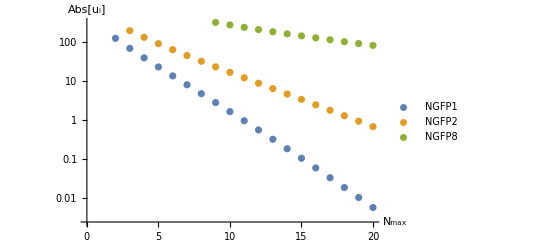

```mathematica
ListLogPlot[{-K2firstinteractingpoint, -K2secondinteractingpoint, -K2eightinteractingpoint},AxesLabel->{Style[HoldForm[Subscript[N, max]], 14],Style[HoldForm[Abs[Subscript[u, i]]], 14]}, PlotLegends->{NGFP1, NGFP2, NGFP8}, AxesStyle->Directive[Black, 12]]
```

```mathematica
Export["Myversionoffigure4paper2N20NGFP128.png",%75,"PNG"]
```

Myversionoffigure4paper2N20NGFP128.png

#### Stability coefficients

These can be derived from the beta-functions. We set beta to zero in our earlier calculations, but to derive the critical exponents, we need to look at the function before doing this.

```mathematica
ClearAll@Betafunlit
```

```mathematica
Betafunlit[1] = {β[1]-> 1}
```

{β[1]→1}

```mathematica
Betafunlit[n_/;n>=2]:=Betafunlit[n]= Module[{ PreviousSol = Betafunlit[n-1], B}, B =Distribute[1/(16(π)^2)1/(n!)Sum[(-1)^l l!(Qcombi[l+1])Expand@BellY[n, l, Table[(m+1)!(1+2m x^2)K[m+1], {m, 1, n-l+1}]]/. x^(i_.):>  xvaluecompensated[i], {l,1,n}]];B = Collect[B, {K[i]}, Simplify];
B = (4(n-1)+n ηϕ)K[n]+B;
B = Simplify[B]/.Qcombi[i_]:>  Qcombilit[i]//Simplify;
Join[PreviousSol, {β[n]-> B}]]
```

```mathematica
Betafunlit[20]
```

{β[1]→1,β[2]→(128 π^2 (2+ηϕ) K[2]-(-10+ηϕ) K[2]^2+(-8+ηϕ) K[3])/(64 π^2),β[3]→(37 (-12+ηϕ) 1^3+3+1)/(960 π^2),14,β[18]→1/(1862340480 1),β[19]→(308704030224054660 (-44+ηϕ) K[2]^19-1+24+12597 (12+11 1))/(620780160 π^2),β[20]→1/(28555887360 π^2)(-72154079992430719920 (-46+ηϕ) K[2]^20+27+7429 (-10147988126430 (-26+ηϕ) K[3]^10+11+143 (14+6 (-4084020 (-14+ηϕ) K[6]^4+1+1+7 (1)))))}
 |  |  |  |

```mathematica
FPLitim[20][[2]]
```

K[3]→32 π^2 K[2]+(5 K[2]^2)/2+K[2]^3/(512 π^2)

```mathematica
FPLitim[1]
```

{ηϕ→(2 K[2])/(32 π^2+K[2]/4)}

```mathematica
D[β[2]/.Betafunlit[20]/.FPLitim[1], K[2]]/. K[2]-> -127.62/.K[3]->0
```

-4.40407

```mathematica
D[β[3]/.Betafunlit[20]/.FPLitim[1], K[2]]/.K[4]-> 0
```

1/(960 π^2)(37 K[2]^3 (2/(32 π^2+K[2]/4)-K[2]/(2 (32 π^2+K[2]/4)^2))+111 K[2]^2 (-12+(2 K[2])/(32 π^2+K[2]/4))+960 π^2 (6/(32 π^2+K[2]/4)-(3 K[2])/(2 (32 π^2+K[2]/4)^2)) K[3]-63 K[2] (2/(32 π^2+K[2]/4)-K[2]/(2 (32 π^2+K[2]/4)^2)) K[3]-63 (-10+(2 K[2])/(32 π^2+K[2]/4)) K[3])

```mathematica
Solve[K[3]==0/. K[3]->32 π^2 K[2]+(5 K[2]^2)/2+K[2]^3/(512 π^2)]
```

{{K[2]→0},{K[2]→128 (-5-2 √6) π^2},{K[2]→128 (-5+2 √6) π^2}}

```mathematica
Betafunlit[20][[2]]
```

β[2]→(128 π^2 (2+ηϕ) K[2]-(-10+ηϕ) K[2]^2+(-8+ηϕ) K[3])/(64 π^2)

```mathematica
Betafunlit[20][[3]]
```

β[3]→(37 (-12+ηϕ) K[2]^3+960 π^2 (8+3 ηϕ) K[3]-63 (-10+ηϕ) K[2] K[3]+25 (-8+ηϕ) K[4])/(960 π^2)

```mathematica
D[%45, K[2]]
```

0→(128 π^2 (2+ηϕ)-2 (-10+ηϕ) K[2])/(64 π^2)

```mathematica
N[Reverse[Sort[Klistreals[6], Less]][[2]]]
```

-23.3201

```mathematica
StabMat[X_]:= Table[Table[D[β[x]/. Betafunlit[20][[x]]/.FPLitim[1], K[n]], {n, 2, X}]/.K[X+1]-> 0, {x,2, X }]
```

```mathematica
Stabilitymatrixlitim[y_] := StabMat[y]/.FPLitim[20]/. K[2]-> N[Reverse[Sort[Klistreals[y+1], Less]][[2]]]
```

```mathematica
MatrixForm[StabMat[3]]
```

((128 π^2 K[2] (2/(32 π^2+K[2]/4)-K[2]/(2 (32 π^2+K[2]/4)^2))-K[2]^2 (2/(32 π^2+K[2]/4)-K[2]/(2 (32 π^2+K[2]/4)^2))-2 K[2] (-10+(2 K[2])/(32 π^2+K[2]/4))+128 π^2 (2+(2 K[2])/(32 π^2+K[2]/4))+(2/(32 π^2+K[2]/4)-K[2]/(2 (32 π^2+K[2]/4)^2)) K[3])/(64 π^2) | (-8+(2 K[2])/(32 π^2+K[2]/4))/(64 π^2)
(37 K[2]^3 (2/(32 π^2+K[2]/4)-K[2]/(2 (32 π^2+K[2]/4)^2))+111 K[2]^2 (-12+(2 K[2])/(32 π^2+K[2]/4))+960 π^2 (6/(32 π^2+K[2]/4)-(3 K[2])/(2 (32 π^2+K[2]/4)^2)) K[3]-63 K[2] (2/(32 π^2+K[2]/4)-K[2]/(2 (32 π^2+K[2]/4)^2)) K[3]-63 (-10+(2 K[2])/(32 π^2+K[2]/4)) K[3])/(960 π^2) | (-63 K[2] (-10+(2 K[2])/(32 π^2+K[2]/4))+960 π^2 (8+(6 K[2])/(32 π^2+K[2]/4)))/(960 π^2))

```mathematica
EV[x_]:= N[Eigenvalues[Stabilitymatrixlitim[x]]]
```

```mathematica
EV[4]
```

{10.9198,5.46782,-4.11851}

```mathematica
θ
```

```mathematica
Table[-EV[X], {X, 2, 20}]
```

{{4.40408},{-5.47655,4.21042},{-10.9198,-5.46782,4.11851},{-15.3619,-11.7637,-5.31849,4.069},{-18.0848-0.814766 ⅈ,-18.0848+0.814766 ⅈ,-12.0171+0. ⅈ,-5.11802+0. ⅈ,4.04077+0. ⅈ},{-23.2456+0. ⅈ,-19.3696-2.9127 ⅈ,-19.3696+2.9127 ⅈ,-11.741+0. ⅈ,-4.91515+0. ⅈ,4.02422+0. ⅈ},{-28.3266+0. ⅈ,-21.3912-4.96441 ⅈ,-21.3912+4.96441 ⅈ,-21.0525+0. ⅈ,-11.2864+0. ⅈ,-4.73047+0. ⅈ,4.01439+0. ⅈ},{-32.0446+0. ⅈ,-29.5298+0. ⅈ,-22.6395-7.70388 ⅈ,-22.6395+7.70388 ⅈ,-19.4837+0. ⅈ,-10.8062+0. ⅈ,-4.57117+0. ⅈ,4.00852+0. ⅈ},{-35.1155-1.58858 ⅈ,-35.1155+1.58858 ⅈ,-28.933+0. ⅈ,-23.3736-10.2764 ⅈ,-23.3736+10.2764 ⅈ,-18.4151+0. ⅈ,-10.3535+0. ⅈ,-4.43843+0. ⅈ,4.00501+0. ⅈ},{-39.8389+0. ⅈ,-36.845-3.53631 ⅈ,-36.845+3.53631 ⅈ,-27.4703+0. ⅈ,-23.7669-12.7546 ⅈ,-23.7669+12.7546 ⅈ,-17.5111+0. ⅈ,-9.94669+0. ⅈ,-4.33068+0. ⅈ,4.00293+0. ⅈ},{-44.6996+0. ⅈ,-39.4304-5.46006 ⅈ,-39.4304+5.46006 ⅈ,-37.4677+0. ⅈ,-23.8468-15.1031 ⅈ,-23.8468+15.1031 ⅈ,-26.0259+0. ⅈ,-16.7184+0. ⅈ,-9.59054+0. ⅈ,-4.24517+0. ⅈ,4.0017+0. ⅈ},{-48.0042+0. ⅈ,-46.4201+0. ⅈ,-41.3845-8.03967 ⅈ,-41.3845+8.03967 ⅈ,-35.3105+0. ⅈ,-23.6717-17.281 ⅈ,-23.6717+17.281 ⅈ,-24.7382+0. ⅈ,-16.0199+0. ⅈ,-9.2843+0. ⅈ,-4.17872+0. ⅈ,4.00098+0. ⅈ},{-51.4714-1.73207 ⅈ,-51.4714+1.73207 ⅈ,-45.2691+0. ⅈ,-43.0493-10.5259 ⅈ,-43.0493+10.5259 ⅈ,-33.5704+0. ⅈ,-23.3006-19.2713 ⅈ,-23.3006+19.2713 ⅈ,-23.6061+0. ⅈ,-15.4057+0. ⅈ,-9.02481+0. ⅈ,-4.12811+0. ⅈ,4.00056+0. ⅈ},{-55.9949+0. ⅈ,-53.4818-3.5761 ⅈ,-53.4818+3.5761 ⅈ,-44.4906-13.1075 ⅈ,-44.4906+13.1075 ⅈ,-43.1555+0. ⅈ,-32.0311+0. ⅈ,-22.7843-21.0709 ⅈ,-22.7843+21.0709 ⅈ,-22.6098+0. ⅈ,-14.8676+0. ⅈ,-8.80786+0. ⅈ,-4.09032+0. ⅈ,4.00032+0. ⅈ},{-60.7864+0. ⅈ,-56.4465-5.36183 ⅈ,-56.4465+5.36183 ⅈ,-53.3997+0. ⅈ,-45.6582-15.7195 ⅈ,-45.6582+15.7195 ⅈ,-41.1693+0. ⅈ,-22.1649-22.6853 ⅈ,-22.1649+22.6853 ⅈ,-30.6572+0. ⅈ,-21.7312+0. ⅈ,-14.3984+0. ⅈ,-8.62887+0. ⅈ,-4.06266+0. ⅈ,4.00018+0. ⅈ},{-63.9756+0. ⅈ,-62.7328+0. ⅈ,-58.777-7.77595 ⅈ,-58.777+7.77595 ⅈ,-50.8956+0. ⅈ,-46.5857-18.3206 ⅈ,-46.5857+18.3206 ⅈ,-39.3983+0. ⅈ,-21.4768-24.1251 ⅈ,-21.4768+24.1251 ⅈ,-29.4299+0. ⅈ,-20.9552+0. ⅈ,-13.9913+0. ⅈ,-8.48318+0. ⅈ,-4.04279+0. ⅈ,4.0001+0. ⅈ},{-67.6821-1.76979 ⅈ,-67.6821+1.76979 ⅈ,-60.9708-10.1044 ⅈ,-60.9708+10.1044 ⅈ,-61.1463+0. ⅈ,-47.2921-20.8906 ⅈ,-47.2921+20.8906 ⅈ,-48.7446+0. ⅈ,-37.8151+0. ⅈ,-20.7471-25.4042 ⅈ,-20.7471+25.4042 ⅈ,-28.333+0. ⅈ,-20.2695+0. ⅈ,-13.6401+0. ⅈ,-8.36625+0. ⅈ,-4.02877+0. ⅈ,4.00006+0. ⅈ},{-72.0044+0. ⅈ,-69.8791-3.465 ⅈ,-69.8791+3.465 ⅈ,-62.9858-12.6178 ⅈ,-62.9858+12.6178 ⅈ,-58.6592+0. ⅈ,-47.7954-23.4085 ⅈ,-47.7954+23.4085 ⅈ,-46.806+0. ⅈ,-36.3931+0. ⅈ,-19.9967-26.5375 ⅈ,-19.9967+26.5375 ⅈ,-27.3517+0. ⅈ,-19.6638+0. ⅈ,-13.3392+0. ⅈ,-8.27378+0. ⅈ,-4.01907+0. ⅈ,4.00003+0. ⅈ},{-76.832+0. ⅈ,-73.1293-5.19839 ⅈ,-73.1293+5.19839 ⅈ,-69.1277+0. ⅈ,-64.7673-15.1954 ⅈ,-64.7673+15.1954 ⅈ,-56.3553+0. ⅈ,-48.1154-25.8581 ⅈ,-48.1154+25.8581 ⅈ,-45.0543+0. ⅈ,-35.1119+0. ⅈ,-19.2412-27.5402 ⅈ,-19.2412+27.5402 ⅈ,-26.4731+0. ⅈ,-19.1296+0. ⅈ,-13.0833+0. ⅈ,-8.20178+0. ⅈ,-4.01247+0. ⅈ,4.00002+0. ⅈ}}

```mathematica
EVList= Table[-Re[EV[X]], {X, 2, 20}]
```

{{4.40408},{-5.47655,4.21042},{-10.9198,-5.46782,4.11851},{-15.3619,-11.7637,-5.31849,4.069},{-18.0848,-18.0848,-12.0171,-5.11802,4.04077},{-23.2456,-19.3696,-19.3696,-11.741,-4.91515,4.02422},{-28.3266,-21.3912,-21.3912,-21.0525,-11.2864,-4.73047,4.01439},{-32.0446,-29.5298,-22.6395,-22.6395,-19.4837,-10.8062,-4.57117,4.00852},{-35.1155,-35.1155,-28.933,-23.3736,-23.3736,-18.4151,-10.3535,-4.43843,4.00501},{-39.8389,-36.845,-36.845,-27.4703,-23.7669,-23.7669,-17.5111,-9.94669,-4.33068,4.00293},{-44.6996,-39.4304,-39.4304,-37.4677,-23.8468,-23.8468,-26.0259,-16.7184,-9.59054,-4.24517,4.0017},{-48.0042,-46.4201,-41.3845,-41.3845,-35.3105,-23.6717,-23.6717,-24.7382,-16.0199,-9.2843,-4.17872,4.00098},{-51.4714,-51.4714,-45.2691,-43.0493,-43.0493,-33.5704,-23.3006,-23.3006,-23.6061,-15.4057,-9.02481,-4.12811,4.00056},{-55.9949,-53.4818,-53.4818,-44.4906,-44.4906,-43.1555,-32.0311,-22.7843,-22.7843,-22.6098,-14.8676,-8.80786,-4.09032,4.00032},{-60.7864,-56.4465,-56.4465,-53.3997,-45.6582,-45.6582,-41.1693,-22.1649,-22.1649,-30.6572,-21.7312,-14.3984,-8.62887,-4.06266,4.00018},{-63.9756,-62.7328,-58.777,-58.777,-50.8956,-46.5857,-46.5857,-39.3983,-21.4768,-21.4768,-29.4299,-20.9552,-13.9913,-8.48318,-4.04279,4.0001},{-67.6821,-67.6821,-60.9708,-60.9708,-61.1463,-47.2921,-47.2921,-48.7446,-37.8151,-20.7471,-20.7471,-28.333,-20.2695,-13.6401,-8.36625,-4.02877,4.00006},{-72.0044,-69.8791,-69.8791,-62.9858,-62.9858,-58.6592,-47.7954,-47.7954,-46.806,-36.3931,-19.9967,-19.9967,-27.3517,-19.6638,-13.3392,-8.27378,-4.01907,4.00003},{-76.832,-73.1293,-73.1293,-69.1277,-64.7673,-64.7673,-56.3553,-48.1154,-48.1154,-45.0543,-35.1119,-19.2412,-19.2412,-26.4731,-19.1296,-13.0833,-8.20178,-4.01247,4.00002}}

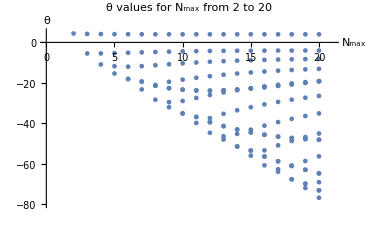

```mathematica
ListPlot[#, PlotRange->{{0,21}, {-80,5}}, PlotLabel->"θ values for N_max from 2 to 20", AxesLabel->{Subscript[N, max], θ}, AxesStyle->Directive[Black, 12]]&@Flatten[#,1]&@(Tuples/@MapIndexed[{#2,#1}&,Prepend[EVList,{}]])
```

```mathematica
Stabilitymatrixlitim[20]
```

(1)
 |  |  |  |

```mathematica
N[Eigenvalues[%]]
```

$Aborted

Now try to find a general formula for K_n in terms of K_2. (Around the GFP K_2=0)

```mathematica
Drop[FPLitim[20],1];
```

```mathematica
Table[K[n], {n, 3, 21}]
```

{K[3],K[4],K[5],K[6],K[7],K[8],K[9],K[10],K[11],K[12],K[13],K[14],K[15],K[16],K[17],K[18],K[19],K[20],K[21]}

```mathematica
%/. FPLitim[20];
```

```mathematica
FindSequenceFunction[Table[K[n], {n, 3, 21}]/.FPLitim[20], K[2] ]
```

FindSequenceFunction[{32 π^2 K[2]+(5 K[2]^2)/2+K[2]^3/(512 π^2),6144/5 π^4 K[2]+1176/5 π^2 K[2]^2+(711 K[2]^3)/80+(769 K[2]^4)/(51200 π^2)+(63 K[2]^5)/(6553600 π^4),1179648/25 π^6 K[2]+427776/25 π^4 K[2]^2+188274/125 π^2 K[2]^3+(153869 K[2]^4)/4000+(357731 K[2]^5)/(3584000 π^2)+(80703 K[2]^6)/(655360000 π^4)+(5661 K[2]^7)/(83886080000 π^6),301989888/175 π^8 K[2]+26935296/25 π^6 K[2]^2+147298944/875 π^4 K[2]^3+238078/25 π^2 K[2]^4+(148598981 K[2]^5)/784000+(40871463 K[2]^6)/(62720000 π^2)+(10706511 K[2]^7)/(9175040000 π^4)+(704481 K[2]^8)/(587202560000 π^6)+(86841 K[2]^9)/(150323855360000 π^8),14495514624/245 π^10 K[2]+(74638688256 π^8 K[2]^2)/1225+(18515367936 π^6 K[2]^3)/1225+(8918441808 π^4 K[2]^4)/6125+(104667987489 π^2 K[2]^5)/1715000+(225017589579 K[2]^6)/219520000+(24146597819 K[2]^7)/(5619712000 π^2)+(178708279521 K[2]^8)/(17983078400000 π^4)+(4785417633 K[2]^9)/(328833433600000 π^6)+(549630279 K[2]^10)/(42090679500800000 π^8)+(189297 K[2]^11)/(33672543600640000 π^10),463856467968/245 π^12 K[2]+(3869396434944 π^10 K[2]^2)/1225+286771052544/245 π^8 K[2]^3+(1051226247936 π^6 K[2]^4)/6125+(508769081516 π^4 K[2]^5)/42875+(2737529620631 π^2 K[2]^6)/6860000+(5221775285801 K[2]^7)/878080000+(12147793797371 K[2]^8)/(421478400000 π^2)+(5804480187361 K[2]^9)/(71932313600000 π^4)+(198261242559 K[2]^10)/(1315333734400000 π^6)+(80572983723 K[2]^11)/(420906795008000000 π^8)+(33092466993 K[2]^12)/(215504279044096000000 π^10)+(14742999 K[2]^13)/(246290604621824000000 π^12),9895604649984/175 π^14 K[2]+(932332173262848 π^12 K[2]^2)/6125+(2483545457033216 π^10 K[2]^3)/30625+(74339798253568 π^8 K[2]^4)/4375+(798641955760384 π^6 K[2]^5)/459375+(12071631839251 π^4 K[2]^6)/128625+(1096791184624139 π^2 K[2]^7)/411600000+(56239662587537 K[2]^8)/1543500000+(1521842025834309 K[2]^9)/(7727104000000 π^2)+(4145376338289283 K[2]^10)/(6473908224000000 π^4)+(496185886642717 K[2]^11)/(345275105280000000 π^6)+(3898862643493 K[2]^12)/(1683627180032000000 π^8)+(565845447981 K[2]^13)/(215504279044096000000 π^10)+(527326448727 K[2]^14)/(275845477176442880000000 π^12)+(3437139789 K[2]^15)/(5044031582654955520000000 π^14),(15199648742375424 π^16 K[2])/9625+(2320454968991023104 π^14 K[2]^2)/336875+(1236894361199837184 π^12 K[2]^3)/240625+(2489094417653170176 π^10 K[2]^4)/1684375+(1770939843380068352 π^8 K[2]^5)/8421875+(17622106673753088 π^6 K[2]^6)/1071875+(86196707011505061 π^4 K[2]^7)/117906250+(1027509395774789891 π^2 K[2]^8)/56595000000+(74310686428542488563 K[2]^9)/318743040000000+(873468505073133917 K[2]^10)/(637486080000000 π^2)+(65607229924418660141 K[2]^11)/(13055714918400000000 π^4)+(660792204421268459 K[2]^12)/(50640348774400000000 π^6)+(81554244431274337 K[2]^13)/(3240982321561600000000 π^8)+(60846454565397 K[2]^14)/(1683627180032000000000 π^10)+(5647403101211667 K[2]^15)/(151715012447043584000000000 π^12)+(5486395652919 K[2]^16)/(220676381741154304000000000 π^14)+(52733256741 K[2]^17)/(6456360425798343065600000000 π^16),(4377498837804122112 π^18 K[2])/105875+(218554799288569823232 π^16 K[2]^2)/741125+(1121339439236914348032 π^14 K[2]^3)/3705625+(2149567663446448668672 π^12 K[2]^4)/18528125+(14298845732230961823744 π^10 K[2]^5)/648484375+(1524913789407898310656 π^8 K[2]^6)/648484375+(482309802001532860128 π^6 K[2]^7)/3242421875+(2993058801190084601 π^4 K[2]^8)/529375000+(9665961955851223541753 π^2 K[2]^9)/76697544000000+(379147260042960827709197 K[2]^10)/245432140800000000+(7916951016836697891045169 K[2]^11)/(816798164582400000000 π^2)+(157843524350806024559533 K[2]^12)/(4021160194867200000000 π^4)+(197127274887890685295291 K[2]^13)/(1715695016476672000000000 π^6)+(729153720925919573587 K[2]^14)/(2852064442974208000000000 π^8)+(40037056996264418073 K[2]^15)/(91266062175174656000000000 π^10)+(26747233329308921829 K[2]^16)/(46728223833689423872000000000 π^12)+(28936769127020199 K[2]^17)/(53403684381359341568000000000 π^14)+(415970522912799 K[2]^18)/(1242849381966181040128000000000 π^16)+(129810455714619 K[2]^19)/(1272677767133369385091072000000000 π^18),(280159925619463815168 π^20 K[2])/275275+(23140766026424433770496 π^18 K[2]^2)/1926925+(4027501997315133316005888 π^16 K[2]^3)/240865625+(183349696894691828563968 π^14 K[2]^4)/21896875+(1583249497262939726413824 π^12 K[2]^5)/766390625+(487093460864549257412608 π^10 K[2]^6)/1686059375+(147828275313033030045696 π^8 K[2]^7)/6021640625+(55076867360343571531076 π^6 K[2]^8)/42151484375+(67952027899515145129861627 π^4 K[2]^9)/1557918862500000+(177441935667108374837703727 π^2 K[2]^10)/199413614400000000+(6241680314748592438866131 K[2]^11)/592543311360000000+(14784634120789977919604283493 K[2]^12)/(212367522791424000000000 π^2)+(151382195559252326255356661 K[2]^13)/(494237143950950400000000 π^4)+(265361304669366914094920723 K[2]^14)/(267648422570360832000000000 π^6)+(30980519458896062222689 K[2]^15)/(12477781938012160000000000 π^8)+(465950877994283695001627 K[2]^16)/(94916704662181642240000000000 π^10)+(18590394501890916730803 K[2]^17)/(2429867639351850041344000000000 π^12)+(291487992020994074967 K[2]^18)/(31737046718064980131840000000000 π^14)+(2604165304355520777 K[2]^19)/(323140839311207070433280000000000 π^16)+(1533147818147627373 K[2]^20)/(330896219454676040123678720000000000 π^18)+(5071172992787997 K[2]^21)/(3850428735472593921439170560000000000 π^20),(53790705718937052512256 π^22 K[2])/2277275+(58491444907589748073168896 π^20 K[2]^2)/125250125+(19157756911131440125097017344 π^18 K[2]^3)/21918771875+(2467031896585591413238923264 π^16 K[2]^4)/4383754375+(10414073840015736038454460416 π^14 K[2]^5)/59012078125+(2194600917705257057812217856 π^12 K[2]^6)/69741546875+(1020266871233163607033700352 π^10 K[2]^7)/295060390625+(936268943936401739187044032 π^8 K[2]^8)/3835785078125+(3019837808971761337093299547 π^6 K[2]^9)/268504955468750+(18177714355066112154025424269 π^4 K[2]^10)/54007853900000000+(12040643896064077336165574220607 π^2 K[2]^11)/1887250446681600000000+(88841805267633749606555269296653 K[2]^12)/1207840285876224000000000+(548664829482574267914419316089233 K[2]^13)/(1082224896145096704000000000 π^2)+(331425295303631880640696122415069 K[2]^14)/(138524786706572378112000000000 π^4)+(49881991523328390674723216836309 K[2]^15)/(5910390899480421466112000000000 π^6)+(2912899573937544282458206480363 K[2]^16)/(124702753043982518845440000000000 π^8)+(3587999722590894062851419903 K[2]^17)/(69099360994068235550720000000000 π^10)+(28855143625652213504466799311 K[2]^18)/(309565137253425695267225600000000000 π^12)+(756978900494813402750933427 K[2]^19)/(5660619652634069856314982400000000000 π^14)+(1661230840620142861706853 K[2]^20)/(11147066392879399101666426880000000000 π^16)+(1028676015511058101389057 K[2]^21)/(8431235671705145502351333785600000000000 π^18)+(5059731998680388614413 K[2]^22)/(77085583284161330307212194611200000000000 π^20)+(3136747700488370121 K[2]^23)/(179399175643139095987693834731520000000000 π^22),(41311261992143656329412608 π^24 K[2])/79704625+(106716022081709035812273782784 π^22 K[2]^2)/6137256125+(33350911267279410782758263324672 π^20 K[2]^3)/767157015625+(27278407815209992752076418973696 π^18 K[2]^4)/767157015625+(374413141062783169573527893311488 π^16 K[2]^5)/26850495546875+(83370030259791445741209938558976 π^14 K[2]^6)/26850495546875+(57639727040415379347540473806848 π^12 K[2]^7)/134252477734375+(5202205815673872778422281183232 π^10 K[2]^8)/134252477734375+(11002694954387879878279358975616 π^8 K[2]^9)/4698836720703125+(9866487383871105018527701534811 π^6 K[2]^10)/103374407855468750+(447639027426899972981637541196117 π^4 K[2]^11)/172015014671500000000+(729479952532331977986935928083077 π^2 K[2]^12)/15727087055680000000000+(10336903987715626116759873652598693 K[2]^13)/19728058002644992000000000+(141594293856058288735231309853522599 K[2]^14)/(37877871365078384640000000000 π^2)+(386125421369199428188194261394021 K[2]^15)/(20613807545620889600000000000 π^4)+(220862667878711646580122947359258249 K[2]^16)/(3102955222227221269708800000000000 π^6)+(6560708055146193593967060094119403 K[2]^17)/(30552174495775717117132800000000000 π^8)+(490917109347868780310115411363981 K[2]^18)/(931113889395069474045952000000000000 π^10)+(2304965328772838760838190267277 K[2]^19)/(2166955960773979866870579200000000000 π^12)+(2438322682374599257140462423639 K[2]^20)/(1386851814895347114797170688000000000000 π^14)+(59441698199300676421371443037 K[2]^21)/(25359576043800632956291121152000000000000 π^16)+(7924991841596387827550488059 K[2]^22)/(3246025733606481018405263507456000000000000 π^18)+(141629609837929839440018931 K[2]^23)/(75543871618478103701067950718976000000000000 π^20)+(327390308106774188650281 K[2]^24)/(345343413113042759776310631858176000000000000 π^22)+(146906581904535642309 K[2]^25)/(618237159139433192326821830459392000000000000 π^24),(330490095937149250635300864 π^26 K[2])/30655625+(787604839974084056665080987648 π^24 K[2]^2)/1268028125+(7928007379016845983263273571581952 π^22 K[2]^3)/3835785078125+(8160404738984823434601765921619968 π^20 K[2]^4)/3835785078125+(138299771064983430064665161921200128 π^18 K[2]^5)/134252477734375+(5405556959376306352409179915812864 π^16 K[2]^6)/19178925390625+(32253034885244877420460101920096256 π^14 K[2]^7)/671262388671875+(3624901491023596577388515331047424 π^12 K[2]^8)/671262388671875+(1941708222798517951709644884050944 π^10 K[2]^9)/4698836720703125+(102751322046647833605638068444524 π^8 K[2]^10)/4698836720703125+(1036261039549054126429992252266927 π^6 K[2]^11)/1292180098193359375+(74387306832140989449895131690668111 π^4 K[2]^12)/3686036028675000000000+(44163088345235917073154237122717303 π^2 K[2]^13)/129336044597760000000000+(224688773477948494387086709220418416647 K[2]^14)/59184174007934976000000000000+(7179551821997518485958886759363748624121 K[2]^15)/(257569525282533015552000000000000 π^2)+(855784483282127986961357176617082078787 K[2]^16)/(5818041041676039880704000000000000 π^4)+(1110537556036104576438136852633202848969 K[2]^17)/(1861773133336332761825280000000000000 π^6)+(7006017031825994160816916607850391487 K[2]^18)/(3610711531318948386570240000000000000 π^8)+(145019529135570765437636457790396093 K[2]^19)/(27933416681852084221378560000000000000 π^10)+(19690796502800958098566899243560337 K[2]^20)/(1702608254893841323969740800000000000000 π^12)+(5959618537758252201915753440076657 K[2]^21)/(277370362979069422959434137600000000000000 π^14)+(3349952242080123149601204609387 K[2]^22)/(101438304175202531825164484608000000000000 π^16)+(106994414452372674145166482459353 K[2]^23)/(2596820586885184814724210805964800000000000000 π^18)+(13404292371953853605507335017429 K[2]^24)/(332393035121303656284698983163494400000000000000 π^20)+(2014997947099898728948203051 K[2]^25)/(69068682622608551955262126371635200000000000000 π^22)+(492227789624206573030660503 K[2]^26)/(35363165502775578601094208702277222400000000000000 π^24)+(3724540840674734645511 K[2]^27)/(1130490805283534980254759918554316800000000000000 π^26),(15863524604983164030494441472 π^28 K[2])/74449375+(7942886838381885496855614537596928 π^26 K[2]^2)/372619121875+(472821941012208183569809921919680512 π^24 K[2]^3)/5016026640625+(7904149347097270776341748056982552576 π^22 K[2]^4)/65208346328125+(4677816754691354165284080185228918784 π^20 K[2]^5)/65208346328125+(4939918627359025878948044575239831552 π^18 K[2]^6)/207481101953125+(8028895047459274923340232896423133184 π^16 K[2]^7)/1630208658203125+(7710523597633802956711452365580140544 π^14 K[2]^8)/11411460607421875+(74324552911604713844556428951998464 π^12 K[2]^9)/1164434755859375+(18633581676129101018520593784994670256 π^10 K[2]^10)/4393412333857421875+(1352210497195536029265233255577333217 π^8 K[2]^11)/6759095898242187500+(195673859224890959307293383071734441439 π^6 K[2]^12)/29242552494155000000000+(29394781806835198482299301393814172247 π^4 K[2]^13)/187152335962592000000000+(319722807098187296733623509388057586104953 π^2 K[2]^14)/125766369766861824000000000000+(449318258702770863233726865344384548785577 K[2]^15)/16098095330158313472000000000000+(1337249255535420330059250054465356370061073 K[2]^16)/(6368991897895361839104000000000000 π^2)+(25983382579987260119239392203490641701802549 K[2]^17)/(22418851480591673673646080000000000000 π^4)+(50920060907501334902220549223938925364501 K[2]^18)/(10230349338737020428615680000000000000 π^6)+(74777535928942202905819915649550622542883 K[2]^19)/(4321299560682517429047263232000000000000 π^8)+(115064813603656386898831757271449272965181 K[2]^20)/(2304693099030675962158540390400000000000000 π^10)+(17856035819009920430798209075042743023 K[2]^21)/(147353005332630630947199385600000000000000 π^12)+(41261245783876243255274641225131775563 K[2]^22)/(165978425206675142698925387939840000000000000 π^14)+(8298454736476448926956892527236009217 K[2]^23)/(19313853114958562059511317869363200000000000000 π^16)+(436929683510232063658051759578597417 K[2]^24)/(706335199632770269604985339222425600000000000000 π^18)+(6565662114377464008058058030866653 K[2]^25)/(9041090555299459450943812342047047680000000000000 π^20)+(7763146731344351881916657283007287 K[2]^26)/(11572595910783308097208079797820221030400000000000000 π^22)+(401278352392527034221608615163 K[2]^27)/(874434637886814307227056797001764044800000000000000 π^24)+(255203919604565352369498677877 K[2]^28)/(1231203970144634544575695970178483775078400000000000000 π^26)+(1829313178058598500978649 K[2]^29)/(39359167876751553872549721324387093708800000000000000 π^28),(1015265574718922497951644254208 π^30 K[2])/253127875+(25470242330570063101906344430534656 π^28 K[2]^2)/36197286125+(916935804954666032484499332173207175168 π^26 K[2]^3)/221708377515625+(7323726810499772476822570347116932104192 π^24 K[2]^4)/1108541887578125+(183882849442804799480242039565907545554944 π^22 K[2]^5)/38798966065234375+(14653419769858973306253431848347572895744 π^20 K[2]^6)/7759793213046875+(1650721762287699270936885425843195609088 π^18 K[2]^7)/3527178733203125+(2138484011739079051392775552460402982912 π^16 K[2]^8)/27713547189453125+(11985493536600732499806587503881432465408 π^14 K[2]^9)/1357963812283203125+(53669581470182928497118549776979989193728 π^12 K[2]^10)/74688009675576171875+(15773255152447962635396579244735490544488 π^10 K[2]^11)/373440048377880859375+(3747798677493451062952428703177286896057 π^8 K[2]^12)/2080594555248193359375+(9667870140207904959521237047299798051851683 π^6 K[2]^13)/173993187340222250000000000+(602884097133298174913555181512731738310791 π^4 K[2]^14)/491274881901804000000000000+(412233866121350573219022608822085137400971 π^2 K[2]^15)/21559949102890598400000000000+(58010191612072627406924167531251500362887483403 K[2]^16)/279140973024945155604480000000000000+(1083530174880392078456271798067348118234291207933 K[2]^17)/(678870846396666618430095360000000000000 π^2)+(1996004912628359178815770813635218440147870621 K[2]^18)/(217783128668604829972561920000000000000 π^4)+(11020212726138758315968081855767381304826447507 K[2]^19)/(266091386300549901348293836800000000000000 π^6)+(18499615256214630187999272229804418303593253 K[2]^20)/(121091361315828785099676057600000000000000 π^8)+(55394405367734989456750038972541744069803517 K[2]^21)/(117539348050564474070085559910400000000000000 π^10)+(123712999773160519474445013195819788568223111 K[2]^22)/(100300243669815017873139677790208000000000000000 π^12)+(70721110611549913553969722673452840261687 K[2]^23)/(25651211168304340235288469045248000000000000000 π^14)+(380198122626079330200557218187599035662511 K[2]^24)/(72233810649945022102572328831418368000000000000000 π^16)+(651571068621066299046424403580444214887 K[2]^25)/(76412626142090601893630232152244224000000000000000 π^18)+(25390804199724339766577924760833263983 K[2]^26)/(2195693420572725866657782997354283008000000000000000 π^20)+(25242733148927655414407664547888411041 K[2]^27)/(1967341304833162376525373565629437575168000000000000000 π^22)+(28272680065302785667578800530560673 K[2]^28)/(2518196870186447841952478164005680096215040000000000000 π^24)+(305003680374822719358662269674939 K[2]^29)/(41860934984917574515573662986068448352665600000000000000 π^26)+(8371936351197451622055134699307 K[2]^30)/(2679099839034724768996714431108380694570598400000000000000 π^28)+(162884532031523931823659963 K[2]^31)/(244701569428032517790480553148189474029568000000000000000 π^30),(346543982837392212634161238769664 π^32 K[2])/4809429625+(538322413368775630108096245983826935808 π^30 K[2]^2)/24071195273125+(737100664813929936203923936182354309021696 π^28 K[2]^3)/4212459172796875+(7281879268367593546289212742160695886348288 π^26 K[2]^4)/21062295863984375+(44024595226552236157155864281447341391609856 π^24 K[2]^5)/147436071047890625+(8030410203496807119781692788501398601859072 π^22 K[2]^6)/56706181172265625+(153386953269412467848737201897666556448473088 π^20 K[2]^7)/3685901776197265625+(389825210500006892813996365808686000504832 π^18 K[2]^8)/47868854236328125+(143304161386241929190637402826816856321425408 π^16 K[2]^9)/129006562166904296875+(462992041594327495729275311632774841824968704 π^14 K[2]^10)/4257216551507841796875+(55207500848430338446355836177515197631650816 π^12 K[2]^11)/7095360919179736328125+(340871803580391652968652192644987876959038864 π^10 K[2]^12)/830157227544029150390625+(4964224060438378091114657910930346891523756413 π^8 K[2]^13)/309925364949770882812500000+(781923201325383913734838072484752808829394939 π^6 K[2]^14)/1700162002010171700000000000+(1848618530122142882042459490615954444122164643 π^4 K[2]^15)/192018296697619392000000000000+(18041236977324827223757317266934243784299703844237 π^2 K[2]^16)/124304964550170889605120000000000000+(389518021777141589455686219504295639936517684967301 K[2]^17)/248960907823777555839713280000000000000+(5522990538652581736924292199505108303004896596163 K[2]^18)/(451449112853783301256013414400000000000 π^2)+(12610120151517390481161759926683532459222561312924279 K[2]^19)/(173356459335852787682309151129600000000000000 π^4)+(2231896074493511542044796558199249325818202436679 K[2]^20)/(6488194969295075094542564720640000000000000 π^6)+(153823942945125861304159553419165483702510146403 K[2]^21)/(114946568314154963612657201971200000000000000 π^8)+(24667380097339954710723268956917181948207834904259 K[2]^22)/(5627783984661027018475696608509952000000000000000 π^10)+(420779723305581423980249157622813830564599361749 K[2]^23)/(34302683335076736112613769804251136000000000000000 π^12)+(1518392108818664460765919990896912376272846477 K[2]^24)/(51353724758945289151047515028586496000000000000000 π^14)+(709213179949134085491398787486753793881598867 K[2]^25)/(11528516179731225527570543681494371532800000000000000 π^16)+(4397384872720724752002670544461743238526779 K[2]^26)/(39925597159242339489421796299547607040000000000000000 π^18)+(1719314666997738855686355744278126903582373 K[2]^27)/(10220952872766038909291979852684187402240000000000000000 π^20)+(4034247710876449109137538775077397426423 K[2]^28)/(18689742395915042576991048873479656964096000000000000000 π^22)+(836179186895688951792123085076536705617 K[2]^29)/(3680441579503269922853621932008301679083520000000000000000 π^24)+(7512589698471386148562971944259961971 K[2]^30)/(39767888235671695789794979836765025935032320000000000000000 π^26)+(4155752611726276821884823070794222423 K[2]^31)/(35632027859161839427656301933741463237788958720000000000000000 π^28)+(141034713393419923605099496501293 K[2]^32)/(2961623094787477562818186134752537204179861504000000000000000 π^30)+(165719526154259156518665164373 K[2]^33)/(17153292132705752400032933269154966612444446720000000000000000 π^32),(33268222352389652412879478921887744 π^34 K[2])/26876224375+(1566392690972898136756243436085416992702464 π^32 K[2]^2)/2286763550946875+(408933431920502195445339053579564233217015808 π^30 K[2]^3)/57169088773671875+(1394546328904782804352328625095905423971581952 π^28 K[2]^4)/80036724283140625+(1261793242279059223031496828375537900080502669312 π^26 K[2]^5)/70032133747748046875+(41601124949996715774201027239275945767443890176 π^24 K[2]^6)/4119537279279296875+(4226739614978237441583857930803584588929040384 π^22 K[2]^7)/1211628611552734375+(25529038959577816736824041180041659801638273024 π^20 K[2]^8)/31832788067158203125+(3474574595480280231011069331782515575792901029888 π^18 K[2]^9)/26962371492882998046875+(2015284202616562457373482145322119432187009826816 π^16 K[2]^10)/134811857464414990234375+(861722109514817444610610994111574530530930343936 π^14 K[2]^11)/674059287322074951171875+(2145793634950284077401346181649883705496499480576 π^12 K[2]^12)/26288312205560923095703125+(5416042198351361502864004116189903713804043164 π^10 K[2]^13)/1383595379240048583984375+(977022674103890968493844156061363286882063457331 π^8 K[2]^14)/6927743451818407968750000000+(171799660118539345598863799758558943643847186217503 π^6 K[2]^15)/45224309253470567220000000000000+(31356429246911721209440620674124234625146298137541 π^4 K[2]^16)/413479398888873757440000000000000+(1312326256769433739531779024756298523300607121750014299 π^2 K[2]^17)/1181300888752512895163596800000000000000+(14029056068239789037429955651536395264809490781883803683 K[2]^18)/1179410807330508874531335045120000000000000+(14263351401443566485875844549959833320689207676282870043 K[2]^19)/(150964583338305135940010885775360000000000000 π^2)+(4116367851404598396803565826402956369375779956495664183 K[2]^20)/(7104215686508476985412276977664000000000000000 π^4)+(306423578607812059450962060142122048801656561472866393 K[2]^21)/(107352592596128096668452185440256000000000000000 π^6)+(693301136819921015884453011890558206476459187808913151 K[2]^22)/(59510465766370919632869494196535296000000000000000 π^8)+(631670063121129716437854012024066483575464957325121499 K[2]^23)/(15682758037255395291485607882381066240000000000000000 π^10)+(3641119230530379548548349820516492542802857157529741 K[2]^24)/(30415045890434706019850875893102673920000000000000000 π^12)+(171627136690141845758142033940404018746993914463983 K[2]^25)/(556160839139377481505844587759591751680000000000000000 π^14)+(328650861328380248223980709455707810128979269719081 K[2]^26)/(474590582732268784218320714888184961433600000000000000000 π^16)+(6316476031336799646811700901625726827140038888479 K[2]^27)/(4672891891517723413841927038899051927961600000000000000000 π^18)+(24384338780381746362535383490497367452803421957 K[2]^28)/(10680895752040510660210118946054975835340800000000000000000 π^20)+(820844937397104868525295812770500545128733551 K[2]^29)/(248573573865670066273980950017279437622476800000000000000000 π^22)+(512174692674765233427646359913176961481563821 K[2]^30)/(127269669819223073932278246408847072062708121600000000000000000 π^24)+(9380163393896309132798921264751581422091181 K[2]^31)/(2327216819551507637618802220047489317718091366400000000000000000 π^26)+(9706843518152066851989700761817038156117 K[2]^32)/(3039630131659112016481700858837537068039956070400000000000000000 π^28)+(3258845841917789059619718447457619991699 K[2]^33)/(1733141835069631869761202526057184771886054952140800000000000000000 π^30)+(2902328541155109534365314282493388177 K[2]^34)/(3961467051587729988025605773844993764310982747750400000000000000000 π^32)+(947048190778910471342636348919 K[2]^35)/(6674689034678462373900814993693580608234383107686400000000000000 π^34),(19162496074976439789818579859007340544 π^36 K[2])/940667853125+(1619723857949439807625076982602030044019687424 π^34 K[2]^2)/80036724283140625+(72066902983174491264908448180037101085695934464 π^32 K[2]^3)/254662304537265625+(11874846804211451272919385078846570290623857819648 π^30 K[2]^4)/14006426749549609375+(2561004548341264260572669799282522539713229733494784 π^28 K[2]^5)/2451124681171181640625+(240892598128544701537461055712306858680584228569088 π^26 K[2]^6)/350160668738740234375+(3399161049771441301522525648612403664082240372998144 π^24 K[2]^7)/12255623405855908203125+(910197504109957540168002131886706841893333289140224 π^22 K[2]^8)/12255623405855908203125+(181906135695496386706955666044672589513843030360064 π^20 K[2]^9)/13070401693225830078125+(810753551243824803153830400291248110562490961625088 π^18 K[2]^10)/428946819204956787109375+(4493177220329558521937313579892556535435736929271808 π^16 K[2]^11)/23592075056272623291015625+(4434187852242841351972671308208177224946102821011456 π^14 K[2]^12)/306696975731544102783203125+(26866269194403731797371832354064535763496106254907424 π^12 K[2]^13)/32203182451812130792236328125+(2365343110630355455060335968371082658347729063684587 π^10 K[2]^14)/64406364903624261584472656250+(33856688393860711952139991407306156697345161030415539 π^8 K[2]^15)/27480049025546351609375000000000+(17716950908016594157271240042528652085346293681467473 π^6 K[2]^16)/565303865668382090250000000000000+(60445603072619208400750628376103153103427615280516533688193 π^4 K[2]^17)/100779732071698756368644352000000000000000+(138155958777734262773470101038568037319792013693110879561819 π^2 K[2]^18)/16124757131471801018983096320000000000000000+(15690396548786963904669790891440366377970435767941427890657 K[2]^19)/171997409402365877535819694080000000000000000+(14930533149172266638389392486020556084769274653927301274377 K[2]^20)/(20322155449387229838078388469760000000000000000 π^2)+(10964337998170820596272964602885055303027755981492613201494241 K[2]^21)/(2367124666744624531539370688957644800000000000000000 π^4)+(210979506320649514440117429332446260697531396404254196303961 K[2]^22)/(8911528157156233530501160240781721600000000000000000 π^6)+(206018673367830725828883524728069188853954866779671030571449 K[2]^23)/(2041208975786522543407423650941160652800000000000000000 π^8)+(239395820586693043145098939669952529058873415197958682152377 K[2]^24)/(653186872251687213890375568301171408896000000000000000000 π^10)+(269395637910352217733313794878786505379611604933844155447 K[2]^25)/(234195853356347236352851744376890589184000000000000000000 π^12)+(52820208531222781456882524242180849910071851663700513 K[2]^26)/(16770388380202767134637775261673843589120000000000000000 π^14)+(17580481288878072496542169365081200288715943261897073473 K[2]^27)/(2325493855388117042669771502952106311024640000000000000000000 π^16)+(169250868893615868170804308246765136494354350747801549 K[2]^28)/(10630829053202820766490384013495343136112640000000000000000000 π^18)+(1116441821522007354964468999015196404741586481722613 K[2]^29)/(38062828498180728898203332971395913885941760000000000000000000 π^20)+(1258125432308364641509191266353409146206393614387877 K[2]^30)/(26796231262719233144335146411862723375702999040000000000000000000 π^22)+(338323744239168063867952311988607266094960793279 K[2]^31)/(5240515816085655985446751322717232379052687360000000000000000000 π^24)+(89780811522620032997145515862020810111056353 K[2]^32)/(1197832186533864225244971730906795972354899968000000000000000000 π^26)+(104548769548844970451805328177092988064672680303 K[2]^33)/(1459630389222705590314512752413785300072786905006080000000000000000000 π^28)+(11302627912713114505585913541131996286343743 K[2]^34)/(208518627031815084330644678916255042867540986429440000000000000000000 π^30)+(4737433108235833645263951225749134528032549 K[2]^35)/(155289508422239015530603746334723755560990523711815680000000000000000000 π^32)+(16139437898162981166602407611155940396651 K[2]^36)/(1419789791289042427708377109346045765129056216793743360000000000000000000 π^34)+(1657167655649457522934697435373177 K[2]^37)/(786910707246302932501990820309137924339211482169344000000000000000000 π^36),(1226399748798492146548389110976469794816 π^38 K[2])/3812180246875+(3557366668412060341743953689189539956211648036864 π^36 K[2]^2)/6162827769801828125+(11701779021970822563074839106176584125692920478040064 π^34 K[2]^3)/1078494859715319921875+(16557172214036770000943745679201424175403509561163776 π^32 K[2]^4)/414805715275123046875+(11022817900931024987729829342247495855206892916636123136 π^30 K[2]^5)/188736600450180986328125+(8482885244578348108956745975832361839465401420848562176 π^28 K[2]^6)/188736600450180986328125+(19834763093202909576155211480158421026339589512478326784 π^26 K[2]^7)/943683002250904931640625+(6141797872299864560008080884352880367048064821197012992 π^24 K[2]^8)/943683002250904931640625+(73202781452577325831499119951184219122863583634487508992 π^22 K[2]^9)/51902565123799771240234375+(16134324230673596004970368399469029765264746656850509824 π^20 K[2]^10)/72663591173319679736328125+(47332576024718650899755428430039796938527245586757844992 π^18 K[2]^11)/1816589779332991993408203125+(2190715496660387879962365071059973196571935463142326272 π^16 K[2]^12)/944626685253155836572265625+(392618638214028855390622422037282336921889826962860085248 π^14 K[2]^13)/2479645048789534071002197265625+(591138717636353356504119562666689366358098152558194528 π^12 K[2]^14)/70847001393986687742919921875+(5621035291142919244498821268860181196542054360900132927 π^10 K[2]^15)/16530966991930227140014648437500+(185429453550414360660126498028883357822657038505790199 π^8 K[2]^16)/17336070982889050218750000000000+(412285949596085212457913071594603191594108337240970777361067 π^6 K[2]^17)/1595402830904770608631911000000000000000+(739114583647187413131504452864562645212076764784990466027789307 π^4 K[2]^18)/155200787390416084807712302080000000000000000+(440610211660152700225721521614560396096538898646197261441235987 π^2 K[2]^19)/6621900261991086285129058222080000000000000000+(448230067634198276594355443697824004335972665111958600139013489 K[2]^20)/635702425151144283372389589319680000000000000000+(83682071694328121653218078440989365944771910303534265816060582839 K[2]^21)/(14556172863905312657486894062999961600000000000000000 π^2)+(13544535290593277309463616623740010957182123163119290928526251933 K[2]^22)/(364537198678672177857063086099477299200000000000000000 π^4)+(9162692610822432703473410739271045035670348069091091097311557977 K[2]^23)/(46660761430870038765704075020733094297600000000000000000 π^6)+(26012061928449619697421474921467442161641033257289155444370272641 K[2]^24)/(29862887315756824810050608013269180350464000000000000000000 π^8)+(443672323815829198606376257224155847663028517728126839465065143 K[2]^25)/(134121037769013107918823783357840529293312000000000000000000 π^10)+(20433372236268582951959892891832085402495750697743257150302307 K[2]^26)/(1872817400120037579666484829433118663586611200000000000000000 π^12)+(5826544078605548122734355344777600131485951098275270193283463 K[2]^27)/(184658746454412668919496543406290691759800320000000000000000000 π^14)+(17288989898572574908532280612810181393659368246479089736613 K[2]^28)/(214875632237862014742686886872774623138676736000000000000000000 π^16)+(1038792309437057864502857198318840681162384774449738597259 K[2]^29)/(5730016859676320393138316983273989950364712960000000000000000000 π^18)+(11622085910330526040289617359858445455429933272295031767 K[2]^30)/(32239215737959077376778223026772339061392670720000000000000000000 π^20)+(152889487497055828240923987513038689077713450372944299 K[2]^31)/(242742330262280112013388973378050552932838932480000000000000000000 π^22)+(92116255363106505782425039748822836248670334832187497 K[2]^32)/(96037692845585731589297164740116000578519548559360000000000000000000 π^24)+(44172156766920634965216308340390629760029448673839 K[2]^33)/(35122356240671353266942963104956708783001434901708800000000000000000 π^26)+(627029453349930941805262905431678207242924716141027 K[2]^34)/(449566159880593321816869927743445872422418366741872640000000000000000000 π^28)+(25531882675723001849494482409496388926324970681 K[2]^35)/(20029400788275650954597755221427452721917699597271040000000000000000000 π^30)+(2208240144809185765504949102132826948572216067 K[2]^36)/(2391458429702480839171297693554745835639254065161961472000000000000000000 π^32)+(3047370080156449528815607201535840331096349101 K[2]^37)/(6122133580038350948278522095500149339236490406814621368320000000000000000000 π^34)+(69563520876929637958670147637575241847269 K[2]^38)/(391425123998456004685140273838171386324810575460675092480000000000000000000 π^36)+(376508747314131525321370671129981003 K[2]^39)/(11931987585568556465753263884564405203518874412709314560000000000000000000 π^38)},K[2]]

{{-4.40408},{5.47655,-4.21042},{10.9198,5.46782,-4.11851},{15.3619,11.7637,5.31849,-4.069},{18.0848+0.814766 ⅈ,18.0848-0.814766 ⅈ,12.0171,5.11802,-4.04077},{23.2456,19.3696+2.9127 ⅈ,19.3696-2.9127 ⅈ,11.741,4.91515,-4.02422},{28.3266,21.3912+4.96441 ⅈ,21.3912-4.96441 ⅈ,21.0525,11.2864,4.73047,-4.01439},{32.0446,29.5298,22.6395+7.70388 ⅈ,22.6395-7.70388 ⅈ,19.4837,10.8062,4.57117,-4.00852},{35.1155+1.58858 ⅈ,35.1155-1.58858 ⅈ,28.933,23.3736+10.2764 ⅈ,23.3736-10.2764 ⅈ,18.4151,10.3535,4.43843,-4.00501}}

$Aborted